In this note book the Vector tools by Dr. Alan A Barhorst was used. Please contact him via alan.barhorst@louisiana.edu for it. 
You can cite the work of this notebook using: 
Amarasiri, N., Barhorst, A. A., and Gottumukkala, R. (March 7, 2024). “Investigating Suitable Combinations of Dynamic Models and Control Techniques for Offline Reinforcement Learning Based Navigation: Application of Universal Omni-Wheeled Robots.” ASME. Letters Dyn. Sys. Control. April 2024; 4(2): 021007. https://doi.org/10.1115/1.4064517

This paper can be downloaded using https://www.researchgate.net/profile/Nalaka-Amarasiri

Please cite the vector tools by using:
Barhorst, A. A., 1997, “Symbolic Equation Processing Utilizing Vector/Dyad Notation,” J. Sound Vib., 208(5), pp. 823–839.

## Please copy Omni_robot_Generalized_momenta_Dynamics_PID_Part_1 here to run the Dynamic Equations of motion.

## Dynamic Equations of Motion

#### Clearing variables

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
Subscript[Q, 1][t_]=.;
Subscript[Q, 2][t_]=.;
Subscript[Q, 3][t_]=.;
Subscript[Q, 4][t_]=.;
Subscript[Q, 5][t_]=.;
Subscript[Q, 6][t_]=.;
Subscript[Q, 7][t_]=.;
Subscript[Q, 8][t_]=.;
Subscript[Q, 9][t_]=.;
Subscript[Q, 10][t_]=.;
Subscript[Q, 11][t_]=.;
Subscript[ω, 1][t_]=.;
Subscript[ω, 2][t_]=.;
Subscript[ω, 3][t_]=.;
Subscript[ω, 4][t_]=.;
ω=.;
A=.;
B=.;
Cc=.;
r=.;
R=.;
t=.;
Ω=.;
A1=.;
A2=.;
A3=.;
A4=.;
A6=.;
A8=.;
A10=.;
B4=.;
B6=.;
B8=.;
B10=.;
b4=.;
b6=.;
b8=.;
b10=.;
Tmot[1]=.;
Tmot[2]=.;
Tmot[3]=.;
Tmot[4]=.;
p4[t_]=.;
p6[t_]=.;
p8[t_]=.;
p10[t_]=.;
Subscript[q, 4]'[t]=.;
Subscript[q, 6]'[t]=.;
Subscript[q, 8]'[t]=.;
Subscript[q, 10]'[t]=.;
p4'[t]=.;
p6'[t]=.;
p8'[t]=.;
p10'[t]=.;
```

Unset::norep: Assignment on Subscript for Q_1[t_] not found.

Unset::norep: Assignment on Subscript for Q_2[t_] not found.

Unset::norep: Assignment on Subscript for Q_3[t_] not found.

Unset::norep: Assignment on Subscript for Q_4[t_] not found.

Unset::norep: Assignment on Subscript for Q_5[t_] not found.

Unset::norep: Assignment on Subscript for Q_6[t_] not found.

Unset::norep: Assignment on Subscript for Q_7[t_] not found.

Unset::norep: Assignment on Subscript for Q_8[t_] not found.

Unset::norep: Assignment on Subscript for Q_9[t_] not found.

Unset::norep: Assignment on Subscript for Q_10[t_] not found.

Unset::norep: Assignment on Subscript for Q_11[t_] not found.

Unset::norep: Assignment on Subscript for ω_1[t_] not found.

Unset::norep: Assignment on Subscript for ω_2[t_] not found.

Unset::norep: Assignment on Subscript for ω_3[t_] not found.

Unset::norep: Assignment on Subscript for ω_4[t_] not found.

Unset::norep: Assignment on Tmot for Tmot[1] not found.

Unset::norep: Assignment on Tmot for Tmot[2] not found.

Unset::norep: Assignment on Tmot for Tmot[3] not found.

Unset::norep: Assignment on Tmot for Tmot[4] not found.

Unset::norep: Assignment on p4 for p4[t_] not found.

Unset::norep: Assignment on p6 for p6[t_] not found.

Unset::norep: Assignment on p8 for p8[t_] not found.

Unset::norep: Assignment on p10 for p10[t_] not found.

Unset::norep: Assignment on Derivative for q_4'[t] not found.

Unset::norep: Assignment on Derivative for q_6'[t] not found.

Unset::norep: Assignment on Derivative for q_8'[t] not found.

Unset::norep: Assignment on Derivative for q_10'[t] not found.

Unset::norep: Assignment on Derivative for p4'[t] not found.

Unset::norep: Assignment on Derivative for p6'[t] not found.

Unset::norep: Assignment on Derivative for p8'[t] not found.

Unset::norep: Assignment on Derivative for p10'[t] not found.

### New Inverse Kinematic equations as a f(q_n[t],q_n'[t])

```mathematica
eqn1=eqin5/.{Subscript[Q, n_][t_]-> Subscript[q, n][t],Subscript[Q, n_]'[t]-> Subscript[q, n]'[t]  }
```

q_1'[t]==R (Cos[q_3[t]] (0.5 q_4'[t]+0.5 q_6'[t])+Sin[q_3[t]] (0.5 q_8'[t]+0.5 q_10'[t]))

```mathematica
eqn2=eqin6/.{Subscript[Q, n_][t_]-> Subscript[q, n][t],Subscript[Q, n_]'[t]-> Subscript[q, n]'[t]  }
```

q_2'[t]==R (Sin[q_3[t]] (0.5 q_4'[t]+0.5 q_6'[t])+Cos[q_3[t]] (-0.5 q_8'[t]-0.5 q_10'[t]))

```mathematica
eqn3=eqin7/.{Subscript[Q, n_][t_]-> Subscript[q, n][t],Subscript[Q, n_]'[t]-> Subscript[q, n]'[t]  }
```

q_3'[t]==R (-0.0568182 q_4'[t]+0.0568182 q_6'[t]-0.0568182 q_8'[t]+0.0568182 q_10'[t])

```mathematica
eqn4=eqin1/.{Subscript[Q, n_][t_]-> Subscript[q, n][t],Subscript[Q, n_]'[t]-> Subscript[q, n]'[t]  }
```

q_4'[t]==B4

```mathematica
eqn6=eqin2/.{Subscript[Q, n_][t_]-> Subscript[q, n][t],Subscript[Q, n_]'[t]-> Subscript[q, n]'[t]  }
```

q_6'[t]==B6

```mathematica
eqn8=eqin3/.{Subscript[Q, n_][t_]-> Subscript[q, n][t],Subscript[Q, n_]'[t]-> Subscript[q, n]'[t]  }
```

q_8'[t]==B8

```mathematica
eqn10=eqin4/.{Subscript[Q, n_][t_]-> Subscript[q, n][t],Subscript[Q, n_]'[t]-> Subscript[q, n]'[t]  }
```

q_10'[t]==B10

```mathematica
eqn5=eqQ5/.{Subscript[Q, n_][t_]-> Subscript[q, n][t],Subscript[Q, n_]'[t]-> Subscript[q, n]'[t]  }
```

q_5'[t]==(Sin[q_3[t]] q_1'[t]-Cos[q_3[t]] q_2'[t])/r

```mathematica
eqn7=eqQ7/.{Subscript[Q, n_][t_]-> Subscript[q, n][t],Subscript[Q, n_]'[t]-> Subscript[q, n]'[t]  }
```

q_7'[t]==(Sin[q_3[t]] q_1'[t]-Cos[q_3[t]] q_2'[t])/r

```mathematica
eqn9=eqQ9/.{Subscript[Q, n_][t_]-> Subscript[q, n][t],Subscript[Q, n_]'[t]-> Subscript[q, n]'[t]  }
```

q_9'[t]==(Cos[q_3[t]] q_1'[t]+Sin[q_3[t]] q_2'[t])/r

```mathematica
eqn11=eqQ11/.{Subscript[Q, n_][t_]-> Subscript[q, n][t],Subscript[Q, n_]'[t]-> Subscript[q, n]'[t]  }
```

q_11'[t]==(Cos[q_3[t]] q_1'[t]+Sin[q_3[t]] q_2'[t])/r

### Generalized speeds (eq 93)

Since I am not writing body  fixed angular velocity (as in eq92) I can use u_i=q_i

```mathematica
equ1=u1[t]==Subscript[q, 1]'[t]
equ2=u2[t]==Subscript[q, 2]'[t]
equ3=u3[t]==Subscript[q, 3]'[t]
equ4=u4[t]==Subscript[q, 4]'[t]
equ5=u5[t]==Subscript[q, 5]'[t]
equ6=u6[t]==Subscript[q, 6]'[t]
equ7=u7[t]==Subscript[q, 7]'[t]
equ8=u8[t]==Subscript[q, 8]'[t]
equ9=u9[t]==Subscript[q, 9]'[t]
equ10=u10[t]==Subscript[q, 10]'[t]
equ11=u11[t]==Subscript[q, 11]'[t]
```

u1[t]==q_1'[t]

u2[t]==q_2'[t]

u3[t]==q_3'[t]

u4[t]==q_4'[t]

u5[t]==q_5'[t]

u6[t]==q_6'[t]

u7[t]==q_7'[t]

u8[t]==q_8'[t]

u9[t]==q_9'[t]

u10[t]==q_10'[t]

u11[t]==q_11'[t]

### Inverse relationship (eq95)

```mathematica
kinSolm = Solve[{equ1,equ2,equ3,equ4,equ5,equ6,equ7,equ8,equ9,equ10,equ11},{Subscript[q, 1]'[t],Subscript[q, 2]'[t],Subscript[q, 3]'[t],Subscript[q, 4]'[t],Subscript[q, 5]'[t],Subscript[q, 6]'[t], Subscript[q, 7]'[t],Subscript[q, 8]'[t],Subscript[q, 9]'[t],Subscript[q, 10]'[t],Subscript[q, 11]'[t]}] //Simplify//First
```

{q_1'[t]→u1[t],q_2'[t]→u2[t],q_3'[t]→u3[t],q_4'[t]→u4[t],q_5'[t]→u5[t],q_6'[t]→u6[t],q_7'[t]→u7[t],q_8'[t]→u8[t],q_9'[t]→u9[t],q_10'[t]→u10[t],q_11'[t]→u11[t]}

```mathematica
Q1rhs = Subscript[q, 1]'[t]/.kinSolm
```

u1[t]

```mathematica
Q2rhs = Subscript[q, 2]'[t]/.kinSolm
```

u2[t]

```mathematica
Q3rhs = Subscript[q, 3]'[t]/.kinSolm
```

u3[t]

```mathematica
Q4rhs =Subscript[q, 4]'[t]/.kinSolm
```

u4[t]

```mathematica
Q5rhs =Subscript[q, 5]'[t]/.kinSolm
```

u5[t]

```mathematica
Q6rhs =Subscript[q, 6]'[t]/.kinSolm
```

u6[t]

```mathematica
Q7rhs = Subscript[q, 7]'[t]/.kinSolm
```

u7[t]

```mathematica
Q8rhs = Subscript[q, 8]'[t]/.kinSolm
```

u8[t]

```mathematica
Q9rhs = Subscript[q, 9]'[t]/.kinSolm
```

u9[t]

```mathematica
Q10rhs =Subscript[q, 10]'[t]/.kinSolm
```

u10[t]

```mathematica
Q11rhs =Subscript[q, 11]'[t]/.kinSolm
```

u11[t]

### Linear combinations of Kijs (eq96)

```mathematica
K[1][1] = D[Q1rhs,u1[t]]
K[1][2] = D[Q1rhs,u2[t]]
K[1][3] = D[Q1rhs,u3[t]]
K[1][4] = D[Q1rhs,u4[t]]
K[1][5] = D[Q1rhs,u5[t]]
K[1][6] = D[Q1rhs,u6[t]]
K[1][7] = D[Q1rhs,u7[t]]
K[1][8]= D[Q1rhs,u8[t]]
K[1][9] = D[Q1rhs,u9[t]]
K[1][10]= D[Q1rhs,u10[t]]
K[1][11] = D[Q1rhs,u11[t]]
```

1

0

0

0

«7 more identical outputs»

```mathematica
K[2][1] = D[Q2rhs,u1[t]]
K[2][2] = D[Q2rhs,u2[t]]
K[2][3] = D[Q2rhs,u3[t]]
K[2][4]= D[Q2rhs,u4[t]]
K[2][5] = D[Q2rhs,u5[t]]
K[2][6] = D[Q2rhs,u6[t]]
K[2][7] = D[Q2rhs,u7[t]]
K[2][8] = D[Q2rhs,u8[t]]
K[2][9] = D[Q2rhs,u9[t]]
K[2][10] = D[Q2rhs,u10[t]]
K[2][11] = D[Q2rhs,u11[t]]
```

0

1

0

0

0

«6 more identical outputs»

```mathematica
K[3][1] = D[Q3rhs,u1[t]]
K[3][2] = D[Q3rhs,u2[t]]
K[3][3] = D[Q3rhs,u3[t]]
K[3][4] = D[Q3rhs,u4[t]]
K[3][5] = D[Q3rhs,u5[t]]
K[3][6] = D[Q3rhs,u6[t]]
K[3][7] = D[Q3rhs,u7[t]]
K[3][8] = D[Q3rhs,u8[t]]
K[3][9] = D[Q3rhs,u9[t]]
K[3][10] = D[Q3rhs,u10[t]]
K[3][11] = D[Q3rhs,u11[t]]
```

0

0

1

0

0

0

«5 more identical outputs»

```mathematica
(*K41 =K42 =K43 =K45 = K46 = K47 = K48 = K49 =K410 =K411 = 0;K44 =1*)
```

```mathematica
K[4][1]= D[Q4rhs,u1[t]]
K[4][2] = D[Q4rhs,u2[t]]
K[4][3] = D[Q4rhs,u3[t]]
K[4][4] = D[Q4rhs,u4[t]]
K[4][5] = D[Q4rhs,u5[t]]
K[4][6] = D[Q4rhs,u6[t]]
K[4][7] = D[Q4rhs,u7[t]]
K[4][8] = D[Q4rhs,u8[t]]
K[4][9] = D[Q4rhs,u9[t]]
K[4][10] = D[Q4rhs,u10[t]]
K[4][11] = D[Q4rhs,u11[t]]
```

0

0

0

1

0

0

0

«4 more identical outputs»

```mathematica
K[5][1] = D[Q5rhs,u1[t]]
K[5][2] = D[Q5rhs,u2[t]]
K[5][3] = D[Q5rhs,u3[t]]
K[5][4] = D[Q5rhs,u4[t]]
K[5][5] = D[Q5rhs,u5[t]]
K[5][6] = D[Q5rhs,u6[t]]
K[5][7] = D[Q5rhs,u7[t]]
K[5][8] = D[Q5rhs,u8[t]]
K[5][9] = D[Q5rhs,u9[t]]
K[5][10] = D[Q5rhs,u10[t]]
K[5][11] = D[Q5rhs,u11[t]]
```

0

0

0

«1 more identical outputs»

1

0

0

0

«3 more identical outputs»

```mathematica
K[6][1] = D[Q6rhs,u1[t]]
K[6][2] = D[Q6rhs,u2[t]]
K[6][3] = D[Q6rhs,u3[t]]
K[6][4]= D[Q6rhs,u4[t]]
K[6][5] = D[Q6rhs,u5[t]]
K[6][6] = D[Q6rhs,u6[t]]
K[6][7] = D[Q6rhs,u7[t]]
K[6][8] = D[Q6rhs,u8[t]]
K[6][9] = D[Q6rhs,u9[t]]
K[6][10] = D[Q6rhs,u10[t]]
K[6][11] = D[Q6rhs,u11[t]]
```

0

0

0

«2 more identical outputs»

1

0

0

0

«2 more identical outputs»

```mathematica
K[7][1] = D[Q7rhs,u1[t]]
K[7][2] = D[Q7rhs,u2[t]]
K[7][3] = D[Q7rhs,u3[t]]
K[7][4] = D[Q7rhs,u4[t]]
K[7][5] = D[Q7rhs,u5[t]]
K[7][6] = D[Q7rhs,u6[t]]
K[7][7] = D[Q7rhs,u7[t]]
K[7][8] = D[Q7rhs,u8[t]]
K[7][9] = D[Q7rhs,u9[t]]
K[7][10] = D[Q7rhs,u10[t]]
K[7][11] = D[Q7rhs,u11[t]]
```

0

0

0

«3 more identical outputs»

1

0

0

0

«1 more identical outputs»

```mathematica
K[8][1] = D[Q8rhs,u1[t]]
K[8][2] = D[Q8rhs,u2[t]]
K[8][3] = D[Q8rhs,u3[t]]
K[8][4] = D[Q8rhs,u4[t]]
K[8][5] = D[Q8rhs,u5[t]]
K[8][6] = D[Q8rhs,u6[t]]
K[8][7] = D[Q8rhs,u7[t]]
K[8][8] = D[Q8rhs,u8[t]]
K[8][9] = D[Q8rhs,u9[t]]
K[8][10] = D[Q8rhs,u10[t]]
K[8][11] = D[Q8rhs,u11[t]]
```

0

0

0

«4 more identical outputs»

1

0

0

0

```mathematica
K[9][1] = D[Q9rhs,u1[t]]
K[9][2] = D[Q9rhs,u2[t]]
K[9][3] = D[Q9rhs,u3[t]]
K[9][4] = D[Q9rhs,u4[t]]
K[9][5] = D[Q9rhs,u5[t]]
K[9][6] = D[Q9rhs,u6[t]]
K[9][7] = D[Q9rhs,u7[t]]
K[9][8] = D[Q9rhs,u8[t]]
K[9][9] = D[Q9rhs,u9[t]]
K[9][10] = D[Q9rhs,u10[t]]
K[9][11] = D[Q9rhs,u11[t]]
```

0

0

0

«5 more identical outputs»

1

0

0

```mathematica
K[10][1] = D[Q10rhs,u1[t]]
K[10][2] = D[Q10rhs,u2[t]]
K[10][3] = D[Q10rhs,u3[t]]
K[10][4] = D[Q10rhs,u4[t]]
K[10][5] = D[Q10rhs,u5[t]]
K[10][6] = D[Q10rhs,u6[t]]
K[10][7] = D[Q10rhs,u7[t]]
K[10][8] = D[Q10rhs,u8[t]]
K[10][9] = D[Q10rhs,u9[t]]
K[10][10] = D[Q10rhs,u10[t]]
K[10][11] = D[Q10rhs,u11[t]]
```

0

0

0

«6 more identical outputs»

1

0

```mathematica
K[11][1] = D[Q11rhs,u1[t]]
K[11][2] = D[Q11rhs,u2[t]]
K[11][3] = D[Q11rhs,u3[t]]
K[11][4] = D[Q11rhs,u4[t]]
K[11][5] = D[Q11rhs,u5[t]]
K[11][6] = D[Q11rhs,u6[t]]
K[11][7] = D[Q11rhs,u7[t]]
K[11][8] = D[Q11rhs,u8[t]]
K[11][9] = D[Q11rhs,u9[t]]
K[11][10] = D[Q11rhs,u10[t]]
K[11][11] = D[Q11rhs,u11[t]]
```

0

0

0

«7 more identical outputs»

1

### The constraint coupling terms. Adi (eq98)

Independent speeds are q_4'[t], q_6'[t], q_8'[t], q_10'[t], while  q_1'[t], q_2'[t], q_3'[t], q_5'[t] , q_7'[t], q_9'[t], q_11'[t] are dependent speeds.

Here I don’t need to use Solve function to take the values.

```mathematica
NN1=eqn1/.{Subscript[q, 4]'[t]-> u4[t],Subscript[q, 6]'[t]-> u6[t],Subscript[q, 8]'[t]-> u8[t],Subscript[q, 10]'[t]-> u10[t]}
```

q_1'[t]==R (Cos[q_3[t]] (0.5 u4[t]+0.5 u6[t])+Sin[q_3[t]] (0.5 u10[t]+0.5 u8[t]))

```mathematica
NN2=eqn2/.{Subscript[q, 4]'[t]-> u4[t],Subscript[q, 6]'[t]-> u6[t],Subscript[q, 8]'[t]-> u8[t],Subscript[q, 10]'[t]-> u10[t]}
```

q_2'[t]==R (Sin[q_3[t]] (0.5 u4[t]+0.5 u6[t])+Cos[q_3[t]] (-0.5 u10[t]-0.5 u8[t]))

```mathematica
NN3=eqn3/.{Subscript[q, 4]'[t]-> u4[t],Subscript[q, 6]'[t]-> u6[t],Subscript[q, 8]'[t]-> u8[t],Subscript[q, 10]'[t]-> u10[t]}
```

q_3'[t]==R (0.0568182 u10[t]-0.0568182 u4[t]+0.0568182 u6[t]-0.0568182 u8[t])

```mathematica
NN4=eqn5/.{Subscript[q, 1]'[t]-> NN1[[2]],Subscript[q, 2]'[t]-> NN2[[2]]}//Simplify//Chop
```

q_5'[t]==(0.5 R u10[t]+0.5 R u8[t])/r

```mathematica
NN5=eqn7/.{Subscript[q, 1]'[t]-> NN1[[2]],Subscript[q, 2]'[t]-> NN2[[2]]}//Simplify//Chop
```

q_7'[t]==(0.5 R u10[t]+0.5 R u8[t])/r

```mathematica
NN6=eqn9/.{Subscript[q, 1]'[t]->NN1[[2]],Subscript[q, 2]'[t]-> NN2[[2]]}//Simplify//Chop
```

q_9'[t]==(0.5 R u4[t]+0.5 R u6[t])/r

```mathematica
NN7=eqn11/.{Subscript[q, 1]'[t]-> NN1[[2]],Subscript[q, 2]'[t]-> NN2[[2]]}//Simplify//Chop
```

q_11'[t]==(0.5 R u4[t]+0.5 R u6[t])/r

Here U1,U2,U3,U5,U7,U9,U11 are dependent speeds

```mathematica
A[1][4]=D[NN1[[2]],u4[t]]
A[1][6]=D[NN1[[2]],u6[t]]
A[1][8]=D[NN1[[2]],u8[t]]
A[1][10]=D[NN1[[2]],u10[t]]
```

0.5 R Cos[q_3[t]]

0.5 R Cos[q_3[t]]

0.5 R Sin[q_3[t]]

0.5 R Sin[q_3[t]]

```mathematica
A[2][4]=D[NN2[[2]],u4[t]]
A[2][6]=D[NN2[[2]],u6[t]]
A[2][8]=D[NN2[[2]],u8[t]]
A[2][10]=D[NN2[[2]],u10[t]]
```

0.5 R Sin[q_3[t]]

0.5 R Sin[q_3[t]]

-0.5 R Cos[q_3[t]]

-0.5 R Cos[q_3[t]]

```mathematica
A[3][4]=D[NN3[[2]],u4[t]]
A[3][6]=D[NN3[[2]],u6[t]]
A[3][8]=D[NN3[[2]],u8[t]]
A[3][10]=D[NN3[[2]],u10[t]]
```

-0.0568182 R

0.0568182 R

-0.0568182 R

0.0568182 R

```mathematica
A[5][4]=D[NN4[[2]],u4[t]]
A[5][6]=D[NN4[[2]],u6[t]]
A[5][8]=D[NN4[[2]],u8[t]]
A[5][10]=D[NN4[[2]],u10[t]]
```

0

0

(0.5 R)/r

(0.5 R)/r

```mathematica
A[7][4]=D[NN5[[2]],u4[t]]
A[7][6]=D[NN5[[2]],u6[t]]
A[7][8]=D[NN5[[2]],u8[t]]
A[7][10]=D[NN5[[2]],u10[t]]
```

0

0

(0.5 R)/r

(0.5 R)/r

```mathematica
A[9][4]=D[NN6[[2]],u4[t]]
A[9][6]=D[NN6[[2]],u6[t]]
A[9][8]=D[NN6[[2]],u8[t]]
A[9][10]=D[NN6[[2]],u10[t]]
```

(0.5 R)/r

(0.5 R)/r

0

0

```mathematica
A[11][4]=D[NN7[[2]],u4[t]]
A[11][6]=D[NN7[[2]],u6[t]]
A[11][8]=D[NN7[[2]],u8[t]]
A[11][10]=D[NN7[[2]],u10[t]]
```

(0.5 R)/r

(0.5 R)/r

0

0

in this problem N = 11 (Generalized coordinates)
M= 7 Non Holonomic constraints
I={4, 6, 8, 10}
D= {1, 2, 3, 5, 7, 9, 11}
N_B=9

### Non Holonomic constraints (eq97 )

Independent speeds are q_4'[t], q_6'[t], q_8'[t], q_10'[t], while  q_1'[t], q_2'[t], q_3'[t], q_5'[t] , q_7'[t], q_9'[t], q_11'[t] are dependent speeds.

Here I don’t need to use Solve function to take the values.

```mathematica
N1=eqn1(*/.{Subscript[q, 4]'[t]-> u4[t],Subscript[q, 6]'[t]-> u6[t],Subscript[q, 8]'[t]-> u8[t],Subscript[q, 10]'[t]-> u10[t]}*)
```

q_1'[t]==R (Cos[q_3[t]] (0.5 q_4'[t]+0.5 q_6'[t])+Sin[q_3[t]] (0.5 q_8'[t]+0.5 q_10'[t]))

```mathematica
N2=eqn2(*/.{Subscript[q, 4]'[t]-> u4[t],Subscript[q, 6]'[t]-> u6[t],Subscript[q, 8]'[t]-> u8[t],Subscript[q, 10]'[t]-> u10[t]}*)
```

q_2'[t]==R (Sin[q_3[t]] (0.5 q_4'[t]+0.5 q_6'[t])+Cos[q_3[t]] (-0.5 q_8'[t]-0.5 q_10'[t]))

```mathematica
N3=eqn3(*/.{Subscript[q, 4]'[t]-> u4[t],Subscript[q, 6]'[t]-> u6[t],Subscript[q, 8]'[t]-> u8[t],Subscript[q, 10]'[t]-> u10[t]}*)
```

q_3'[t]==R (-0.0568182 q_4'[t]+0.0568182 q_6'[t]-0.0568182 q_8'[t]+0.0568182 q_10'[t])

```mathematica
N4=eqn5/.{Subscript[q, 1]'[t]-> N1[[2]],Subscript[q, 2]'[t]-> N2[[2]]}//Simplify//Chop
```

q_5'[t]==(0.5 R q_8'[t]+0.5 R q_10'[t])/r

```mathematica
N5=eqn7/.{Subscript[q, 1]'[t]-> N1[[2]],Subscript[q, 2]'[t]-> N2[[2]]}//Simplify//Chop
```

q_7'[t]==(0.5 R q_8'[t]+0.5 R q_10'[t])/r

```mathematica
N6=eqn9/.{Subscript[q, 1]'[t]->N1[[2]],Subscript[q, 2]'[t]-> N2[[2]]}//Simplify//Chop
```

q_9'[t]==(0.5 R q_4'[t]+0.5 R q_6'[t])/r

```mathematica
N7=eqn11/.{Subscript[q, 1]'[t]-> N1[[2]],Subscript[q, 2]'[t]-> N2[[2]]}//Simplify//Chop
```

q_11'[t]==(0.5 R q_4'[t]+0.5 R q_6'[t])/r

```mathematica
nhconst={Subscript[q, 1]'[t]-> N1[[2]], Subscript[q, 2]'[t]->N2[[2]],Subscript[q, 3]'[t]->N3[[2]],Subscript[q, 5]'[t]->N4[[2]],Subscript[q, 7]'[t]->N5[[2]], Subscript[q, 9]'[t]->N6[[2]],Subscript[q, 11]'[t]->N7[[2]]}
```

{q_1'[t]→R (Cos[q_3[t]] (0.5 q_4'[t]+0.5 q_6'[t])+Sin[q_3[t]] (0.5 q_8'[t]+0.5 q_10'[t])),q_2'[t]→R (Sin[q_3[t]] (0.5 q_4'[t]+0.5 q_6'[t])+Cos[q_3[t]] (-0.5 q_8'[t]-0.5 q_10'[t])),q_3'[t]→R (-0.0568182 q_4'[t]+0.0568182 q_6'[t]-0.0568182 q_8'[t]+0.0568182 q_10'[t]),q_5'[t]→(0.5 R q_8'[t]+0.5 R q_10'[t])/r,q_7'[t]→(0.5 R q_8'[t]+0.5 R q_10'[t])/r,q_9'[t]→(0.5 R q_4'[t]+0.5 R q_6'[t])/r,q_11'[t]→(0.5 R q_4'[t]+0.5 R q_6'[t])/r}

### Bodies

#### Base platform[1]

```mathematica
Fapp[1]=- M1 g n[3]
```

-g M1 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[1]=-Tmot[1] a[2]  -Tmot[2] a[2]  -Tmot[3] a[1]  -Tmot[4] a[1]
```

-Tmot[3] (â)_1-Tmot[4] (â)_1-Tmot[1] (â)_2-Tmot[2] (â)_2

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[1] = OrA
BrCM[1] = 0
```

3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[1] = OrB[1] + BrCM[1]
```

3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[1] = omega[N,A]=Subscript[q, 3]'[t] a[3]
```

(â)_3 q_3'[t]

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[1] = DvDt[N,OrB[1]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]

```mathematica
OvCM[1] = DvDt[N,OrCM[1]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]

```mathematica
OxB[1] = DvDt[N,OvB[1]]
```

(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]

```mathematica
OxCM[1] = DvDt[N,OvCM[1]]
```

(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]

We also need the angular acceleration

```mathematica
NαB[1]=DvDt[N,NωB[1]]
```

(â)_3 q_3''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][1] = Ai11 aa[1,1] + Ai22 aa[2,2] +Ai33 aa[3,3]
```

Ai11 ((â)_1(â)_1)+Ai22 ((â)_2(â)_2)+Ai33 ((â)_3(â)_3)

Next we develop a transformation from this body to the previous body or frame, not all the way back to the Newtonian frame in general.

```mathematica
relT[1]=rot3[Subscript[q, 3][t]].{n[1],n[2],n[3]};
```

```mathematica
relTran[1]={a[1]->relT[1][[1]],a[2]->relT[1][[2]],a[3]->relT[1][[3]]}
```

{(â)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(â)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(â)_3→(n̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][1]= M1 OxCM[1]//distributeScalars
```

M1 (n̂)_1 q_1''[t]+M1 (n̂)_2 q_2''[t]

```mathematica
Subscript[I, t][1]= (M1BrCM[1] × OxB[1] + Subscript[I, b][1]. NαB[1]+ (NωB[1] ×Subscript[I, b][1]).NωB[1])
```

M1BrCM[1]×((n̂)_1 q_1''[t])+M1BrCM[1]×((n̂)_2 q_2''[t])+Ai33 (â)_3 q_3''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[1]=M1 g n[3].OrCM[1]
```

3.4 g M1

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[1]=(1/2)M1 OvB[1].OvB[1]+M1OvB[1].(NωB[1] ×BrCM[1])+(1/2)( NωB[1] .Subscript[I, b][1]).NωB[1]//Expand
```

1/2 M1 q_1'[t]^2+1/2 M1 q_2'[t]^2+1/2 Ai33 q_3'[t]^2

#### Wheel 1[2]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[2]=- M2 g n[3]
```

-g M2 (n̂)_3

```mathematica
-g Subscript[M, 2] Subscript[n̂, 3]
```

-g M_2 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[2]=Tmot[1] b[2]
```

Tmot[1] (b̂)_2

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[2] = OrA + ArB
BrCM[2] = 0
```

4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[2] = OrB[2] + BrCM[2]
```

4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[2] = omega[N,B]=Subscript[q, 3]'[t] a[3] + Subscript[q, 4]'[t] b[2]
```

(â)_3 q_3'[t]+(b̂)_2 q_4'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[2] = DvDt[N,OrB[2]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_1 q_3'[t]

```mathematica
OvCM[2] = DvDt[N,OrCM[2]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_1 q_3'[t]

```mathematica
OxB[2] = DvDt[N,OvB[2]]//Expand
```

-4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_1 q_3''[t]

```mathematica
OxCM[2] = DvDt[N,OvCM[2]]//Expand
```

-4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_1 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[2]=DvDt[N,NωB[2]]
```

(â)_3×(b̂)_2 q_3'[t] q_4'[t]+(â)_3 q_3''[t]+(b̂)_2 q_4''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][2] = Bi11 bb[1,1] + Bi22 bb[2,2] + Bi33 bb[3,3]
```

Bi11 ((b̂)_1(b̂)_1)+Bi22 ((b̂)_2(b̂)_2)+Bi33 ((b̂)_3(b̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[2]=rot2[Subscript[q, 4][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[2]={b[1]->relT[2][[1]],b[2]->relT[2][[2]],b[3]->relT[2][[3]]}
```

{(b̂)_1→Cos[q_4[t]] (â)_1-Sin[q_4[t]] (â)_3,(b̂)_2→(â)_2,(b̂)_3→Sin[q_4[t]] (â)_1+Cos[q_4[t]] (â)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][2]= M2 OxCM[2]//distributeScalars
```

-4.4 M2 (â)_2 q_3'[t]^2+M2 (n̂)_1 q_1''[t]+M2 (n̂)_2 q_2''[t]-4.4 M2 (â)_1 q_3''[t]

```mathematica
Subscript[I, t][2]= (M2 BrCM[2] × OxB[2] + Subscript[I, b][2]. NαB[2] + (NωB[2] ×Subscript[I, b][2]).NωB[2])//Expand //distributeScalars//distributeScalars
```

Bi11 (â)_3×(b̂)_1 (â)_3.(b̂)_1 q_3'[t]^2+Bi22 (â)_3×(b̂)_2 (â)_3.(b̂)_2 q_3'[t]^2+Bi33 (â)_3×(b̂)_3 (â)_3.(b̂)_3 q_3'[t]^2+Bi22 (â)_3×(b̂)_2 q_3'[t] q_4'[t]-Bi11 (â)_3.(b̂)_3 (b̂)_1 q_3'[t] q_4'[t]+Bi33 (â)_3.(b̂)_3 (b̂)_1 q_3'[t] q_4'[t]-Bi11 (â)_3.(b̂)_1 (b̂)_3 q_3'[t] q_4'[t]+Bi33 (â)_3.(b̂)_1 (b̂)_3 q_3'[t] q_4'[t]+Bi11 (â)_3.(b̂)_1 (b̂)_1 q_3''[t]+Bi22 (â)_3.(b̂)_2 (b̂)_2 q_3''[t]+Bi33 (â)_3.(b̂)_3 (b̂)_3 q_3''[t]+Bi22 (b̂)_2 q_4''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[2]=M2 g n[3].OrCM[2]//Expand
```

3.4 g M2+4.4 g M2 (â)_2.(n̂)_3-0.4 g M2 (â)_3.(n̂)_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[2]=((1/2)M2 OvB[2].OvB[2]+M2OvB[2].(NωB[2] ×BrCM[2])+(1/2)( NωB[2] .Subscript[I, b][2]).NωB[2]//Expand)//Expand
```

1/2 M2 q_1'[t]^2+1/2 M2 q_2'[t]^2-4.4 M2 (â)_1.(n̂)_1 q_1'[t] q_3'[t]-4.4 M2 (â)_1.(n̂)_2 q_2'[t] q_3'[t]+9.68 M2 q_3'[t]^2+1/2 Bi11 ((â)_3.(b̂)_1)^2 q_3'[t]^2+1/2 Bi22 ((â)_3.(b̂)_2)^2 q_3'[t]^2+1/2 Bi33 ((â)_3.(b̂)_3)^2 q_3'[t]^2+Bi22 (â)_3.(b̂)_2 q_3'[t] q_4'[t]+1/2 Bi22 q_4'[t]^2

#### Torus 1[3]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[3]=- M3 g n[3]
```

-g M3 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[3]= (**Tmot[1] b[2] *) 0
```

0

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[3] = OrA + ArB
BrCM[3] = 0
```

4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[3] = OrB[3] + BrCM[3]
```

4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[3] = omega[N,M] =NωB[2]
```

(â)_3 q_3'[t]+(b̂)_2 q_4'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[3] = DvDt[N,OrB[3]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_1 q_3'[t]

```mathematica
OvCM[3] = DvDt[N,OrCM[3]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_1 q_3'[t]

```mathematica
OxB[3] = DvDt[N,OvB[3]]//Expand
```

-4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_1 q_3''[t]

```mathematica
OxCM[3] = DvDt[N,OvCM[3]]//Expand
```

-4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_1 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[3]=DvDt[N,NωB[3]]
```

(â)_3×(b̂)_2 q_3'[t] q_4'[t]+(â)_3 q_3''[t]+(b̂)_2 q_4''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][3] = Mi11 mm[1,1] + Mi22 mm[2,2] + Mi33 mm[3,3]
```

Mi11 ((m̂)_1(m̂)_1)+Mi22 ((m̂)_2(m̂)_2)+Mi33 ((m̂)_3(m̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[3]=rot0[].{b[1],b[2],b[3]};
```

```mathematica
relTran[3]={m[1]->relT[3][[1]],m[2]->relT[3][[2]],m[3]->relT[3][[3]]}
```

{(m̂)_1→(b̂)_1,(m̂)_2→(b̂)_2,(m̂)_3→(b̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][3]= M3 OxCM[3]//distributeScalars
```

-4.4 M3 (â)_2 q_3'[t]^2+M3 (n̂)_1 q_1''[t]+M3 (n̂)_2 q_2''[t]-4.4 M3 (â)_1 q_3''[t]

```mathematica
Subscript[I, t][3]= (M3 BrCM[3] × OxB[3] + Subscript[I, b][3]. NαB[3] + (NωB[3] ×Subscript[I, b][3]).NωB[3])//Expand //distributeScalars//distributeScalars
```

Mi11 (â)_3×(m̂)_1 (â)_3.(m̂)_1 q_3'[t]^2+Mi22 (â)_3×(m̂)_2 (â)_3.(m̂)_2 q_3'[t]^2+Mi33 (â)_3×(m̂)_3 (â)_3.(m̂)_3 q_3'[t]^2+Mi11 (b̂)_2×(m̂)_1 (â)_3.(m̂)_1 q_3'[t] q_4'[t]+Mi22 (b̂)_2×(m̂)_2 (â)_3.(m̂)_2 q_3'[t] q_4'[t]+Mi33 (b̂)_2×(m̂)_3 (â)_3.(m̂)_3 q_3'[t] q_4'[t]+Mi11 (â)_3×(m̂)_1 (b̂)_2.(m̂)_1 q_3'[t] q_4'[t]+Mi22 (â)_3×(m̂)_2 (b̂)_2.(m̂)_2 q_3'[t] q_4'[t]+Mi33 (â)_3×(m̂)_3 (b̂)_2.(m̂)_3 q_3'[t] q_4'[t]+Mi11 (â)_3×(b̂)_2.(m̂)_1 (m̂)_1 q_3'[t] q_4'[t]+Mi22 (â)_3×(b̂)_2.(m̂)_2 (m̂)_2 q_3'[t] q_4'[t]+Mi33 (â)_3×(b̂)_2.(m̂)_3 (m̂)_3 q_3'[t] q_4'[t]+Mi11 (b̂)_2×(m̂)_1 (b̂)_2.(m̂)_1 q_4'[t]^2+Mi22 (b̂)_2×(m̂)_2 (b̂)_2.(m̂)_2 q_4'[t]^2+Mi33 (b̂)_2×(m̂)_3 (b̂)_2.(m̂)_3 q_4'[t]^2+Mi11 (â)_3.(m̂)_1 (m̂)_1 q_3''[t]+Mi22 (â)_3.(m̂)_2 (m̂)_2 q_3''[t]+Mi33 (â)_3.(m̂)_3 (m̂)_3 q_3''[t]+Mi11 (b̂)_2.(m̂)_1 (m̂)_1 q_4''[t]+Mi22 (b̂)_2.(m̂)_2 (m̂)_2 q_4''[t]+Mi33 (b̂)_2.(m̂)_3 (m̂)_3 q_4''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[3]=M3 g n[3].OrCM[3]//Expand
```

3.4 g M3+4.4 g M3 (â)_2.(n̂)_3-0.4 g M3 (â)_3.(n̂)_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[3]=(1/2)M3 OvB[3].OvB[3]+M3OvB[3].(NωB[3] ×BrCM[3])+(1/2)( NωB[3] .Subscript[I, b][3]).NωB[3]//Expand//Expand
```

1/2 M3 q_1'[t]^2+1/2 M3 q_2'[t]^2-4.4 M3 (â)_1.(n̂)_1 q_1'[t] q_3'[t]-4.4 M3 (â)_1.(n̂)_2 q_2'[t] q_3'[t]+9.68 M3 q_3'[t]^2+1/2 Mi11 ((â)_3.(m̂)_1)^2 q_3'[t]^2+1/2 Mi22 ((â)_3.(m̂)_2)^2 q_3'[t]^2+1/2 Mi33 ((â)_3.(m̂)_3)^2 q_3'[t]^2+Mi11 (â)_3.(m̂)_1 (b̂)_2.(m̂)_1 q_3'[t] q_4'[t]+Mi22 (â)_3.(m̂)_2 (b̂)_2.(m̂)_2 q_3'[t] q_4'[t]+Mi33 (â)_3.(m̂)_3 (b̂)_2.(m̂)_3 q_3'[t] q_4'[t]+1/2 Mi11 ((b̂)_2.(m̂)_1)^2 q_4'[t]^2+1/2 Mi22 ((b̂)_2.(m̂)_2)^2 q_4'[t]^2+1/2 Mi33 ((b̂)_2.(m̂)_3)^2 q_4'[t]^2

#### Roller 1[4]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[4]=- M4 g n[3] - FXW1 a[1]- FYW1 a[2]
```

-FXW1 (â)_1-FYW1 (â)_2-g M4 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[4]= -Tfloor[1] a[3]
```

-Tfloor[1] (â)_3

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[4] = OrA + ArB +BrC
(*OrB[4] = OrA + ArB *)
BrCM[4] = 0
```

4.4 (â)_2-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[4] = OrB[4] + BrCM[4]
```

4.4 (â)_2-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[4] = omega[N,C]=Subscript[q, 3]'[t] a[3] + Subscript[q, 4]'[t] b[2]+ Subscript[q, 5]'[t] c[1]//distributeScalars
```

(â)_3 q_3'[t]+(b̂)_2 q_4'[t]+(ĉ)_1 q_5'[t]

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[4] = DvDt[N,OrB[4]]//Chop//distributeScalars
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_1 q_3'[t]

```mathematica
OvCM[4] = DvDt[N,OrCM[4]]//Chop//distributeScalars
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_1 q_3'[t]

```mathematica
OxB[4] = DvDt[N,OvB[4]]//Expand
```

-4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_1 q_3''[t]

```mathematica
OxCM[4] = DvDt[N,OvCM[4]]//Expand//distributeScalars
```

-4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_1 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[4]=DvDt[N,NωB[4]]//Expand
```

(â)_3×(b̂)_2 q_3'[t] q_4'[t]+(â)_3×(ĉ)_1 q_3'[t] q_5'[t]+(b̂)_2×(ĉ)_1 q_4'[t] q_5'[t]+(â)_3 q_3''[t]+(b̂)_2 q_4''[t]+(ĉ)_1 q_5''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][4] = Ci11 cc[1,1] + Ci22 cc[2,2] +Ci33 cc[3,3]
```

Ci11 ((ĉ)_1(ĉ)_1)+Ci22 ((ĉ)_2(ĉ)_2)+Ci33 ((ĉ)_3(ĉ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[4]=rot1[Subscript[q, 5][t]].{b[1],b[2],b[3]};
```

```mathematica
relTran[4]={c[1]->relT[4][[1]],c[2]->relT[4][[2]],c[3]->relT[4][[3]]}
```

{(ĉ)_1→(b̂)_1,(ĉ)_2→Cos[q_5[t]] (b̂)_2+Sin[q_5[t]] (b̂)_3,(ĉ)_3→-Sin[q_5[t]] (b̂)_2+Cos[q_5[t]] (b̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][4]= M4 OxCM[4]//distributeScalars
```

-4.4 M4 (â)_2 q_3'[t]^2+M4 (n̂)_1 q_1''[t]+M4 (n̂)_2 q_2''[t]-4.4 M4 (â)_1 q_3''[t]

```mathematica
Subscript[I, t][4]= ((M4 BrCM[4] × OxB[4] + Subscript[I, b][4]. NαB[4] + (NωB[4] ×Subscript[I, b][4]).NωB[4]) //Expand//distributeScalars)(*//.Cross[0,a___]->0*)
```

Ci11 (â)_3×(ĉ)_1 (â)_3.(ĉ)_1 q_3'[t]^2+Ci22 (â)_3×(ĉ)_2 (â)_3.(ĉ)_2 q_3'[t]^2+Ci33 (â)_3×(ĉ)_3 (â)_3.(ĉ)_3 q_3'[t]^2+Ci11 (b̂)_2×(ĉ)_1 (â)_3.(ĉ)_1 q_3'[t] q_4'[t]+Ci22 (b̂)_2×(ĉ)_2 (â)_3.(ĉ)_2 q_3'[t] q_4'[t]+Ci33 (b̂)_2×(ĉ)_3 (â)_3.(ĉ)_3 q_3'[t] q_4'[t]+Ci11 (â)_3×(ĉ)_1 (b̂)_2.(ĉ)_1 q_3'[t] q_4'[t]+Ci22 (â)_3×(ĉ)_2 (b̂)_2.(ĉ)_2 q_3'[t] q_4'[t]+Ci33 (â)_3×(ĉ)_3 (b̂)_2.(ĉ)_3 q_3'[t] q_4'[t]+Ci11 (â)_3×(b̂)_2.(ĉ)_1 (ĉ)_1 q_3'[t] q_4'[t]+Ci22 (â)_3×(b̂)_2.(ĉ)_2 (ĉ)_2 q_3'[t] q_4'[t]+Ci33 (â)_3×(b̂)_2.(ĉ)_3 (ĉ)_3 q_3'[t] q_4'[t]+Ci11 (b̂)_2×(ĉ)_1 (b̂)_2.(ĉ)_1 q_4'[t]^2+Ci22 (b̂)_2×(ĉ)_2 (b̂)_2.(ĉ)_2 q_4'[t]^2+Ci33 (b̂)_2×(ĉ)_3 (b̂)_2.(ĉ)_3 q_4'[t]^2+Ci11 (â)_3×(ĉ)_1 q_3'[t] q_5'[t]+Ci22 (â)_3.(ĉ)_3 (ĉ)_2 q_3'[t] q_5'[t]-Ci33 (â)_3.(ĉ)_3 (ĉ)_2 q_3'[t] q_5'[t]+Ci22 (â)_3.(ĉ)_2 (ĉ)_3 q_3'[t] q_5'[t]-Ci33 (â)_3.(ĉ)_2 (ĉ)_3 q_3'[t] q_5'[t]+Ci11 (b̂)_2×(ĉ)_1 q_4'[t] q_5'[t]+Ci22 (b̂)_2.(ĉ)_3 (ĉ)_2 q_4'[t] q_5'[t]-Ci33 (b̂)_2.(ĉ)_3 (ĉ)_2 q_4'[t] q_5'[t]+Ci22 (b̂)_2.(ĉ)_2 (ĉ)_3 q_4'[t] q_5'[t]-Ci33 (b̂)_2.(ĉ)_2 (ĉ)_3 q_4'[t] q_5'[t]+Ci11 (â)_3.(ĉ)_1 (ĉ)_1 q_3''[t]+Ci22 (â)_3.(ĉ)_2 (ĉ)_2 q_3''[t]+Ci33 (â)_3.(ĉ)_3 (ĉ)_3 q_3''[t]+Ci11 (b̂)_2.(ĉ)_1 (ĉ)_1 q_4''[t]+Ci22 (b̂)_2.(ĉ)_2 (ĉ)_2 q_4''[t]+Ci33 (b̂)_2.(ĉ)_3 (ĉ)_3 q_4''[t]+Ci11 (ĉ)_1 q_5''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[4]=M4 g n[3].OrCM[4]//Expand
```

3.4 g M4+4.4 g M4 (â)_2.(n̂)_3-3. g M4 (â)_3.(n̂)_3

```mathematica
3.4 g Subscript[M, 4]+4.4 g Subscript[â, 2].Subscript[n̂, 3] M4-3. g Subscript[â, 3].Subscript[n̂, 3] M4
```

4.4 g M4 (â)_2.(n̂)_3-3. g M4 (â)_3.(n̂)_3+3.4 g M_4

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[4]=(1/2)M4 OvB[4].OvB[4]+M4OvB[4].(NωB[4] ×BrCM[4])+(1/2)( NωB[4] .Subscript[I, b][4]).NωB[4]//Expand//distributeScalars
```

1/2 M4 q_1'[t]^2+1/2 M4 q_2'[t]^2-4.4 M4 (â)_1.(n̂)_1 q_1'[t] q_3'[t]-4.4 M4 (â)_1.(n̂)_2 q_2'[t] q_3'[t]+9.68 M4 q_3'[t]^2+1/2 Ci11 ((â)_3.(ĉ)_1)^2 q_3'[t]^2+1/2 Ci22 ((â)_3.(ĉ)_2)^2 q_3'[t]^2+1/2 Ci33 ((â)_3.(ĉ)_3)^2 q_3'[t]^2+Ci11 (â)_3.(ĉ)_1 (b̂)_2.(ĉ)_1 q_3'[t] q_4'[t]+Ci22 (â)_3.(ĉ)_2 (b̂)_2.(ĉ)_2 q_3'[t] q_4'[t]+Ci33 (â)_3.(ĉ)_3 (b̂)_2.(ĉ)_3 q_3'[t] q_4'[t]+1/2 Ci11 ((b̂)_2.(ĉ)_1)^2 q_4'[t]^2+1/2 Ci22 ((b̂)_2.(ĉ)_2)^2 q_4'[t]^2+1/2 Ci33 ((b̂)_2.(ĉ)_3)^2 q_4'[t]^2+Ci11 (â)_3.(ĉ)_1 q_3'[t] q_5'[t]+Ci11 (b̂)_2.(ĉ)_1 q_4'[t] q_5'[t]+1/2 Ci11 q_5'[t]^2

#### Wheel 2[5]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[5]=- M2 g n[3]
```

-g M2 (n̂)_3

```mathematica
-g Subscript[M, 2] Subscript[n̂, 3]
```

-g M_2 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[5]=Tmot[2] d[2]
```

Tmot[2] (d̂)_2

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[5] = OrA + ArD
BrCM[5] = 0
```

-4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[5] = OrB[5] + BrCM[5]
```

-4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[5] = omega[N,D]=Subscript[q, 3]'[t] a[3] + Subscript[q, 6]'[t] d[2]
```

(â)_3 q_3'[t]+(d̂)_2 q_6'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[5] = DvDt[N,OrB[5]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_1 q_3'[t]

```mathematica
OvCM[5] = DvDt[N,OrCM[5]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_1 q_3'[t]

```mathematica
OxB[5] = DvDt[N,OvB[5]]//distributeScalars
```

4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_1 q_3''[t]

```mathematica
OxCM[5] = DvDt[N,OvCM[5]]//distributeScalars
```

4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_1 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[5]=DvDt[N,NωB[5]]
```

(â)_3×(d̂)_2 q_3'[t] q_6'[t]+(â)_3 q_3''[t]+(d̂)_2 q_6''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][5] = Di11 dd[1,1] + Di22 dd[2,2] + Di33 dd[3,3]
```

Di11 ((d̂)_1(d̂)_1)+Di22 ((d̂)_2(d̂)_2)+Di33 ((d̂)_3(d̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[5]=rot2[Subscript[q, 6][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[5]={d[1]->relT[5][[1]],d[2]->relT[5][[2]],d[3]->relT[5][[3]]}
```

{(d̂)_1→Cos[q_6[t]] (â)_1-Sin[q_6[t]] (â)_3,(d̂)_2→(â)_2,(d̂)_3→Sin[q_6[t]] (â)_1+Cos[q_6[t]] (â)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][5]= M2 OxCM[5]//distributeScalars
```

4.4 M2 (â)_2 q_3'[t]^2+M2 (n̂)_1 q_1''[t]+M2 (n̂)_2 q_2''[t]+4.4 M2 (â)_1 q_3''[t]

```mathematica
Subscript[I, t][5]= (M2 BrCM[5] × OxB[5] + Subscript[I, b][5]. NαB[5] + (NωB[5] ×Subscript[I, b][5]).NωB[5]) //distributeScalars
```

Di11 (â)_3×(d̂)_1 (â)_3.(d̂)_1 q_3'[t]^2+Di22 (â)_3×(d̂)_2 (â)_3.(d̂)_2 q_3'[t]^2+Di33 (â)_3×(d̂)_3 (â)_3.(d̂)_3 q_3'[t]^2+Di22 (â)_3×(d̂)_2 q_3'[t] q_6'[t]-Di11 (â)_3.(d̂)_3 (d̂)_1 q_3'[t] q_6'[t]+Di33 (â)_3.(d̂)_3 (d̂)_1 q_3'[t] q_6'[t]-Di11 (â)_3.(d̂)_1 (d̂)_3 q_3'[t] q_6'[t]+Di33 (â)_3.(d̂)_1 (d̂)_3 q_3'[t] q_6'[t]+Di11 (â)_3.(d̂)_1 (d̂)_1 q_3''[t]+Di22 (â)_3.(d̂)_2 (d̂)_2 q_3''[t]+Di33 (â)_3.(d̂)_3 (d̂)_3 q_3''[t]+Di22 (d̂)_2 q_6''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[5]=M2 g n[3].OrCM[5]//Expand
```

3.4 g M2-4.4 g M2 (â)_2.(n̂)_3-0.4 g M2 (â)_3.(n̂)_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[5]=(1/2)M2 OvB[5].OvB[5]+M2OvB[5].(NωB[5] ×BrCM[5])+(1/2)( NωB[5] .Subscript[I, b][5]).NωB[5]//Expand
```

1/2 M2 q_1'[t]^2+1/2 M2 q_2'[t]^2+4.4 M2 (â)_1.(n̂)_1 q_1'[t] q_3'[t]+4.4 M2 (â)_1.(n̂)_2 q_2'[t] q_3'[t]+9.68 M2 q_3'[t]^2+1/2 Di11 ((â)_3.(d̂)_1)^2 q_3'[t]^2+1/2 Di22 ((â)_3.(d̂)_2)^2 q_3'[t]^2+1/2 Di33 ((â)_3.(d̂)_3)^2 q_3'[t]^2+Di22 (â)_3.(d̂)_2 q_3'[t] q_6'[t]+1/2 Di22 q_6'[t]^2

#### Torus 2[6]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[6]=- M3 g n[3]
```

-g M3 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[6]=0
```

0

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[6] = OrA + ArD
BrCM[6] = 0
```

-4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[6] = OrB[6] + BrCM[6]
```

-4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[6] = omega[N,PP]=NωB[5]
```

(â)_3 q_3'[t]+(d̂)_2 q_6'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[6] = DvDt[N,OrB[6]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_1 q_3'[t]

```mathematica
OvCM[6] = DvDt[N,OrCM[6]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_1 q_3'[t]

```mathematica
OxB[6] = DvDt[N,OvB[6]]//distributeScalars
```

4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_1 q_3''[t]

```mathematica
OxCM[6] = DvDt[N,OvCM[6]]//distributeScalars
```

4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_1 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[6]=DvDt[N,NωB[6]]
```

(â)_3×(d̂)_2 q_3'[t] q_6'[t]+(â)_3 q_3''[t]+(d̂)_2 q_6''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][6] = Pi11 pp[1,1] + Pi22 pp[2,2] +Pi33 pp[3,3]
```

Pi11 ((p̂)_1(p̂)_1)+Pi22 ((p̂)_2(p̂)_2)+Pi33 ((p̂)_3(p̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[6]=rot0[].{d[1],d[2],d[3]};
```

```mathematica
relTran[6]={p[1]->relT[6][[1]],p[2]->relT[6][[2]],p[3]->relT[6][[3]]}
```

{(p̂)_1→(d̂)_1,(p̂)_2→(d̂)_2,(p̂)_3→(d̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][6]= M3 OxCM[6]//distributeScalars
```

4.4 M3 (â)_2 q_3'[t]^2+M3 (n̂)_1 q_1''[t]+M3 (n̂)_2 q_2''[t]+4.4 M3 (â)_1 q_3''[t]

```mathematica
Subscript[I, t][6]= (M3 BrCM[6] × OxB[6] + Subscript[I, b][6]. NαB[6] + (NωB[6] ×Subscript[I, b][6]).NωB[6]) //distributeScalars
```

Pi11 (â)_3×(p̂)_1 (â)_3.(p̂)_1 q_3'[t]^2+Pi22 (â)_3×(p̂)_2 (â)_3.(p̂)_2 q_3'[t]^2+Pi33 (â)_3×(p̂)_3 (â)_3.(p̂)_3 q_3'[t]^2+Pi11 (d̂)_2×(p̂)_1 (â)_3.(p̂)_1 q_3'[t] q_6'[t]+Pi22 (d̂)_2×(p̂)_2 (â)_3.(p̂)_2 q_3'[t] q_6'[t]+Pi33 (d̂)_2×(p̂)_3 (â)_3.(p̂)_3 q_3'[t] q_6'[t]+Pi11 (â)_3×(p̂)_1 (d̂)_2.(p̂)_1 q_3'[t] q_6'[t]+Pi22 (â)_3×(p̂)_2 (d̂)_2.(p̂)_2 q_3'[t] q_6'[t]+Pi33 (â)_3×(p̂)_3 (d̂)_2.(p̂)_3 q_3'[t] q_6'[t]+Pi11 (â)_3×(d̂)_2.(p̂)_1 (p̂)_1 q_3'[t] q_6'[t]+Pi22 (â)_3×(d̂)_2.(p̂)_2 (p̂)_2 q_3'[t] q_6'[t]+Pi33 (â)_3×(d̂)_2.(p̂)_3 (p̂)_3 q_3'[t] q_6'[t]+Pi11 (d̂)_2×(p̂)_1 (d̂)_2.(p̂)_1 q_6'[t]^2+Pi22 (d̂)_2×(p̂)_2 (d̂)_2.(p̂)_2 q_6'[t]^2+Pi33 (d̂)_2×(p̂)_3 (d̂)_2.(p̂)_3 q_6'[t]^2+Pi11 (â)_3.(p̂)_1 (p̂)_1 q_3''[t]+Pi22 (â)_3.(p̂)_2 (p̂)_2 q_3''[t]+Pi33 (â)_3.(p̂)_3 (p̂)_3 q_3''[t]+Pi11 (d̂)_2.(p̂)_1 (p̂)_1 q_6''[t]+Pi22 (d̂)_2.(p̂)_2 (p̂)_2 q_6''[t]+Pi33 (d̂)_2.(p̂)_3 (p̂)_3 q_6''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[6]=M3 g n[3].OrCM[6]//Expand
```

3.4 g M3-4.4 g M3 (â)_2.(n̂)_3-0.4 g M3 (â)_3.(n̂)_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[6]=(1/2)M3 OvB[6].OvB[6]+M3OvB[6].(NωB[6] ×BrCM[6])+(1/2)( NωB[6] .Subscript[I, b][6]).NωB[6]//Expand
```

1/2 M3 q_1'[t]^2+1/2 M3 q_2'[t]^2+4.4 M3 (â)_1.(n̂)_1 q_1'[t] q_3'[t]+4.4 M3 (â)_1.(n̂)_2 q_2'[t] q_3'[t]+9.68 M3 q_3'[t]^2+1/2 Pi11 ((â)_3.(p̂)_1)^2 q_3'[t]^2+1/2 Pi22 ((â)_3.(p̂)_2)^2 q_3'[t]^2+1/2 Pi33 ((â)_3.(p̂)_3)^2 q_3'[t]^2+Pi11 (â)_3.(p̂)_1 (d̂)_2.(p̂)_1 q_3'[t] q_6'[t]+Pi22 (â)_3.(p̂)_2 (d̂)_2.(p̂)_2 q_3'[t] q_6'[t]+Pi33 (â)_3.(p̂)_3 (d̂)_2.(p̂)_3 q_3'[t] q_6'[t]+1/2 Pi11 ((d̂)_2.(p̂)_1)^2 q_6'[t]^2+1/2 Pi22 ((d̂)_2.(p̂)_2)^2 q_6'[t]^2+1/2 Pi33 ((d̂)_2.(p̂)_3)^2 q_6'[t]^2

#### Roller 2[7]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[7]=- M4 g n[3] - FXW2 a[1]- FYW2 a[2]
```

-FXW2 (â)_1-FYW2 (â)_2-g M4 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[7]= -Tfloor[2] a[3]
```

-Tfloor[2] (â)_3

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[7] = OrA + ArD +DrE
(* OrB[7] = OrA + ArD *)
BrCM[7] = 0
```

-4.4 (â)_2-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[7] = OrB[7] + BrCM[7]
```

-4.4 (â)_2-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[7] = omega[N,EE]=Subscript[q, 3]'[t] a[3] + Subscript[q, 6]'[t] d[2]+ Subscript[q, 7]'[t] a[1](*Used EE than E*)//distributeScalars
```

(â)_3 q_3'[t]+(d̂)_2 q_6'[t]+(â)_1 q_7'[t]

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[7] = DvDt[N,OrB[7]]//Chop//distributeScalars
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_1 q_3'[t]

```mathematica
OvCM[7] = DvDt[N,OrCM[7]]//Chop//distributeScalars
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_1 q_3'[t]

```mathematica
OxB[7] = DvDt[N,OvB[7]]//Expand
```

4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_1 q_3''[t]

```mathematica
OxCM[7] = DvDt[N,OvCM[7]]//Expand
```

4.4 (â)_2 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_1 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[7]=DvDt[N,NωB[7]]//Expand
```

(â)_3×(d̂)_2 q_3'[t] q_6'[t]+(â)_2 q_3'[t] q_7'[t]+(â)_3 q_3''[t]+(d̂)_2 q_6''[t]+(â)_1 q_7''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][7] = Ei11 ee[1,1] + Ei22 ee[2,2] +Ei33 ee[3,3]
```

Ei11 ((ê)_1(ê)_1)+Ei22 ((ê)_2(ê)_2)+Ei33 ((ê)_3(ê)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[7]=rot1[Subscript[q, 7][t]].{d[1],d[2],d[3]};
```

```mathematica
relTran[7]={e[1]->relT[7][[1]],e[2]->relT[7][[2]],e[3]->relT[7][[3]]}
```

{(ê)_1→(d̂)_1,(ê)_2→Cos[q_7[t]] (d̂)_2+Sin[q_7[t]] (d̂)_3,(ê)_3→-Sin[q_7[t]] (d̂)_2+Cos[q_7[t]] (d̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][7]= M4 OxCM[7]//distributeScalars
```

4.4 M4 (â)_2 q_3'[t]^2+M4 (n̂)_1 q_1''[t]+M4 (n̂)_2 q_2''[t]+4.4 M4 (â)_1 q_3''[t]

```mathematica
Subscript[I, t][7]= (M4 BrCM[7] × OxB[7] + Subscript[I, b][7]. NαB[7] + (NωB[7] ×Subscript[I, b][7]).NωB[7]) //Expand//distributeScalars(*/.ⅇ-> 0*)
```

Ei11 (â)_3×(ê)_1 (â)_3.(ê)_1 q_3'[t]^2+Ei22 (â)_3×(ê)_2 (â)_3.(ê)_2 q_3'[t]^2+Ei33 (â)_3×(ê)_3 (â)_3.(ê)_3 q_3'[t]^2+Ei11 (d̂)_2×(ê)_1 (â)_3.(ê)_1 q_3'[t] q_6'[t]+Ei22 (d̂)_2×(ê)_2 (â)_3.(ê)_2 q_3'[t] q_6'[t]+Ei33 (d̂)_2×(ê)_3 (â)_3.(ê)_3 q_3'[t] q_6'[t]+Ei11 (â)_3×(ê)_1 (d̂)_2.(ê)_1 q_3'[t] q_6'[t]+Ei22 (â)_3×(ê)_2 (d̂)_2.(ê)_2 q_3'[t] q_6'[t]+Ei33 (â)_3×(ê)_3 (d̂)_2.(ê)_3 q_3'[t] q_6'[t]+Ei11 (â)_3×(d̂)_2.(ê)_1 (ê)_1 q_3'[t] q_6'[t]+Ei22 (â)_3×(d̂)_2.(ê)_2 (ê)_2 q_3'[t] q_6'[t]+Ei33 (â)_3×(d̂)_2.(ê)_3 (ê)_3 q_3'[t] q_6'[t]+Ei11 (d̂)_2×(ê)_1 (d̂)_2.(ê)_1 q_6'[t]^2+Ei22 (d̂)_2×(ê)_2 (d̂)_2.(ê)_2 q_6'[t]^2+Ei33 (d̂)_2×(ê)_3 (d̂)_2.(ê)_3 q_6'[t]^2+Ei11 (â)_3×(ê)_1 (â)_1.(ê)_1 q_3'[t] q_7'[t]+Ei22 (â)_3×(ê)_2 (â)_1.(ê)_2 q_3'[t] q_7'[t]+Ei33 (â)_3×(ê)_3 (â)_1.(ê)_3 q_3'[t] q_7'[t]+Ei11 (â)_1×(ê)_1 (â)_3.(ê)_1 q_3'[t] q_7'[t]+Ei22 (â)_1×(ê)_2 (â)_3.(ê)_2 q_3'[t] q_7'[t]+Ei33 (â)_1×(ê)_3 (â)_3.(ê)_3 q_3'[t] q_7'[t]+Ei11 (â)_2.(ê)_1 (ê)_1 q_3'[t] q_7'[t]+Ei22 (â)_2.(ê)_2 (ê)_2 q_3'[t] q_7'[t]+Ei33 (â)_2.(ê)_3 (ê)_3 q_3'[t] q_7'[t]+Ei11 (d̂)_2×(ê)_1 (â)_1.(ê)_1 q_6'[t] q_7'[t]+Ei22 (d̂)_2×(ê)_2 (â)_1.(ê)_2 q_6'[t] q_7'[t]+Ei33 (d̂)_2×(ê)_3 (â)_1.(ê)_3 q_6'[t] q_7'[t]+Ei11 (â)_1×(ê)_1 (d̂)_2.(ê)_1 q_6'[t] q_7'[t]+Ei22 (â)_1×(ê)_2 (d̂)_2.(ê)_2 q_6'[t] q_7'[t]+Ei33 (â)_1×(ê)_3 (d̂)_2.(ê)_3 q_6'[t] q_7'[t]+Ei11 (â)_1×(ê)_1 (â)_1.(ê)_1 q_7'[t]^2+Ei22 (â)_1×(ê)_2 (â)_1.(ê)_2 q_7'[t]^2+Ei33 (â)_1×(ê)_3 (â)_1.(ê)_3 q_7'[t]^2+Ei11 (â)_3.(ê)_1 (ê)_1 q_3''[t]+Ei22 (â)_3.(ê)_2 (ê)_2 q_3''[t]+Ei33 (â)_3.(ê)_3 (ê)_3 q_3''[t]+Ei11 (d̂)_2.(ê)_1 (ê)_1 q_6''[t]+Ei22 (d̂)_2.(ê)_2 (ê)_2 q_6''[t]+Ei33 (d̂)_2.(ê)_3 (ê)_3 q_6''[t]+Ei11 (â)_1.(ê)_1 (ê)_1 q_7''[t]+Ei22 (â)_1.(ê)_2 (ê)_2 q_7''[t]+Ei33 (â)_1.(ê)_3 (ê)_3 q_7''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[7]=M4 g n[3].OrCM[7]//Expand
```

3.4 g M4-4.4 g M4 (â)_2.(n̂)_3-3. g M4 (â)_3.(n̂)_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[7]=(1/2)M4 OvB[7].OvB[7]+M4OvB[7].(NωB[7] ×BrCM[7])+(1/2)( NωB[7] .Subscript[I, b][7]).NωB[7](*/.ⅇ-> 0*)//Expand//distributeScalars
```

1/2 M4 q_1'[t]^2+1/2 M4 q_2'[t]^2+4.4 M4 (â)_1.(n̂)_1 q_1'[t] q_3'[t]+4.4 M4 (â)_1.(n̂)_2 q_2'[t] q_3'[t]+9.68 M4 q_3'[t]^2+1/2 Ei11 ((â)_3.(ê)_1)^2 q_3'[t]^2+1/2 Ei22 ((â)_3.(ê)_2)^2 q_3'[t]^2+1/2 Ei33 ((â)_3.(ê)_3)^2 q_3'[t]^2+Ei11 (â)_3.(ê)_1 (d̂)_2.(ê)_1 q_3'[t] q_6'[t]+Ei22 (â)_3.(ê)_2 (d̂)_2.(ê)_2 q_3'[t] q_6'[t]+Ei33 (â)_3.(ê)_3 (d̂)_2.(ê)_3 q_3'[t] q_6'[t]+1/2 Ei11 ((d̂)_2.(ê)_1)^2 q_6'[t]^2+1/2 Ei22 ((d̂)_2.(ê)_2)^2 q_6'[t]^2+1/2 Ei33 ((d̂)_2.(ê)_3)^2 q_6'[t]^2+Ei11 (â)_1.(ê)_1 (â)_3.(ê)_1 q_3'[t] q_7'[t]+Ei22 (â)_1.(ê)_2 (â)_3.(ê)_2 q_3'[t] q_7'[t]+Ei33 (â)_1.(ê)_3 (â)_3.(ê)_3 q_3'[t] q_7'[t]+Ei11 (â)_1.(ê)_1 (d̂)_2.(ê)_1 q_6'[t] q_7'[t]+Ei22 (â)_1.(ê)_2 (d̂)_2.(ê)_2 q_6'[t] q_7'[t]+Ei33 (â)_1.(ê)_3 (d̂)_2.(ê)_3 q_6'[t] q_7'[t]+1/2 Ei11 ((â)_1.(ê)_1)^2 q_7'[t]^2+1/2 Ei22 ((â)_1.(ê)_2)^2 q_7'[t]^2+1/2 Ei33 ((â)_1.(ê)_3)^2 q_7'[t]^2

#### Wheel 3[8]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[8]=- M2 g n[3]
```

-g M2 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[8]=Tmot[3] f[1]
```

Tmot[3] (f̂)_1

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[8] = OrA + ArF
BrCM[8] = 0
```

4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[8] = OrB[8] + BrCM[8]
```

4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[8] = omega[N,F]=Subscript[q, 3]'[t] a[3] + Subscript[q, 8]'[t] f[1]
```

(â)_3 q_3'[t]+(f̂)_1 q_8'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[8] = DvDt[N,OrB[8]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_2 q_3'[t]

```mathematica
OvCM[8] = DvDt[N,OrCM[8]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_2 q_3'[t]

```mathematica
OxB[8] = DvDt[N,OvB[8]]//Expand
```

-4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_2 q_3''[t]

```mathematica
OxCM[8] = DvDt[N,OvCM[8]]//Expand
```

-4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_2 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[8]=DvDt[N,NωB[8]]
```

(â)_3×(f̂)_1 q_3'[t] q_8'[t]+(â)_3 q_3''[t]+(f̂)_1 q_8''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][8] = Fi11 ff[1,1] + Fi22 ff[2,2] +Fi33 ff[3,3]
```

Fi11 ((f̂)_1(f̂)_1)+Fi22 ((f̂)_2(f̂)_2)+Fi33 ((f̂)_3(f̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[8]=rot1[Subscript[q, 8][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[8]={f[1]->relT[8][[1]],f[2]->relT[8][[2]],f[3]->relT[8][[3]]}
```

{(f̂)_1→(â)_1,(f̂)_2→Cos[q_8[t]] (â)_2+Sin[q_8[t]] (â)_3,(f̂)_3→-Sin[q_8[t]] (â)_2+Cos[q_8[t]] (â)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][8]= M2 OxCM[8]//distributeScalars
```

-4.4 M2 (â)_1 q_3'[t]^2+M2 (n̂)_1 q_1''[t]+M2 (n̂)_2 q_2''[t]+4.4 M2 (â)_2 q_3''[t]

```mathematica
Subscript[I, t][8]= (M2 BrCM[8] × OxB[8] + Subscript[I, b][8]. NαB[8] + (NωB[8] ×Subscript[I, b][8]).NωB[8])
```

Fi11 (â)_3×(f̂)_1 (â)_3.(f̂)_1 q_3'[t]^2+Fi22 (â)_3×(f̂)_2 (â)_3.(f̂)_2 q_3'[t]^2+Fi33 (â)_3×(f̂)_3 (â)_3.(f̂)_3 q_3'[t]^2+Fi11 (â)_3×(f̂)_1 q_3'[t] q_8'[t]+Fi22 (â)_3.(f̂)_3 (f̂)_2 q_3'[t] q_8'[t]-Fi33 (â)_3.(f̂)_3 (f̂)_2 q_3'[t] q_8'[t]+Fi22 (â)_3.(f̂)_2 (f̂)_3 q_3'[t] q_8'[t]-Fi33 (â)_3.(f̂)_2 (f̂)_3 q_3'[t] q_8'[t]+Fi11 (â)_3.(f̂)_1 (f̂)_1 q_3''[t]+Fi22 (â)_3.(f̂)_2 (f̂)_2 q_3''[t]+Fi33 (â)_3.(f̂)_3 (f̂)_3 q_3''[t]+Fi11 (f̂)_1 q_8''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[8]=M2 g n[3].OrCM[8]//Expand
```

3.4 g M2+4.4 g M2 (â)_1.(n̂)_3-0.4 g M2 (â)_3.(n̂)_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[8]=(1/2)M2 OvB[8].OvB[8]+M2OvB[8].(NωB[8] ×BrCM[8])+(1/2)( NωB[8] .Subscript[I, b][8]).NωB[8]//Expand
```

1/2 M2 q_1'[t]^2+1/2 M2 q_2'[t]^2+4.4 M2 (â)_2.(n̂)_1 q_1'[t] q_3'[t]+4.4 M2 (â)_2.(n̂)_2 q_2'[t] q_3'[t]+9.68 M2 q_3'[t]^2+1/2 Fi11 ((â)_3.(f̂)_1)^2 q_3'[t]^2+1/2 Fi22 ((â)_3.(f̂)_2)^2 q_3'[t]^2+1/2 Fi33 ((â)_3.(f̂)_3)^2 q_3'[t]^2+Fi11 (â)_3.(f̂)_1 q_3'[t] q_8'[t]+1/2 Fi11 q_8'[t]^2

#### Torus 3[9]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[9]=- M3 g n[3]
```

-g M3 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[9]= 0
```

0

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[9] = OrA + ArF
BrCM[9] = 0
```

4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[9] = OrB[9] + BrCM[9]
```

4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[9] = omega[N,S]=NωB[8]
```

(â)_3 q_3'[t]+(f̂)_1 q_8'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[9] = DvDt[N,OrB[9]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_2 q_3'[t]

```mathematica
OvCM[9] = DvDt[N,OrCM[9]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_2 q_3'[t]

```mathematica
OxB[9] = DvDt[N,OvB[9]]//Expand
```

-4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_2 q_3''[t]

```mathematica
OxCM[9] = DvDt[N,OvCM[9]]//Expand
```

-4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_2 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[9]=DvDt[N,NωB[9]]
```

(â)_3×(f̂)_1 q_3'[t] q_8'[t]+(â)_3 q_3''[t]+(f̂)_1 q_8''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][9] = Si11 ss[1,1] +Si22 ss[2,2] +Si33 ss[3,3]
```

Si11 ((ŝ)_1(ŝ)_1)+Si22 ((ŝ)_2(ŝ)_2)+Si33 ((ŝ)_3(ŝ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[9]=rot0[].{f[1],f[2],f[3]};
```

```mathematica
relTran[9]={s[1]->relT[9][[1]],s[2]->relT[9][[2]],s[3]->relT[9][[3]]}
```

{(ŝ)_1→(f̂)_1,(ŝ)_2→(f̂)_2,(ŝ)_3→(f̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][9]= M3 OxCM[9]//distributeScalars
```

-4.4 M3 (â)_1 q_3'[t]^2+M3 (n̂)_1 q_1''[t]+M3 (n̂)_2 q_2''[t]+4.4 M3 (â)_2 q_3''[t]

```mathematica
Subscript[I, t][9]= (M3 BrCM[9] × OxB[9] + Subscript[I, b][9]. NαB[9] + (NωB[9] ×Subscript[I, b][9]).NωB[9])
```

Si11 (â)_3×(ŝ)_1 (â)_3.(ŝ)_1 q_3'[t]^2+Si22 (â)_3×(ŝ)_2 (â)_3.(ŝ)_2 q_3'[t]^2+Si33 (â)_3×(ŝ)_3 (â)_3.(ŝ)_3 q_3'[t]^2+Si11 (f̂)_1×(ŝ)_1 (â)_3.(ŝ)_1 q_3'[t] q_8'[t]+Si22 (f̂)_1×(ŝ)_2 (â)_3.(ŝ)_2 q_3'[t] q_8'[t]+Si33 (f̂)_1×(ŝ)_3 (â)_3.(ŝ)_3 q_3'[t] q_8'[t]+Si11 (â)_3×(ŝ)_1 (f̂)_1.(ŝ)_1 q_3'[t] q_8'[t]+Si22 (â)_3×(ŝ)_2 (f̂)_1.(ŝ)_2 q_3'[t] q_8'[t]+Si33 (â)_3×(ŝ)_3 (f̂)_1.(ŝ)_3 q_3'[t] q_8'[t]+Si11 (â)_3×(f̂)_1.(ŝ)_1 (ŝ)_1 q_3'[t] q_8'[t]+Si22 (â)_3×(f̂)_1.(ŝ)_2 (ŝ)_2 q_3'[t] q_8'[t]+Si33 (â)_3×(f̂)_1.(ŝ)_3 (ŝ)_3 q_3'[t] q_8'[t]+Si11 (f̂)_1×(ŝ)_1 (f̂)_1.(ŝ)_1 q_8'[t]^2+Si22 (f̂)_1×(ŝ)_2 (f̂)_1.(ŝ)_2 q_8'[t]^2+Si33 (f̂)_1×(ŝ)_3 (f̂)_1.(ŝ)_3 q_8'[t]^2+Si11 (â)_3.(ŝ)_1 (ŝ)_1 q_3''[t]+Si22 (â)_3.(ŝ)_2 (ŝ)_2 q_3''[t]+Si33 (â)_3.(ŝ)_3 (ŝ)_3 q_3''[t]+Si11 (f̂)_1.(ŝ)_1 (ŝ)_1 q_8''[t]+Si22 (f̂)_1.(ŝ)_2 (ŝ)_2 q_8''[t]+Si33 (f̂)_1.(ŝ)_3 (ŝ)_3 q_8''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[9]=M3 g n[3].OrCM[9]//Expand
```

3.4 g M3+4.4 g M3 (â)_1.(n̂)_3-0.4 g M3 (â)_3.(n̂)_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[9]=(1/2)M3 OvB[9].OvB[9]+M3OvB[9].(NωB[9] ×BrCM[9])+(1/2)( NωB[9] .Subscript[I, b][9]).NωB[9]//Expand
```

1/2 M3 q_1'[t]^2+1/2 M3 q_2'[t]^2+4.4 M3 (â)_2.(n̂)_1 q_1'[t] q_3'[t]+4.4 M3 (â)_2.(n̂)_2 q_2'[t] q_3'[t]+9.68 M3 q_3'[t]^2+1/2 Si11 ((â)_3.(ŝ)_1)^2 q_3'[t]^2+1/2 Si22 ((â)_3.(ŝ)_2)^2 q_3'[t]^2+1/2 Si33 ((â)_3.(ŝ)_3)^2 q_3'[t]^2+Si11 (â)_3.(ŝ)_1 (f̂)_1.(ŝ)_1 q_3'[t] q_8'[t]+Si22 (â)_3.(ŝ)_2 (f̂)_1.(ŝ)_2 q_3'[t] q_8'[t]+Si33 (â)_3.(ŝ)_3 (f̂)_1.(ŝ)_3 q_3'[t] q_8'[t]+1/2 Si11 ((f̂)_1.(ŝ)_1)^2 q_8'[t]^2+1/2 Si22 ((f̂)_1.(ŝ)_2)^2 q_8'[t]^2+1/2 Si33 ((f̂)_1.(ŝ)_3)^2 q_8'[t]^2

#### Roller 3[10]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[10]=- M4 g n[3] - FXW3 a[1]- FYW3 a[2]
```

-FXW3 (â)_1-FYW3 (â)_2-g M4 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[10]= -Tfloor[3] a[3]
```

-Tfloor[3] (â)_3

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[10] = OrA + ArF +FrG
(* OrB[10] = OrA + ArF *)
BrCM[10] = 0
```

4.4 (â)_1-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[10] = OrB[10] + BrCM[10]
```

4.4 (â)_1-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[10] = omega[N,G]=Subscript[q, 3]'[t] a[3] + Subscript[q, 8]'[t] f[1]+ Subscript[q, 9]'[t] a[2]//distributeScalars(*F-> G check*)
```

(â)_3 q_3'[t]+(f̂)_1 q_8'[t]+(â)_2 q_9'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
(*OvBcheck[7] = DvDt[N,OrB[7]]//Chop//Expand*)
```

```mathematica
(*OvB[7]=OvBcheck[7][[]]-OvBcheck[7][[3]]-OvBcheck[7][[5]]//Chop*)
```

```mathematica
OvB[10] = DvDt[N,OrB[10]]//Chop//Expand
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_2 q_3'[t]

```mathematica
OvCM[10] = DvDt[N,OrCM[10]]//Chop//distributeScalars
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]+4.4 (â)_2 q_3'[t]

```mathematica
OxB[10] = DvDt[N,OvB[10]]//Expand
```

-4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_2 q_3''[t]

```mathematica
OxCM[10] = DvDt[N,OvCM[10]]//Expand
```

-4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]+4.4 (â)_2 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[10]=DvDt[N,NωB[10]]//Expand
```

(â)_3×(f̂)_1 q_3'[t] q_8'[t]-(â)_1 q_3'[t] q_9'[t]+(â)_3 q_3''[t]+(f̂)_1 q_8''[t]+(â)_2 q_9''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][10] = Gi11 gg[1,1] + Gi22 gg[2,2] +Gi33 gg[3,3]
```

Gi11 ((ĝ)_1(ĝ)_1)+Gi22 ((ĝ)_2(ĝ)_2)+Gi33 ((ĝ)_3(ĝ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[10]=rot2[Subscript[q, 9][t]].{f[1],f[2],f[3]};
```

```mathematica
relTran[10]={g[1]->relT[10][[1]],g[2]->relT[10][[2]],g[3]->relT[10][[3]]}
```

{(ĝ)_1→Cos[q_9[t]] (f̂)_1-Sin[q_9[t]] (f̂)_3,(ĝ)_2→(f̂)_2,(ĝ)_3→Sin[q_9[t]] (f̂)_1+Cos[q_9[t]] (f̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][10]= M4 OxCM[10]//distributeScalars
```

-4.4 M4 (â)_1 q_3'[t]^2+M4 (n̂)_1 q_1''[t]+M4 (n̂)_2 q_2''[t]+4.4 M4 (â)_2 q_3''[t]

```mathematica
-4.4 Subscript[M, 4] Subscript[â, 1] (Subscript[q, 3]'[t])^2+M4 Subscript[n̂, 1] Subscript[q, 1]''[t]+M4 Subscript[n̂, 2] Subscript[q, 2]''[t]+4.4 M4 Subscript[â, 2] Subscript[q, 3]''[t]
```

-4.4 M_4 (â)_1 q_3'[t]^2+M4 (n̂)_1 q_1''[t]+M4 (n̂)_2 q_2''[t]+4.4 M4 (â)_2 q_3''[t]

```mathematica
Subscript[I, t][10]=( (M4 BrCM[10] × OxB[10] + Subscript[I, b][10]. NαB[10] + (NωB[10] ×Subscript[I, b][10]).NωB[10]) //Expand//distributeScalars)
```

Gi11 (â)_3×(ĝ)_1 (â)_3.(ĝ)_1 q_3'[t]^2+Gi22 (â)_3×(ĝ)_2 (â)_3.(ĝ)_2 q_3'[t]^2+Gi33 (â)_3×(ĝ)_3 (â)_3.(ĝ)_3 q_3'[t]^2+Gi11 (f̂)_1×(ĝ)_1 (â)_3.(ĝ)_1 q_3'[t] q_8'[t]+Gi22 (f̂)_1×(ĝ)_2 (â)_3.(ĝ)_2 q_3'[t] q_8'[t]+Gi33 (f̂)_1×(ĝ)_3 (â)_3.(ĝ)_3 q_3'[t] q_8'[t]+Gi11 (â)_3×(ĝ)_1 (f̂)_1.(ĝ)_1 q_3'[t] q_8'[t]+Gi22 (â)_3×(ĝ)_2 (f̂)_1.(ĝ)_2 q_3'[t] q_8'[t]+Gi33 (â)_3×(ĝ)_3 (f̂)_1.(ĝ)_3 q_3'[t] q_8'[t]+Gi11 (â)_3×(f̂)_1.(ĝ)_1 (ĝ)_1 q_3'[t] q_8'[t]+Gi22 (â)_3×(f̂)_1.(ĝ)_2 (ĝ)_2 q_3'[t] q_8'[t]+Gi33 (â)_3×(f̂)_1.(ĝ)_3 (ĝ)_3 q_3'[t] q_8'[t]+Gi11 (f̂)_1×(ĝ)_1 (f̂)_1.(ĝ)_1 q_8'[t]^2+Gi22 (f̂)_1×(ĝ)_2 (f̂)_1.(ĝ)_2 q_8'[t]^2+Gi33 (f̂)_1×(ĝ)_3 (f̂)_1.(ĝ)_3 q_8'[t]^2+Gi11 (â)_3×(ĝ)_1 (â)_2.(ĝ)_1 q_3'[t] q_9'[t]+Gi22 (â)_3×(ĝ)_2 (â)_2.(ĝ)_2 q_3'[t] q_9'[t]+Gi33 (â)_3×(ĝ)_3 (â)_2.(ĝ)_3 q_3'[t] q_9'[t]+Gi11 (â)_2×(ĝ)_1 (â)_3.(ĝ)_1 q_3'[t] q_9'[t]+Gi22 (â)_2×(ĝ)_2 (â)_3.(ĝ)_2 q_3'[t] q_9'[t]+Gi33 (â)_2×(ĝ)_3 (â)_3.(ĝ)_3 q_3'[t] q_9'[t]-Gi11 (â)_1.(ĝ)_1 (ĝ)_1 q_3'[t] q_9'[t]-Gi22 (â)_1.(ĝ)_2 (ĝ)_2 q_3'[t] q_9'[t]-Gi33 (â)_1.(ĝ)_3 (ĝ)_3 q_3'[t] q_9'[t]+Gi11 (f̂)_1×(ĝ)_1 (â)_2.(ĝ)_1 q_8'[t] q_9'[t]+Gi22 (f̂)_1×(ĝ)_2 (â)_2.(ĝ)_2 q_8'[t] q_9'[t]+Gi33 (f̂)_1×(ĝ)_3 (â)_2.(ĝ)_3 q_8'[t] q_9'[t]+Gi11 (â)_2×(ĝ)_1 (f̂)_1.(ĝ)_1 q_8'[t] q_9'[t]+Gi22 (â)_2×(ĝ)_2 (f̂)_1.(ĝ)_2 q_8'[t] q_9'[t]+Gi33 (â)_2×(ĝ)_3 (f̂)_1.(ĝ)_3 q_8'[t] q_9'[t]+Gi11 (â)_2×(ĝ)_1 (â)_2.(ĝ)_1 q_9'[t]^2+Gi22 (â)_2×(ĝ)_2 (â)_2.(ĝ)_2 q_9'[t]^2+Gi33 (â)_2×(ĝ)_3 (â)_2.(ĝ)_3 q_9'[t]^2+Gi11 (â)_3.(ĝ)_1 (ĝ)_1 q_3''[t]+Gi22 (â)_3.(ĝ)_2 (ĝ)_2 q_3''[t]+Gi33 (â)_3.(ĝ)_3 (ĝ)_3 q_3''[t]+Gi11 (f̂)_1.(ĝ)_1 (ĝ)_1 q_8''[t]+Gi22 (f̂)_1.(ĝ)_2 (ĝ)_2 q_8''[t]+Gi33 (f̂)_1.(ĝ)_3 (ĝ)_3 q_8''[t]+Gi11 (â)_2.(ĝ)_1 (ĝ)_1 q_9''[t]+Gi22 (â)_2.(ĝ)_2 (ĝ)_2 q_9''[t]+Gi33 (â)_2.(ĝ)_3 (ĝ)_3 q_9''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[10]=M4 g n[3].OrCM[10]//Expand
```

3.4 g M4+4.4 g M4 (â)_1.(n̂)_3-3. g M4 (â)_3.(n̂)_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[10]=(((1/2)M4 OvB[10].OvB[10]+M4OvB[10].(NωB[10] ×BrCM[10])+(1/2)( NωB[10] .Subscript[I, b][10]).NωB[10]//Expand)//distributeScalars)//Chop
```

1/2 M4 q_1'[t]^2+1/2 M4 q_2'[t]^2+4.4 M4 (â)_2.(n̂)_1 q_1'[t] q_3'[t]+4.4 M4 (â)_2.(n̂)_2 q_2'[t] q_3'[t]+9.68 M4 q_3'[t]^2+1/2 Gi11 ((â)_3.(ĝ)_1)^2 q_3'[t]^2+1/2 Gi22 ((â)_3.(ĝ)_2)^2 q_3'[t]^2+1/2 Gi33 ((â)_3.(ĝ)_3)^2 q_3'[t]^2+Gi11 (â)_3.(ĝ)_1 (f̂)_1.(ĝ)_1 q_3'[t] q_8'[t]+Gi22 (â)_3.(ĝ)_2 (f̂)_1.(ĝ)_2 q_3'[t] q_8'[t]+Gi33 (â)_3.(ĝ)_3 (f̂)_1.(ĝ)_3 q_3'[t] q_8'[t]+1/2 Gi11 ((f̂)_1.(ĝ)_1)^2 q_8'[t]^2+1/2 Gi22 ((f̂)_1.(ĝ)_2)^2 q_8'[t]^2+1/2 Gi33 ((f̂)_1.(ĝ)_3)^2 q_8'[t]^2+Gi11 (â)_2.(ĝ)_1 (â)_3.(ĝ)_1 q_3'[t] q_9'[t]+Gi22 (â)_2.(ĝ)_2 (â)_3.(ĝ)_2 q_3'[t] q_9'[t]+Gi33 (â)_2.(ĝ)_3 (â)_3.(ĝ)_3 q_3'[t] q_9'[t]+Gi11 (â)_2.(ĝ)_1 (f̂)_1.(ĝ)_1 q_8'[t] q_9'[t]+Gi22 (â)_2.(ĝ)_2 (f̂)_1.(ĝ)_2 q_8'[t] q_9'[t]+Gi33 (â)_2.(ĝ)_3 (f̂)_1.(ĝ)_3 q_8'[t] q_9'[t]+1/2 Gi11 ((â)_2.(ĝ)_1)^2 q_9'[t]^2+1/2 Gi22 ((â)_2.(ĝ)_2)^2 q_9'[t]^2+1/2 Gi33 ((â)_2.(ĝ)_3)^2 q_9'[t]^2

#### Wheel 4[11]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[11]=- M2 g n[3]
```

-g M2 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[11]=Tmot[4] h[1]
```

Tmot[4] (ĥ)_1

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[11] = OrA + ArH
BrCM[11] = 0
```

-4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[11] = OrB[11] + BrCM[11]
```

-4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[11] = omega[N,H]=Subscript[q, 3]'[t] a[3] + Subscript[q, 10]'[t] h[1]
```

(â)_3 q_3'[t]+(ĥ)_1 q_10'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[11] = DvDt[N,OrB[11]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_2 q_3'[t]

```mathematica
OvCM[11] = DvDt[N,OrCM[11]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_2 q_3'[t]

```mathematica
OxB[11] = DvDt[N,OvB[11]]//Expand
```

4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_2 q_3''[t]

```mathematica
OxCM[11] = DvDt[N,OvCM[11]]//Expand
```

4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_2 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[11]=DvDt[N,NωB[11]]
```

(â)_3×(ĥ)_1 q_3'[t] q_10'[t]+(â)_3 q_3''[t]+(ĥ)_1 q_10''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][11] = Hi11 hh[1,1] + Hi22 hh[2,2] +Hi33 hh[3,3]
```

Hi11 ((ĥ)_1(ĥ)_1)+Hi22 ((ĥ)_2(ĥ)_2)+Hi33 ((ĥ)_3(ĥ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[11]=rot1[Subscript[q, 10][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[11]={h[1]->relT[11][[1]],h[2]->relT[11][[2]],h[3]->relT[11][[3]]}
```

{(ĥ)_1→(â)_1,(ĥ)_2→Cos[q_10[t]] (â)_2+Sin[q_10[t]] (â)_3,(ĥ)_3→-Sin[q_10[t]] (â)_2+Cos[q_10[t]] (â)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][11]= M2 OxCM[11]//distributeScalars
```

4.4 M2 (â)_1 q_3'[t]^2+M2 (n̂)_1 q_1''[t]+M2 (n̂)_2 q_2''[t]-4.4 M2 (â)_2 q_3''[t]

```mathematica
Subscript[I, t][11]= (M2 BrCM[11] × OxB[11] + Subscript[I, b][11]. NαB[11] + (NωB[11] ×Subscript[I, b][11]).NωB[11])
```

Hi11 (â)_3×(ĥ)_1 (â)_3.(ĥ)_1 q_3'[t]^2+Hi22 (â)_3×(ĥ)_2 (â)_3.(ĥ)_2 q_3'[t]^2+Hi33 (â)_3×(ĥ)_3 (â)_3.(ĥ)_3 q_3'[t]^2+Hi11 (â)_3×(ĥ)_1 q_3'[t] q_10'[t]+Hi22 (â)_3.(ĥ)_3 (ĥ)_2 q_3'[t] q_10'[t]-Hi33 (â)_3.(ĥ)_3 (ĥ)_2 q_3'[t] q_10'[t]+Hi22 (â)_3.(ĥ)_2 (ĥ)_3 q_3'[t] q_10'[t]-Hi33 (â)_3.(ĥ)_2 (ĥ)_3 q_3'[t] q_10'[t]+Hi11 (â)_3.(ĥ)_1 (ĥ)_1 q_3''[t]+Hi22 (â)_3.(ĥ)_2 (ĥ)_2 q_3''[t]+Hi33 (â)_3.(ĥ)_3 (ĥ)_3 q_3''[t]+Hi11 (ĥ)_1 q_10''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[11]=M2 g n[3].OrCM[11]//Expand
```

3.4 g M2-4.4 g M2 (â)_1.(n̂)_3-0.4 g M2 (â)_3.(n̂)_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[11]=(1/2)M2 OvB[11].OvB[11]+M2OvB[11].(NωB[11] ×BrCM[11])+(1/2)( NωB[11] .Subscript[I, b][11]).NωB[11]//Expand
```

1/2 M2 q_1'[t]^2+1/2 M2 q_2'[t]^2-4.4 M2 (â)_2.(n̂)_1 q_1'[t] q_3'[t]-4.4 M2 (â)_2.(n̂)_2 q_2'[t] q_3'[t]+9.68 M2 q_3'[t]^2+1/2 Hi11 ((â)_3.(ĥ)_1)^2 q_3'[t]^2+1/2 Hi22 ((â)_3.(ĥ)_2)^2 q_3'[t]^2+1/2 Hi33 ((â)_3.(ĥ)_3)^2 q_3'[t]^2+Hi11 (â)_3.(ĥ)_1 q_3'[t] q_10'[t]+1/2 Hi11 q_10'[t]^2

#### Torus 4[12]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[12]=- M3 g n[3]
```

-g M3 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[12]= 0
```

0

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[12] = OrA + ArH
BrCM[12] = 0
```

-4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[12] = OrB[12] + BrCM[12]
```

-4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[12] = omega[N,W]=NωB[11]
```

(â)_3 q_3'[t]+(ĥ)_1 q_10'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[12] = DvDt[N,OrB[12]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_2 q_3'[t]

```mathematica
OvCM[12] = DvDt[N,OrCM[12]]//Chop
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_2 q_3'[t]

```mathematica
OxB[12] = DvDt[N,OvB[12]]//Expand
```

4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_2 q_3''[t]

```mathematica
OxCM[12] = DvDt[N,OvCM[12]]//Expand
```

4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_2 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[12]=DvDt[N,NωB[12]]
```

(â)_3×(ĥ)_1 q_3'[t] q_10'[t]+(â)_3 q_3''[t]+(ĥ)_1 q_10''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][12] =Wi11 ww[1,1] +Wi22 ww[2,2] +Wi33 ww[3,3]
```

Wi11 ((ŵ)_1(ŵ)_1)+Wi22 ((ŵ)_2(ŵ)_2)+Wi33 ((ŵ)_3(ŵ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[12]=rot0[].{h[1],h[2],h[3]};
```

```mathematica
relTran[12] = {w[1] -> relT[12][[1]], w[2] -> relT[12][[2]],w[3] -> relT[12][[3]]}
```

{(ŵ)_1→(ĥ)_1,(ŵ)_2→(ĥ)_2,(ŵ)_3→(ĥ)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][12]= M3 OxCM[12]//distributeScalars
```

4.4 M3 (â)_1 q_3'[t]^2+M3 (n̂)_1 q_1''[t]+M3 (n̂)_2 q_2''[t]-4.4 M3 (â)_2 q_3''[t]

```mathematica
Subscript[I, t][12]= (M3 BrCM[12] × OxB[12] + Subscript[I, b][12]. NαB[12] + (NωB[12] ×Subscript[I, b][12]).NωB[12])
```

Wi11 (â)_3×(ŵ)_1 (â)_3.(ŵ)_1 q_3'[t]^2+Wi22 (â)_3×(ŵ)_2 (â)_3.(ŵ)_2 q_3'[t]^2+Wi33 (â)_3×(ŵ)_3 (â)_3.(ŵ)_3 q_3'[t]^2+Wi11 (ĥ)_1×(ŵ)_1 (â)_3.(ŵ)_1 q_3'[t] q_10'[t]+Wi22 (ĥ)_1×(ŵ)_2 (â)_3.(ŵ)_2 q_3'[t] q_10'[t]+Wi33 (ĥ)_1×(ŵ)_3 (â)_3.(ŵ)_3 q_3'[t] q_10'[t]+Wi11 (â)_3×(ŵ)_1 (ĥ)_1.(ŵ)_1 q_3'[t] q_10'[t]+Wi22 (â)_3×(ŵ)_2 (ĥ)_1.(ŵ)_2 q_3'[t] q_10'[t]+Wi33 (â)_3×(ŵ)_3 (ĥ)_1.(ŵ)_3 q_3'[t] q_10'[t]+Wi11 (â)_3×(ĥ)_1.(ŵ)_1 (ŵ)_1 q_3'[t] q_10'[t]+Wi22 (â)_3×(ĥ)_1.(ŵ)_2 (ŵ)_2 q_3'[t] q_10'[t]+Wi33 (â)_3×(ĥ)_1.(ŵ)_3 (ŵ)_3 q_3'[t] q_10'[t]+Wi11 (ĥ)_1×(ŵ)_1 (ĥ)_1.(ŵ)_1 q_10'[t]^2+Wi22 (ĥ)_1×(ŵ)_2 (ĥ)_1.(ŵ)_2 q_10'[t]^2+Wi33 (ĥ)_1×(ŵ)_3 (ĥ)_1.(ŵ)_3 q_10'[t]^2+Wi11 (â)_3.(ŵ)_1 (ŵ)_1 q_3''[t]+Wi22 (â)_3.(ŵ)_2 (ŵ)_2 q_3''[t]+Wi33 (â)_3.(ŵ)_3 (ŵ)_3 q_3''[t]+Wi11 (ĥ)_1.(ŵ)_1 (ŵ)_1 q_10''[t]+Wi22 (ĥ)_1.(ŵ)_2 (ŵ)_2 q_10''[t]+Wi33 (ĥ)_1.(ŵ)_3 (ŵ)_3 q_10''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[12]=M3 g n[3].OrCM[12]//Expand
```

3.4 g M3-4.4 g M3 (â)_1.(n̂)_3-0.4 g M3 (â)_3.(n̂)_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[12]=(1/2)M3 OvB[12].OvB[12]+M3OvB[12].(NωB[12] ×BrCM[12])+(1/2)( NωB[12] .Subscript[I, b][12]).NωB[12]//Expand
```

1/2 M3 q_1'[t]^2+1/2 M3 q_2'[t]^2-4.4 M3 (â)_2.(n̂)_1 q_1'[t] q_3'[t]-4.4 M3 (â)_2.(n̂)_2 q_2'[t] q_3'[t]+9.68 M3 q_3'[t]^2+1/2 Wi11 ((â)_3.(ŵ)_1)^2 q_3'[t]^2+1/2 Wi22 ((â)_3.(ŵ)_2)^2 q_3'[t]^2+1/2 Wi33 ((â)_3.(ŵ)_3)^2 q_3'[t]^2+Wi11 (â)_3.(ŵ)_1 (ĥ)_1.(ŵ)_1 q_3'[t] q_10'[t]+Wi22 (â)_3.(ŵ)_2 (ĥ)_1.(ŵ)_2 q_3'[t] q_10'[t]+Wi33 (â)_3.(ŵ)_3 (ĥ)_1.(ŵ)_3 q_3'[t] q_10'[t]+1/2 Wi11 ((ĥ)_1.(ŵ)_1)^2 q_10'[t]^2+1/2 Wi22 ((ĥ)_1.(ŵ)_2)^2 q_10'[t]^2+1/2 Wi33 ((ĥ)_1.(ŵ)_3)^2 q_10'[t]^2

#### Roller 4[13]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Fapp[13]=- M4 g n[3] - FXW4 a[1]- FYW4 a[2]
```

-FXW4 (â)_1-FYW4 (â)_2-g M4 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Tapp[13]= -Tfloor[4] a[3]
```

-Tfloor[4] (â)_3

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[13] = OrA + ArH +HrL
 (*OrB[13] = OrA + ArH *)
BrCM[13]=0
```

-4.4 (â)_1-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[13] = OrB[13] + BrCM[13]
```

-4.4 (â)_1-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[13] = omega[N,L]=Subscript[q, 3]'[t] a[3] + Subscript[q, 10]'[t] h[1]+ Subscript[q, 11]'[t] a[2]//Expand
```

(â)_3 q_3'[t]+(ĥ)_1 q_10'[t]+(â)_2 q_11'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[13] = DvDt[N,OrB[13]]//Chop//Expand
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_2 q_3'[t]

```mathematica
OvCM[13] = DvDt[N,OrCM[13]]//Chop//Expand
```

(n̂)_1 q_1'[t]+(n̂)_2 q_2'[t]-4.4 (â)_2 q_3'[t]

```mathematica
OxB[13] = DvDt[N,OvB[13]]//Expand
```

4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_2 q_3''[t]

```mathematica
OxCM[13] = DvDt[N,OvCM[13]]//Expand
```

4.4 (â)_1 q_3'[t]^2+(n̂)_1 q_1''[t]+(n̂)_2 q_2''[t]-4.4 (â)_2 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[13]=DvDt[N,NωB[13]]//Expand
```

(â)_3×(ĥ)_1 q_3'[t] q_10'[t]-(â)_1 q_3'[t] q_11'[t]+(â)_3 q_3''[t]+(ĥ)_1 q_10''[t]+(â)_2 q_11''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][13] = Li11 ll[1,1] + Li22 ll[2,2] +Li33 ll[3,3]
```

Li11 ((l̂)_1(l̂)_1)+Li22 ((l̂)_2(l̂)_2)+Li33 ((l̂)_3(l̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[13]=rot2[Subscript[q, 11][t]].{h[1],h[2],h[3]};
```

```mathematica
relTran[13]={l[1]->relT[13][[1]],l[2]->relT[13][[2]],l[3]->relT[13][[3]]}
```

{(l̂)_1→Cos[q_11[t]] (ĥ)_1-Sin[q_11[t]] (ĥ)_3,(l̂)_2→(ĥ)_2,(l̂)_3→Sin[q_11[t]] (ĥ)_1+Cos[q_11[t]] (ĥ)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][13]= M4 OxCM[13]//distributeScalars
```

4.4 M4 (â)_1 q_3'[t]^2+M4 (n̂)_1 q_1''[t]+M4 (n̂)_2 q_2''[t]-4.4 M4 (â)_2 q_3''[t]

```mathematica
Subscript[I, t][13]=(M4 BrCM[13] × OxB[13] + Subscript[I, b][13]. NαB[13] + (NωB[13] ×Subscript[I, b][13]).NωB[13]//distributeScalars)
```

Li11 (â)_3×(l̂)_1 (â)_3.(l̂)_1 q_3'[t]^2+Li22 (â)_3×(l̂)_2 (â)_3.(l̂)_2 q_3'[t]^2+Li33 (â)_3×(l̂)_3 (â)_3.(l̂)_3 q_3'[t]^2+Li11 (ĥ)_1×(l̂)_1 (â)_3.(l̂)_1 q_3'[t] q_10'[t]+Li22 (ĥ)_1×(l̂)_2 (â)_3.(l̂)_2 q_3'[t] q_10'[t]+Li33 (ĥ)_1×(l̂)_3 (â)_3.(l̂)_3 q_3'[t] q_10'[t]+Li11 (â)_3×(l̂)_1 (ĥ)_1.(l̂)_1 q_3'[t] q_10'[t]+Li22 (â)_3×(l̂)_2 (ĥ)_1.(l̂)_2 q_3'[t] q_10'[t]+Li33 (â)_3×(l̂)_3 (ĥ)_1.(l̂)_3 q_3'[t] q_10'[t]+Li11 (â)_3×(ĥ)_1.(l̂)_1 (l̂)_1 q_3'[t] q_10'[t]+Li22 (â)_3×(ĥ)_1.(l̂)_2 (l̂)_2 q_3'[t] q_10'[t]+Li33 (â)_3×(ĥ)_1.(l̂)_3 (l̂)_3 q_3'[t] q_10'[t]+Li11 (ĥ)_1×(l̂)_1 (ĥ)_1.(l̂)_1 q_10'[t]^2+Li22 (ĥ)_1×(l̂)_2 (ĥ)_1.(l̂)_2 q_10'[t]^2+Li33 (ĥ)_1×(l̂)_3 (ĥ)_1.(l̂)_3 q_10'[t]^2+Li11 (â)_3×(l̂)_1 (â)_2.(l̂)_1 q_3'[t] q_11'[t]+Li22 (â)_3×(l̂)_2 (â)_2.(l̂)_2 q_3'[t] q_11'[t]+Li33 (â)_3×(l̂)_3 (â)_2.(l̂)_3 q_3'[t] q_11'[t]+Li11 (â)_2×(l̂)_1 (â)_3.(l̂)_1 q_3'[t] q_11'[t]+Li22 (â)_2×(l̂)_2 (â)_3.(l̂)_2 q_3'[t] q_11'[t]+Li33 (â)_2×(l̂)_3 (â)_3.(l̂)_3 q_3'[t] q_11'[t]-Li11 (â)_1.(l̂)_1 (l̂)_1 q_3'[t] q_11'[t]-Li22 (â)_1.(l̂)_2 (l̂)_2 q_3'[t] q_11'[t]-Li33 (â)_1.(l̂)_3 (l̂)_3 q_3'[t] q_11'[t]+Li11 (ĥ)_1×(l̂)_1 (â)_2.(l̂)_1 q_10'[t] q_11'[t]+Li22 (ĥ)_1×(l̂)_2 (â)_2.(l̂)_2 q_10'[t] q_11'[t]+Li33 (ĥ)_1×(l̂)_3 (â)_2.(l̂)_3 q_10'[t] q_11'[t]+Li11 (â)_2×(l̂)_1 (ĥ)_1.(l̂)_1 q_10'[t] q_11'[t]+Li22 (â)_2×(l̂)_2 (ĥ)_1.(l̂)_2 q_10'[t] q_11'[t]+Li33 (â)_2×(l̂)_3 (ĥ)_1.(l̂)_3 q_10'[t] q_11'[t]+Li11 (â)_2×(l̂)_1 (â)_2.(l̂)_1 q_11'[t]^2+Li22 (â)_2×(l̂)_2 (â)_2.(l̂)_2 q_11'[t]^2+Li33 (â)_2×(l̂)_3 (â)_2.(l̂)_3 q_11'[t]^2+Li11 (â)_3.(l̂)_1 (l̂)_1 q_3''[t]+Li22 (â)_3.(l̂)_2 (l̂)_2 q_3''[t]+Li33 (â)_3.(l̂)_3 (l̂)_3 q_3''[t]+Li11 (ĥ)_1.(l̂)_1 (l̂)_1 q_10''[t]+Li22 (ĥ)_1.(l̂)_2 (l̂)_2 q_10''[t]+Li33 (ĥ)_1.(l̂)_3 (l̂)_3 q_10''[t]+Li11 (â)_2.(l̂)_1 (l̂)_1 q_11''[t]+Li22 (â)_2.(l̂)_2 (l̂)_2 q_11''[t]+Li33 (â)_2.(l̂)_3 (l̂)_3 q_11''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[13]=M4 g n[3].OrCM[13]//distributeScalars
```

3.4 g M4-4.4 g M4 (â)_1.(n̂)_3-3. g M4 (â)_3.(n̂)_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[13]=(1/2)M4 OvB[13].OvB[13]+M4OvB[13].(NωB[13] ×BrCM[13])+(1/2)( NωB[13] .Subscript[I, b][13]).NωB[13]//Expand//distributeScalars
```

1/2 M4 q_1'[t]^2+1/2 M4 q_2'[t]^2-4.4 M4 (â)_2.(n̂)_1 q_1'[t] q_3'[t]-4.4 M4 (â)_2.(n̂)_2 q_2'[t] q_3'[t]+9.68 M4 q_3'[t]^2+1/2 Li11 ((â)_3.(l̂)_1)^2 q_3'[t]^2+1/2 Li22 ((â)_3.(l̂)_2)^2 q_3'[t]^2+1/2 Li33 ((â)_3.(l̂)_3)^2 q_3'[t]^2+Li11 (â)_3.(l̂)_1 (ĥ)_1.(l̂)_1 q_3'[t] q_10'[t]+Li22 (â)_3.(l̂)_2 (ĥ)_1.(l̂)_2 q_3'[t] q_10'[t]+Li33 (â)_3.(l̂)_3 (ĥ)_1.(l̂)_3 q_3'[t] q_10'[t]+1/2 Li11 ((ĥ)_1.(l̂)_1)^2 q_10'[t]^2+1/2 Li22 ((ĥ)_1.(l̂)_2)^2 q_10'[t]^2+1/2 Li33 ((ĥ)_1.(l̂)_3)^2 q_10'[t]^2+Li11 (â)_2.(l̂)_1 (â)_3.(l̂)_1 q_3'[t] q_11'[t]+Li22 (â)_2.(l̂)_2 (â)_3.(l̂)_2 q_3'[t] q_11'[t]+Li33 (â)_2.(l̂)_3 (â)_3.(l̂)_3 q_3'[t] q_11'[t]+Li11 (â)_2.(l̂)_1 (ĥ)_1.(l̂)_1 q_10'[t] q_11'[t]+Li22 (â)_2.(l̂)_2 (ĥ)_1.(l̂)_2 q_10'[t] q_11'[t]+Li33 (â)_2.(l̂)_3 (ĥ)_1.(l̂)_3 q_10'[t] q_11'[t]+1/2 Li11 ((â)_2.(l̂)_1)^2 q_11'[t]^2+1/2 Li22 ((â)_2.(l̂)_2)^2 q_11'[t]^2+1/2 Li33 ((â)_2.(l̂)_3)^2 q_11'[t]^2

### Transformation

```mathematica
tRules=Join[relTran[13],relTran[12],relTran[11],relTran[10],relTran[9],relTran[8],relTran[7],relTran[6],relTran[5],relTran[4],relTran[3],relTran[2],relTran[1]]
```

{(l̂)_1→Cos[q_11[t]] (ĥ)_1-Sin[q_11[t]] (ĥ)_3,(l̂)_2→(ĥ)_2,(l̂)_3→Sin[q_11[t]] (ĥ)_1+Cos[q_11[t]] (ĥ)_3,(ŵ)_1→(ĥ)_1,(ŵ)_2→(ĥ)_2,(ŵ)_3→(ĥ)_3,(ĥ)_1→(â)_1,(ĥ)_2→Cos[q_10[t]] (â)_2+Sin[q_10[t]] (â)_3,(ĥ)_3→-Sin[q_10[t]] (â)_2+Cos[q_10[t]] (â)_3,(ĝ)_1→Cos[q_9[t]] (f̂)_1-Sin[q_9[t]] (f̂)_3,(ĝ)_2→(f̂)_2,(ĝ)_3→Sin[q_9[t]] (f̂)_1+Cos[q_9[t]] (f̂)_3,(ŝ)_1→(f̂)_1,(ŝ)_2→(f̂)_2,(ŝ)_3→(f̂)_3,(f̂)_1→(â)_1,(f̂)_2→Cos[q_8[t]] (â)_2+Sin[q_8[t]] (â)_3,(f̂)_3→-Sin[q_8[t]] (â)_2+Cos[q_8[t]] (â)_3,(ê)_1→(d̂)_1,(ê)_2→Cos[q_7[t]] (d̂)_2+Sin[q_7[t]] (d̂)_3,(ê)_3→-Sin[q_7[t]] (d̂)_2+Cos[q_7[t]] (d̂)_3,(p̂)_1→(d̂)_1,(p̂)_2→(d̂)_2,(p̂)_3→(d̂)_3,(d̂)_1→Cos[q_6[t]] (â)_1-Sin[q_6[t]] (â)_3,(d̂)_2→(â)_2,(d̂)_3→Sin[q_6[t]] (â)_1+Cos[q_6[t]] (â)_3,(ĉ)_1→(b̂)_1,(ĉ)_2→Cos[q_5[t]] (b̂)_2+Sin[q_5[t]] (b̂)_3,(ĉ)_3→-Sin[q_5[t]] (b̂)_2+Cos[q_5[t]] (b̂)_3,(m̂)_1→(b̂)_1,(m̂)_2→(b̂)_2,(m̂)_3→(b̂)_3,(b̂)_1→Cos[q_4[t]] (â)_1-Sin[q_4[t]] (â)_3,(b̂)_2→(â)_2,(b̂)_3→Sin[q_4[t]] (â)_1+Cos[q_4[t]] (â)_3,(â)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(â)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(â)_3→(n̂)_3}

```mathematica
transform[x_]:=x//.AtoN//.BtoN//.CtoN//.DtoN//.EtoN//.FtoN//.GtoN//.HtoN//.LtoN
```

```mathematica
relTransform[x_]:=x//.tRules
```

### Making the I' s, and M’s constant .

```mathematica
SetAttributes[{Ai11,Ai12,Ai13,Ai21,Ai22,Ai23,Ai31,Ai32,Ai33,Bi11,Bi12,Bi13,Bi21,Bi22,Bi23,Bi31,Bi32,Bi33,
Ci11,Ci12,Ci13,Ci21,Ci22,Ci23,Ci31,Ci32,Ci33,
 Di11,Di12,Di13,Di21,Di22,Di23,Di31,Di32,Di33, 
Ei11,Ei12,Ei13,Ei21,Ei22,Ei23,Ei31,Ei32,Ei33,
Fi11,Fi12,Fi13,Fi21,Fi22,Fi23,Fi31,Fi32,Fi33,
Gi11,Gi12,Gi13,Gi21,Gi22,Gi23,Gi31,Gi32,Gi33,
Hi11,Hi12,Hi13,Hi21,Hi22,Hi23,Hi31,Hi32,Hi33,
Li11,Li12,Li13,Li21,Li22,Li23,Li31,Li32,Li33,
Mi11,Mi12,Mi13,Mi21,Mi22,Mi23,Mi31,Mi32,Mi33,
Pi11,Pi12,Pi13,Pi21,Pi22,Pi23,Pi31,Pi32,Pi33,
Si11,Si12,Si13,Si21,Si22,Si23,Si31,Si32,Si33,
Wi11,Wi12,Wi13,Wi21,Wi22,Wi23,Wi31,Wi32,Wi33(*,M1,M2,M3,M4*)},Constant]
```

Note: To make the calculations easy let’s keep only the diagonal terms in the inertia dyads as the body parts are symmetric.

```mathematica
Ai12=Ai13=Ai21=Ai23=Ai31=Ai32=0;
Bi12=Bi13=Bi21=Bi23=Bi31=Bi32=0;
Ci12=Ci13=Ci21=Ci23=Ci31=Ci32=0;
Di12=Di13=Di21=Di23=Di31=Di32=0; 
Ei12=Ei13=Ei21=Ei23=Ei31=Ei32=0;
Fi12=Fi13=Fi21=Fi23=Fi31=Fi32=0;
Gi12=Gi13=Gi21=Gi23=Gi31=Gi32=0;
Hi12=Hi13=Hi21=Hi23=Hi31=Hi32=0;
Li12=Li13=Li21=Li23=Li31=Li32=0;
Mi12=Mi13=Mi21=Mi23=Mi31=Mi32=0;
Pi12=Pi13=Pi21=Pi23=Pi31=Pi32=0;
Si12=Si13=Si21=Si23=Si31=Si32=0;
Wi12=Wi13=Wi21=Wi23=Wi31=Wi32=0;
```

### Lagrangian

Total energy calculation

Here myTrig didn’t work, It resulted in a A_^(Sin[B_[t_]]^2) like terms which resulted in indeterminate terms.

```mathematica
T=(∑_(i=1)^13 KE[i]//distributeScalars)//distributeScalars//relTransform//TrigReduce//Chop
```

1/2 M1 q_1'[t]^2+2 M2 q_1'[t]^2+2 M3 q_1'[t]^2+2 M4 q_1'[t]^2+1/2 M1 q_2'[t]^2+2 M2 q_2'[t]^2+2 M3 q_2'[t]^2+2 M4 q_2'[t]^2+1/2 Ai33 q_3'[t]^2+1/4 Bi11 q_3'[t]^2+1/4 Bi33 q_3'[t]^2+1/4 Ci11 q_3'[t]^2+1/8 Ci22 q_3'[t]^2+1/8 Ci33 q_3'[t]^2+1/4 Di11 q_3'[t]^2+1/4 Di33 q_3'[t]^2+1/4 Ei11 q_3'[t]^2+1/8 Ei22 q_3'[t]^2+1/8 Ei33 q_3'[t]^2+1/4 Fi22 q_3'[t]^2+1/4 Fi33 q_3'[t]^2+1/8 Gi11 q_3'[t]^2+1/4 Gi22 q_3'[t]^2+1/8 Gi33 q_3'[t]^2+1/4 Hi22 q_3'[t]^2+1/4 Hi33 q_3'[t]^2+1/8 Li11 q_3'[t]^2+1/4 Li22 q_3'[t]^2+1/8 Li33 q_3'[t]^2+38.72 M2 q_3'[t]^2+38.72 M3 q_3'[t]^2+38.72 M4 q_3'[t]^2+1/4 Mi11 q_3'[t]^2+1/4 Mi33 q_3'[t]^2+1/4 Pi11 q_3'[t]^2+1/4 Pi33 q_3'[t]^2+1/4 Si22 q_3'[t]^2+1/4 Si33 q_3'[t]^2+1/4 Wi22 q_3'[t]^2+1/4 Wi33 q_3'[t]^2-1/4 Bi11 Cos[2 q_4[t]] q_3'[t]^2+1/4 Bi33 Cos[2 q_4[t]] q_3'[t]^2-1/4 Ci11 Cos[2 q_4[t]] q_3'[t]^2+1/8 Ci22 Cos[2 q_4[t]] q_3'[t]^2+1/8 Ci33 Cos[2 q_4[t]] q_3'[t]^2-1/4 Mi11 Cos[2 q_4[t]] q_3'[t]^2+1/4 Mi33 Cos[2 q_4[t]] q_3'[t]^2-1/16 Ci22 Cos[2 q_4[t]-2 q_5[t]] q_3'[t]^2+1/16 Ci33 Cos[2 q_4[t]-2 q_5[t]] q_3'[t]^2-1/8 Ci22 Cos[2 q_5[t]] q_3'[t]^2+1/8 Ci33 Cos[2 q_5[t]] q_3'[t]^2-1/16 Ci22 Cos[2 q_4[t]+2 q_5[t]] q_3'[t]^2+1/16 Ci33 Cos[2 q_4[t]+2 q_5[t]] q_3'[t]^2-1/4 Di11 Cos[2 q_6[t]] q_3'[t]^2+1/4 Di33 Cos[2 q_6[t]] q_3'[t]^2-1/4 Ei11 Cos[2 q_6[t]] q_3'[t]^2+1/8 Ei22 Cos[2 q_6[t]] q_3'[t]^2+1/8 Ei33 Cos[2 q_6[t]] q_3'[t]^2-1/4 Pi11 Cos[2 q_6[t]] q_3'[t]^2+1/4 Pi33 Cos[2 q_6[t]] q_3'[t]^2-1/16 Ei22 Cos[2 q_6[t]-2 q_7[t]] q_3'[t]^2+1/16 Ei33 Cos[2 q_6[t]-2 q_7[t]] q_3'[t]^2-1/8 Ei22 Cos[2 q_7[t]] q_3'[t]^2+1/8 Ei33 Cos[2 q_7[t]] q_3'[t]^2-1/16 Ei22 Cos[2 q_6[t]+2 q_7[t]] q_3'[t]^2+1/16 Ei33 Cos[2 q_6[t]+2 q_7[t]] q_3'[t]^2-1/4 Fi22 Cos[2 q_8[t]] q_3'[t]^2+1/4 Fi33 Cos[2 q_8[t]] q_3'[t]^2+1/8 Gi11 Cos[2 q_8[t]] q_3'[t]^2-1/4 Gi22 Cos[2 q_8[t]] q_3'[t]^2+1/8 Gi33 Cos[2 q_8[t]] q_3'[t]^2-1/4 Si22 Cos[2 q_8[t]] q_3'[t]^2+1/4 Si33 Cos[2 q_8[t]] q_3'[t]^2-1/16 Gi11 Cos[2 q_8[t]-2 q_9[t]] q_3'[t]^2+1/16 Gi33 Cos[2 q_8[t]-2 q_9[t]] q_3'[t]^2-1/8 Gi11 Cos[2 q_9[t]] q_3'[t]^2+1/8 Gi33 Cos[2 q_9[t]] q_3'[t]^2-1/16 Gi11 Cos[2 q_8[t]+2 q_9[t]] q_3'[t]^2+1/16 Gi33 Cos[2 q_8[t]+2 q_9[t]] q_3'[t]^2-1/4 Hi22 Cos[2 q_10[t]] q_3'[t]^2+1/4 Hi33 Cos[2 q_10[t]] q_3'[t]^2+1/8 Li11 Cos[2 q_10[t]] q_3'[t]^2-1/4 Li22 Cos[2 q_10[t]] q_3'[t]^2+1/8 Li33 Cos[2 q_10[t]] q_3'[t]^2-1/4 Wi22 Cos[2 q_10[t]] q_3'[t]^2+1/4 Wi33 Cos[2 q_10[t]] q_3'[t]^2-1/16 Li11 Cos[2 q_10[t]-2 q_11[t]] q_3'[t]^2+1/16 Li33 Cos[2 q_10[t]-2 q_11[t]] q_3'[t]^2-1/8 Li11 Cos[2 q_11[t]] q_3'[t]^2+1/8 Li33 Cos[2 q_11[t]] q_3'[t]^2-1/16 Li11 Cos[2 q_10[t]+2 q_11[t]] q_3'[t]^2+1/16 Li33 Cos[2 q_10[t]+2 q_11[t]] q_3'[t]^2-1/4 Ci22 Sin[q_4[t]-2 q_5[t]] q_3'[t] q_4'[t]+1/4 Ci33 Sin[q_4[t]-2 q_5[t]] q_3'[t] q_4'[t]+1/4 Ci22 Sin[q_4[t]+2 q_5[t]] q_3'[t] q_4'[t]-1/4 Ci33 Sin[q_4[t]+2 q_5[t]] q_3'[t] q_4'[t]+1/2 Bi22 q_4'[t]^2+1/4 Ci22 q_4'[t]^2+1/4 Ci33 q_4'[t]^2+1/2 Mi22 q_4'[t]^2+1/4 Ci22 Cos[2 q_5[t]] q_4'[t]^2-1/4 Ci33 Cos[2 q_5[t]] q_4'[t]^2-Ci11 Sin[q_4[t]] q_3'[t] q_5'[t]+1/2 Ci11 q_5'[t]^2-1/4 Ei22 Sin[q_6[t]-2 q_7[t]] q_3'[t] q_6'[t]+1/4 Ei33 Sin[q_6[t]-2 q_7[t]] q_3'[t] q_6'[t]+1/4 Ei22 Sin[q_6[t]+2 q_7[t]] q_3'[t] q_6'[t]-1/4 Ei33 Sin[q_6[t]+2 q_7[t]] q_3'[t] q_6'[t]+1/2 Di22 q_6'[t]^2+1/4 Ei22 q_6'[t]^2+1/4 Ei33 q_6'[t]^2+1/2 Pi22 q_6'[t]^2+1/4 Ei22 Cos[2 q_7[t]] q_6'[t]^2-1/4 Ei33 Cos[2 q_7[t]] q_6'[t]^2-1/2 Ei11 Sin[2 q_6[t]] q_3'[t] q_7'[t]+1/4 Ei22 Sin[2 q_6[t]] q_3'[t] q_7'[t]+1/4 Ei33 Sin[2 q_6[t]] q_3'[t] q_7'[t]-1/8 Ei22 Sin[2 q_6[t]-2 q_7[t]] q_3'[t] q_7'[t]+1/8 Ei33 Sin[2 q_6[t]-2 q_7[t]] q_3'[t] q_7'[t]-1/8 Ei22 Sin[2 q_6[t]+2 q_7[t]] q_3'[t] q_7'[t]+1/8 Ei33 Sin[2 q_6[t]+2 q_7[t]] q_3'[t] q_7'[t]+1/4 Ei22 Cos[q_6[t]-2 q_7[t]] q_6'[t] q_7'[t]-1/4 Ei33 Cos[q_6[t]-2 q_7[t]] q_6'[t] q_7'[t]-1/4 Ei22 Cos[q_6[t]+2 q_7[t]] q_6'[t] q_7'[t]+1/4 Ei33 Cos[q_6[t]+2 q_7[t]] q_6'[t] q_7'[t]+1/4 Ei11 q_7'[t]^2+1/8 Ei22 q_7'[t]^2+1/8 Ei33 q_7'[t]^2+1/4 Ei11 Cos[2 q_6[t]] q_7'[t]^2-1/8 Ei22 Cos[2 q_6[t]] q_7'[t]^2-1/8 Ei33 Cos[2 q_6[t]] q_7'[t]^2+1/16 Ei22 Cos[2 q_6[t]-2 q_7[t]] q_7'[t]^2-1/16 Ei33 Cos[2 q_6[t]-2 q_7[t]] q_7'[t]^2-1/8 Ei22 Cos[2 q_7[t]] q_7'[t]^2+1/8 Ei33 Cos[2 q_7[t]] q_7'[t]^2+1/16 Ei22 Cos[2 q_6[t]+2 q_7[t]] q_7'[t]^2-1/16 Ei33 Cos[2 q_6[t]+2 q_7[t]] q_7'[t]^2+1/4 Gi11 Sin[q_8[t]-2 q_9[t]] q_3'[t] q_8'[t]-1/4 Gi33 Sin[q_8[t]-2 q_9[t]] q_3'[t] q_8'[t]-1/4 Gi11 Sin[q_8[t]+2 q_9[t]] q_3'[t] q_8'[t]+1/4 Gi33 Sin[q_8[t]+2 q_9[t]] q_3'[t] q_8'[t]+1/2 Fi11 q_8'[t]^2+1/4 Gi11 q_8'[t]^2+1/4 Gi33 q_8'[t]^2+1/2 Si11 q_8'[t]^2+1/4 Gi11 Cos[2 q_9[t]] q_8'[t]^2-1/4 Gi33 Cos[2 q_9[t]] q_8'[t]^2-1/4 Gi11 Sin[2 q_8[t]] q_3'[t] q_9'[t]+1/2 Gi22 Sin[2 q_8[t]] q_3'[t] q_9'[t]-1/4 Gi33 Sin[2 q_8[t]] q_3'[t] q_9'[t]+1/8 Gi11 Sin[2 q_8[t]-2 q_9[t]] q_3'[t] q_9'[t]-1/8 Gi33 Sin[2 q_8[t]-2 q_9[t]] q_3'[t] q_9'[t]+1/8 Gi11 Sin[2 q_8[t]+2 q_9[t]] q_3'[t] q_9'[t]-1/8 Gi33 Sin[2 q_8[t]+2 q_9[t]] q_3'[t] q_9'[t]+1/4 Gi11 Cos[q_8[t]-2 q_9[t]] q_8'[t] q_9'[t]-1/4 Gi33 Cos[q_8[t]-2 q_9[t]] q_8'[t] q_9'[t]-1/4 Gi11 Cos[q_8[t]+2 q_9[t]] q_8'[t] q_9'[t]+1/4 Gi33 Cos[q_8[t]+2 q_9[t]] q_8'[t] q_9'[t]+1/8 Gi11 q_9'[t]^2+1/4 Gi22 q_9'[t]^2+1/8 Gi33 q_9'[t]^2-1/8 Gi11 Cos[2 q_8[t]] q_9'[t]^2+1/4 Gi22 Cos[2 q_8[t]] q_9'[t]^2-1/8 Gi33 Cos[2 q_8[t]] q_9'[t]^2+1/16 Gi11 Cos[2 q_8[t]-2 q_9[t]] q_9'[t]^2-1/16 Gi33 Cos[2 q_8[t]-2 q_9[t]] q_9'[t]^2-1/8 Gi11 Cos[2 q_9[t]] q_9'[t]^2+1/8 Gi33 Cos[2 q_9[t]] q_9'[t]^2+1/16 Gi11 Cos[2 q_8[t]+2 q_9[t]] q_9'[t]^2-1/16 Gi33 Cos[2 q_8[t]+2 q_9[t]] q_9'[t]^2+1/4 Li11 Sin[q_10[t]-2 q_11[t]] q_3'[t] q_10'[t]-1/4 Li33 Sin[q_10[t]-2 q_11[t]] q_3'[t] q_10'[t]-1/4 Li11 Sin[q_10[t]+2 q_11[t]] q_3'[t] q_10'[t]+1/4 Li33 Sin[q_10[t]+2 q_11[t]] q_3'[t] q_10'[t]+1/2 Hi11 q_10'[t]^2+1/4 Li11 q_10'[t]^2+1/4 Li33 q_10'[t]^2+1/2 Wi11 q_10'[t]^2+1/4 Li11 Cos[2 q_11[t]] q_10'[t]^2-1/4 Li33 Cos[2 q_11[t]] q_10'[t]^2-1/4 Li11 Sin[2 q_10[t]] q_3'[t] q_11'[t]+1/2 Li22 Sin[2 q_10[t]] q_3'[t] q_11'[t]-1/4 Li33 Sin[2 q_10[t]] q_3'[t] q_11'[t]+1/8 Li11 Sin[2 q_10[t]-2 q_11[t]] q_3'[t] q_11'[t]-1/8 Li33 Sin[2 q_10[t]-2 q_11[t]] q_3'[t] q_11'[t]+1/8 Li11 Sin[2 q_10[t]+2 q_11[t]] q_3'[t] q_11'[t]-1/8 Li33 Sin[2 q_10[t]+2 q_11[t]] q_3'[t] q_11'[t]+1/4 Li11 Cos[q_10[t]-2 q_11[t]] q_10'[t] q_11'[t]-1/4 Li33 Cos[q_10[t]-2 q_11[t]] q_10'[t] q_11'[t]-1/4 Li11 Cos[q_10[t]+2 q_11[t]] q_10'[t] q_11'[t]+1/4 Li33 Cos[q_10[t]+2 q_11[t]] q_10'[t] q_11'[t]+1/8 Li11 q_11'[t]^2+1/4 Li22 q_11'[t]^2+1/8 Li33 q_11'[t]^2-1/8 Li11 Cos[2 q_10[t]] q_11'[t]^2+1/4 Li22 Cos[2 q_10[t]] q_11'[t]^2-1/8 Li33 Cos[2 q_10[t]] q_11'[t]^2+1/16 Li11 Cos[2 q_10[t]-2 q_11[t]] q_11'[t]^2-1/16 Li33 Cos[2 q_10[t]-2 q_11[t]] q_11'[t]^2-1/8 Li11 Cos[2 q_11[t]] q_11'[t]^2+1/8 Li33 Cos[2 q_11[t]] q_11'[t]^2+1/16 Li11 Cos[2 q_10[t]+2 q_11[t]] q_11'[t]^2-1/16 Li33 Cos[2 q_10[t]+2 q_11[t]] q_11'[t]^2

```mathematica
V=(∑_(i=1)^13 PE[i]//distributeScalars)//distributeScalars//relTransform//Chop
```

3.4 g M1+12. g M2+12. g M3+1.6 g M4

```mathematica
L=T-V;
```

```mathematica
Cases[L,A_^(Sin[B_[t_]]^2),Infinity]//Union
```

{}

```mathematica
Cases[L,_Symbol,Infinity]//Union
```

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,g,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

### Total Energy

```mathematica
tE=T+V;
```

```mathematica
Cases[tE,_Symbol,Infinity]//Union
```

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,g,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

### Generalized momentum

Make Tfloor[i_]=0, FXWi = 0 and FYWi = 0

```mathematica
Tfloor[1]=Tfloor[2]=Tfloor[3]=Tfloor[4]=0;
```

```mathematica
FXW1=0;FYW1=0;
FXW2=0;FYW2=0;
FXW3=0;FYW3=0;
FXW4=0;FYW4=0;
```

The polygenic momenta of each body is under the Tapp[i] in the code.

#### Setup generalized momentum

From  EQ45 ∑_□^(number of independent q's) p_i=∑_(k=1)^(number of q_i s) (∂L)/(∂qk)(K_ki +∑^(number of dependent q's) K_ki A_di)
Here d= 1,2,3,5,7,9,11 and i= 4,6,8,10

```mathematica
meq1=p4[t]==(D[L,Subscript[q, 1]'[t]](K[1][4] + K[1][1] A[1][4] + K[1][2] A[2][4]+K[1][3] A[3][4]+K[1][5] A[5][4] +K[1][7] A[7][4] +K[1][9] A[9][4] +K[1][11] A[11][4])+D[L,Subscript[q, 2]'[t]](K[2][4] + K[2][1] A[1][4] + K[2][2] A[2][4]+K[2][3] A[3][4]+K[2][5] A[5][4] +K[2][7] A[7][4] +K[2][9] A[9][4] +K[2][11] A[11][4])+
D[L,Subscript[q, 3]'[t]](K[3][4] + K[3][1] A[1][4] + K[3][2] A[2][4]+K[3][3] A[3][4]+K[3][5] A[5][4] +K[3][7] A[7][4] +K[3][9] A[9][4] +K[3][11] A[11][4])+
D[L,Subscript[q, 4]'[t]](K[4][4] + K[4][1] A[1][4] + K[4][2] A[2][4]+K[4][3] A[3][4]+K[4][5] A[5][4] +K[4][7] A[7][4] +K[4][9] A[9][4] +K[4][11] A[11][4])+
D[L,Subscript[q, 5]'[t]](K[5][4] + K[5][1] A[1][4] + K[5][2] A[2][4]+K[5][3] A[3][4]+K[5][5] A[5][4] +K[5][7] A[7][4] +K[5][9] A[9][4] +K[5][11] A[11][4])+
D[L,Subscript[q, 6]'[t]](K[6][4] + K[6][1] A[1][4] + K[6][2] A[2][4]+K[6][3] A[3][4]+K[6][5] A[5][4] +K[6][7] A[7][4] +K[6][9] A[9][4] +K[6][11] A[11][4])+
D[L,Subscript[q, 7]'[t]](K[7][4] + K[7][1] A[1][4] + K[7][2] A[2][4]+K[7][3] A[3][4]+K[7][5] A[5][4] +K[7][7] A[7][4] +K[7][9] A[9][4] +K[7][11] A[11][4])+
D[L,Subscript[q, 8]'[t]](K[8][4] + K[8][1] A[1][4] + K[8][2] A[2][4]+K[8][3] A[3][4]+K[8][5] A[5][4] +K[8][7] A[7][4] +K[8][9] A[9][4] +K[8][11] A[11][4])+
D[L,Subscript[q, 9]'[t]](K[9][4] + K[9][1] A[1][4]+ K[9][2] A[2][4]+K[9][3] A[3][4]+K[9][5] A[5][4] +K[9][7] A[7][4] +K[9][9] A[9][4] +K[9][11] A[11][4])+
D[L,Subscript[q, 10]'[t]](K[10][4] + K[10][1] A[1][4] + K[10][2] A[2][4]+K[10][3] A[3][4]+K[10][5] A[5][4] +K[10][7] A[7][4] +K[10][9] A[9][4] +K[10][11] A[11][4])+
D[L,Subscript[q, 11]'[t]](K[11][4] + K[11][1] A[1][4] + K[11][2] A[2][4]+K[11][3] A[3][4]+K[11][5] A[5][4] +K[11][7] A[7][4] +K[11][9] A[9][4] +K[11][11] A[11][4]))/.nhconst//TrigReduce//Chop
```

p4[t]==1. Bi22 q_4'[t]+0.5 Ci22 q_4'[t]+0.5 Ci33 q_4'[t]+1. Mi22 q_4'[t]+0.00322831 Ai33 R^2 q_4'[t]+0.00161415 Bi11 R^2 q_4'[t]+0.00161415 Bi33 R^2 q_4'[t]+0.00161415 Ci11 R^2 q_4'[t]+0.000807076 Ci22 R^2 q_4'[t]+0.000807076 Ci33 R^2 q_4'[t]+0.00161415 Di11 R^2 q_4'[t]+0.00161415 Di33 R^2 q_4'[t]+0.00161415 Ei11 R^2 q_4'[t]+0.000807076 Ei22 R^2 q_4'[t]+0.000807076 Ei33 R^2 q_4'[t]+0.00161415 Fi22 R^2 q_4'[t]+0.00161415 Fi33 R^2 q_4'[t]+0.000807076 Gi11 R^2 q_4'[t]+0.00161415 Gi22 R^2 q_4'[t]+0.000807076 Gi33 R^2 q_4'[t]+0.00161415 Hi22 R^2 q_4'[t]+0.00161415 Hi33 R^2 q_4'[t]+0.000807076 Li11 R^2 q_4'[t]+0.00161415 Li22 R^2 q_4'[t]+0.000807076 Li33 R^2 q_4'[t]+0.25 M1 R^2 q_4'[t]+1.25 M2 R^2 q_4'[t]+1.25 M3 R^2 q_4'[t]+1.25 M4 R^2 q_4'[t]+0.00161415 Mi11 R^2 q_4'[t]+0.00161415 Mi33 R^2 q_4'[t]+0.00161415 Pi11 R^2 q_4'[t]+0.00161415 Pi33 R^2 q_4'[t]+(0.0625 Gi11 R^2 q_4'[t])/r^2+(0.125 Gi22 R^2 q_4'[t])/r^2+(0.0625 Gi33 R^2 q_4'[t])/r^2+(0.0625 Li11 R^2 q_4'[t])/r^2+(0.125 Li22 R^2 q_4'[t])/r^2+(0.0625 Li33 R^2 q_4'[t])/r^2+0.00161415 R^2 Si22 q_4'[t]+0.00161415 R^2 Si33 q_4'[t]+0.00161415 R^2 Wi22 q_4'[t]+0.00161415 R^2 Wi33 q_4'[t]-0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_4'[t]+0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_4'[t]-0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_4'[t]+0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_4'[t]+0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_4'[t]-0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_4'[t]+0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_4'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_4'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_4'[t]+0.5 Ci22 Cos[2 q_5[t]] q_4'[t]-0.5 Ci33 Cos[2 q_5[t]] q_4'[t]-0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_4'[t]+0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_4'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_4'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_4'[t]-0.00161415 Di11 R^2 Cos[2 q_6[t]] q_4'[t]+0.00161415 Di33 R^2 Cos[2 q_6[t]] q_4'[t]-0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_4'[t]+0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_4'[t]+0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_4'[t]-0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_4'[t]+0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_4'[t]-0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_4'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_4'[t]-0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_4'[t]+0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_4'[t]-0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_4'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_4'[t]-0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_4'[t]+0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_4'[t]+0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_4'[t]-0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_4'[t]+0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_4'[t]-(0.0625 Gi11 R^2 Cos[2 q_8[t]] q_4'[t])/r^2+(0.125 Gi22 R^2 Cos[2 q_8[t]] q_4'[t])/r^2-(0.0625 Gi33 R^2 Cos[2 q_8[t]] q_4'[t])/r^2-0.00161415 R^2 Si22 Cos[2 q_8[t]] q_4'[t]+0.00161415 R^2 Si33 Cos[2 q_8[t]] q_4'[t]-0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t]+(0.03125 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t])/r^2-(0.03125 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t])/r^2-0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_4'[t]+0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_4'[t]-(0.0625 Gi11 R^2 Cos[2 q_9[t]] q_4'[t])/r^2+(0.0625 Gi33 R^2 Cos[2 q_9[t]] q_4'[t])/r^2-0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t]+(0.03125 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t])/r^2-(0.03125 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t])/r^2-0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_4'[t]+0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_4'[t]+0.000807076 Li11 R^2 Cos[2 q_10[t]] q_4'[t]-0.00161415 Li22 R^2 Cos[2 q_10[t]] q_4'[t]+0.000807076 Li33 R^2 Cos[2 q_10[t]] q_4'[t]-(0.0625 Li11 R^2 Cos[2 q_10[t]] q_4'[t])/r^2+(0.125 Li22 R^2 Cos[2 q_10[t]] q_4'[t])/r^2-(0.0625 Li33 R^2 Cos[2 q_10[t]] q_4'[t])/r^2-0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_4'[t]+0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_4'[t]-0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t]+(0.03125 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t])/r^2-(0.03125 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t])/r^2-0.000807076 Li11 R^2 Cos[2 q_11[t]] q_4'[t]+0.000807076 Li33 R^2 Cos[2 q_11[t]] q_4'[t]-(0.0625 Li11 R^2 Cos[2 q_11[t]] q_4'[t])/r^2+(0.0625 Li33 R^2 Cos[2 q_11[t]] q_4'[t])/r^2-0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t]+(0.03125 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t])/r^2-(0.03125 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t])/r^2+0.0284091 Ci22 R Sin[q_4[t]-2 q_5[t]] q_4'[t]-0.0284091 Ci33 R Sin[q_4[t]-2 q_5[t]] q_4'[t]-0.0284091 Ci22 R Sin[q_4[t]+2 q_5[t]] q_4'[t]+0.0284091 Ci33 R Sin[q_4[t]+2 q_5[t]] q_4'[t]+(0.0142045 Gi11 R^2 Sin[2 q_8[t]] q_4'[t])/r-(0.0284091 Gi22 R^2 Sin[2 q_8[t]] q_4'[t])/r+(0.0142045 Gi33 R^2 Sin[2 q_8[t]] q_4'[t])/r-(0.00710227 Gi11 R^2 Sin[2 q_8[t]-2 q_9[t]] q_4'[t])/r+(0.00710227 Gi33 R^2 Sin[2 q_8[t]-2 q_9[t]] q_4'[t])/r-(0.00710227 Gi11 R^2 Sin[2 q_8[t]+2 q_9[t]] q_4'[t])/r+(0.00710227 Gi33 R^2 Sin[2 q_8[t]+2 q_9[t]] q_4'[t])/r+(0.0142045 Li11 R^2 Sin[2 q_10[t]] q_4'[t])/r-(0.0284091 Li22 R^2 Sin[2 q_10[t]] q_4'[t])/r+(0.0142045 Li33 R^2 Sin[2 q_10[t]] q_4'[t])/r-(0.00710227 Li11 R^2 Sin[2 q_10[t]-2 q_11[t]] q_4'[t])/r+(0.00710227 Li33 R^2 Sin[2 q_10[t]-2 q_11[t]] q_4'[t])/r-(0.00710227 Li11 R^2 Sin[2 q_10[t]+2 q_11[t]] q_4'[t])/r+(0.00710227 Li33 R^2 Sin[2 q_10[t]+2 q_11[t]] q_4'[t])/r-0.00322831 Ai33 R^2 q_6'[t]-0.00161415 Bi11 R^2 q_6'[t]-0.00161415 Bi33 R^2 q_6'[t]-0.00161415 Ci11 R^2 q_6'[t]-0.000807076 Ci22 R^2 q_6'[t]-0.000807076 Ci33 R^2 q_6'[t]-0.00161415 Di11 R^2 q_6'[t]-0.00161415 Di33 R^2 q_6'[t]-0.00161415 Ei11 R^2 q_6'[t]-0.000807076 Ei22 R^2 q_6'[t]-0.000807076 Ei33 R^2 q_6'[t]-0.00161415 Fi22 R^2 q_6'[t]-0.00161415 Fi33 R^2 q_6'[t]-0.000807076 Gi11 R^2 q_6'[t]-0.00161415 Gi22 R^2 q_6'[t]-0.000807076 Gi33 R^2 q_6'[t]-0.00161415 Hi22 R^2 q_6'[t]-0.00161415 Hi33 R^2 q_6'[t]-0.000807076 Li11 R^2 q_6'[t]-0.00161415 Li22 R^2 q_6'[t]-0.000807076 Li33 R^2 q_6'[t]+0.25 M1 R^2 q_6'[t]+0.75 M2 R^2 q_6'[t]+0.75 M3 R^2 q_6'[t]+0.75 M4 R^2 q_6'[t]-0.00161415 Mi11 R^2 q_6'[t]-0.00161415 Mi33 R^2 q_6'[t]-0.00161415 Pi11 R^2 q_6'[t]-0.00161415 Pi33 R^2 q_6'[t]+(0.0625 Gi11 R^2 q_6'[t])/r^2+(0.125 Gi22 R^2 q_6'[t])/r^2+(0.0625 Gi33 R^2 q_6'[t])/r^2+(0.0625 Li11 R^2 q_6'[t])/r^2+(0.125 Li22 R^2 q_6'[t])/r^2+(0.0625 Li33 R^2 q_6'[t])/r^2-0.00161415 R^2 Si22 q_6'[t]-0.00161415 R^2 Si33 q_6'[t]-0.00161415 R^2 Wi22 q_6'[t]-0.00161415 R^2 Wi33 q_6'[t]+0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_6'[t]-0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_6'[t]+0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_6'[t]-0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_6'[t]-0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_6'[t]+0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_6'[t]-0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_6'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_6'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_6'[t]+0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_6'[t]-0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_6'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_6'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_6'[t]+0.00161415 Di11 R^2 Cos[2 q_6[t]] q_6'[t]-0.00161415 Di33 R^2 Cos[2 q_6[t]] q_6'[t]+0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_6'[t]-0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_6'[t]-0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_6'[t]+0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_6'[t]-0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_6'[t]+0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_6'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_6'[t]+0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_6'[t]-0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_6'[t]+0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_6'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_6'[t]+0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_6'[t]-0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_6'[t]-0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_6'[t]+0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_6'[t]-0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_6'[t]-(0.0625 Gi11 R^2 Cos[2 q_8[t]] q_6'[t])/r^2+(0.125 Gi22 R^2 Cos[2 q_8[t]] q_6'[t])/r^2-(0.0625 Gi33 R^2 Cos[2 q_8[t]] q_6'[t])/r^2+0.00161415 R^2 Si22 Cos[2 q_8[t]] q_6'[t]-0.00161415 R^2 Si33 Cos[2 q_8[t]] q_6'[t]+0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t]+(0.03125 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t])/r^2-(0.03125 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t])/r^2+0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_6'[t]-0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_6'[t]-(0.0625 Gi11 R^2 Cos[2 q_9[t]] q_6'[t])/r^2+(0.0625 Gi33 R^2 Cos[2 q_9[t]] q_6'[t])/r^2+0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t]+(0.03125 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t])/r^2-(0.03125 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t])/r^2+0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_6'[t]-0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_6'[t]-0.000807076 Li11 R^2 Cos[2 q_10[t]] q_6'[t]+0.00161415 Li22 R^2 Cos[2 q_10[t]] q_6'[t]-0.000807076 Li33 R^2 Cos[2 q_10[t]] q_6'[t]-(0.0625 Li11 R^2 Cos[2 q_10[t]] q_6'[t])/r^2+(0.125 Li22 R^2 Cos[2 q_10[t]] q_6'[t])/r^2-(0.0625 Li33 R^2 Cos[2 q_10[t]] q_6'[t])/r^2+0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_6'[t]-0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_6'[t]+0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t]+(0.03125 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t])/r^2-(0.03125 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t])/r^2+0.000807076 Li11 R^2 Cos[2 q_11[t]] q_6'[t]-0.000807076 Li33 R^2 Cos[2 q_11[t]] q_6'[t]-(0.0625 Li11 R^2 Cos[2 q_11[t]] q_6'[t])/r^2+(0.0625 Li33 R^2 Cos[2 q_11[t]] q_6'[t])/r^2+0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t]+(0.03125 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t])/r^2-(0.03125 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t])/r^2-0.0142045 Ci22 R Sin[q_4[t]-2 q_5[t]] q_6'[t]+0.0142045 Ci33 R Sin[q_4[t]-2 q_5[t]] q_6'[t]+0.0142045 Ci22 R Sin[q_4[t]+2 q_5[t]] q_6'[t]-0.0142045 Ci33 R Sin[q_4[t]+2 q_5[t]] q_6'[t]+0.0142045 Ei22 R Sin[q_6[t]-2 q_7[t]] q_6'[t]-0.0142045 Ei33 R Sin[q_6[t]-2 q_7[t]] q_6'[t]-0.0142045 Ei22 R Sin[q_6[t]+2 q_7[t]] q_6'[t]+0.0142045 Ei33 R Sin[q_6[t]+2 q_7[t]] q_6'[t]+0.00322831 Ai33 R^2 q_8'[t]+0.00161415 Bi11 R^2 q_8'[t]+0.00161415 Bi33 R^2 q_8'[t]+0.00161415 Ci11 R^2 q_8'[t]+0.000807076 Ci22 R^2 q_8'[t]+0.000807076 Ci33 R^2 q_8'[t]+0.00161415 Di11 R^2 q_8'[t]+0.00161415 Di33 R^2 q_8'[t]+0.00161415 Ei11 R^2 q_8'[t]+0.000807076 Ei22 R^2 q_8'[t]+0.000807076 Ei33 R^2 q_8'[t]+0.00161415 Fi22 R^2 q_8'[t]+0.00161415 Fi33 R^2 q_8'[t]+0.000807076 Gi11 R^2 q_8'[t]+0.00161415 Gi22 R^2 q_8'[t]+0.000807076 Gi33 R^2 q_8'[t]+0.00161415 Hi22 R^2 q_8'[t]+0.00161415 Hi33 R^2 q_8'[t]+0.000807076 Li11 R^2 q_8'[t]+0.00161415 Li22 R^2 q_8'[t]+0.000807076 Li33 R^2 q_8'[t]+0.25 M2 R^2 q_8'[t]+0.25 M3 R^2 q_8'[t]+0.25 M4 R^2 q_8'[t]+0.00161415 Mi11 R^2 q_8'[t]+0.00161415 Mi33 R^2 q_8'[t]+0.00161415 Pi11 R^2 q_8'[t]+0.00161415 Pi33 R^2 q_8'[t]+0.00161415 R^2 Si22 q_8'[t]+0.00161415 R^2 Si33 q_8'[t]+0.00161415 R^2 Wi22 q_8'[t]+0.00161415 R^2 Wi33 q_8'[t]-0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_8'[t]+0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_8'[t]-0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_8'[t]+0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_8'[t]+0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_8'[t]-0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_8'[t]+0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_8'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_8'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_8'[t]-0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_8'[t]+0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_8'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_8'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_8'[t]-0.00161415 Di11 R^2 Cos[2 q_6[t]] q_8'[t]+0.00161415 Di33 R^2 Cos[2 q_6[t]] q_8'[t]-0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_8'[t]+0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_8'[t]+0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_8'[t]-0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_8'[t]+0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_8'[t]-0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t]-0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_8'[t]+0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_8'[t]-0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t]-0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_8'[t]+0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_8'[t]+0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_8'[t]-0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_8'[t]+0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_8'[t]-0.00161415 R^2 Si22 Cos[2 q_8[t]] q_8'[t]+0.00161415 R^2 Si33 Cos[2 q_8[t]] q_8'[t]+(0.125 Gi11 R Cos[q_8[t]-2 q_9[t]] q_8'[t])/r-(0.125 Gi33 R Cos[q_8[t]-2 q_9[t]] q_8'[t])/r-0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_8'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_8'[t]-0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_8'[t]+0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_8'[t]-(0.125 Gi11 R Cos[q_8[t]+2 q_9[t]] q_8'[t])/r+(0.125 Gi33 R Cos[q_8[t]+2 q_9[t]] q_8'[t])/r-0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_8'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_8'[t]-0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_8'[t]+0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_8'[t]+0.000807076 Li11 R^2 Cos[2 q_10[t]] q_8'[t]-0.00161415 Li22 R^2 Cos[2 q_10[t]] q_8'[t]+0.000807076 Li33 R^2 Cos[2 q_10[t]] q_8'[t]-0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_8'[t]+0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_8'[t]-0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_8'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_8'[t]-0.000807076 Li11 R^2 Cos[2 q_11[t]] q_8'[t]+0.000807076 Li33 R^2 Cos[2 q_11[t]] q_8'[t]-0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_8'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_8'[t]+(0.0284091 Ci11 R^2 Sin[q_4[t]] q_8'[t])/r+0.0142045 Ci22 R Sin[q_4[t]-2 q_5[t]] q_8'[t]-0.0142045 Ci33 R Sin[q_4[t]-2 q_5[t]] q_8'[t]-0.0142045 Ci22 R Sin[q_4[t]+2 q_5[t]] q_8'[t]+0.0142045 Ci33 R Sin[q_4[t]+2 q_5[t]] q_8'[t]+(0.0142045 Ei11 R^2 Sin[2 q_6[t]] q_8'[t])/r-(0.00710227 Ei22 R^2 Sin[2 q_6[t]] q_8'[t])/r-(0.00710227 Ei33 R^2 Sin[2 q_6[t]] q_8'[t])/r+(0.00355114 Ei22 R^2 Sin[2 q_6[t]-2 q_7[t]] q_8'[t])/r-(0.00355114 Ei33 R^2 Sin[2 q_6[t]-2 q_7[t]] q_8'[t])/r+(0.00355114 Ei22 R^2 Sin[2 q_6[t]+2 q_7[t]] q_8'[t])/r-(0.00355114 Ei33 R^2 Sin[2 q_6[t]+2 q_7[t]] q_8'[t])/r+(0.00710227 Gi11 R^2 Sin[2 q_8[t]] q_8'[t])/r-(0.0142045 Gi22 R^2 Sin[2 q_8[t]] q_8'[t])/r+(0.00710227 Gi33 R^2 Sin[2 q_8[t]] q_8'[t])/r-0.0142045 Gi11 R Sin[q_8[t]-2 q_9[t]] q_8'[t]+0.0142045 Gi33 R Sin[q_8[t]-2 q_9[t]] q_8'[t]-(0.00355114 Gi11 R^2 Sin[2 q_8[t]-2 q_9[t]] q_8'[t])/r+(0.00355114 Gi33 R^2 Sin[2 q_8[t]-2 q_9[t]] q_8'[t])/r+0.0142045 Gi11 R Sin[q_8[t]+2 q_9[t]] q_8'[t]-0.0142045 Gi33 R Sin[q_8[t]+2 q_9[t]] q_8'[t]-(0.00355114 Gi11 R^2 Sin[2 q_8[t]+2 q_9[t]] q_8'[t])/r+(0.00355114 Gi33 R^2 Sin[2 q_8[t]+2 q_9[t]] q_8'[t])/r+(0.00710227 Li11 R^2 Sin[2 q_10[t]] q_8'[t])/r-(0.0142045 Li22 R^2 Sin[2 q_10[t]] q_8'[t])/r+(0.00710227 Li33 R^2 Sin[2 q_10[t]] q_8'[t])/r-(0.00355114 Li11 R^2 Sin[2 q_10[t]-2 q_11[t]] q_8'[t])/r+(0.00355114 Li33 R^2 Sin[2 q_10[t]-2 q_11[t]] q_8'[t])/r-(0.00355114 Li11 R^2 Sin[2 q_10[t]+2 q_11[t]] q_8'[t])/r+(0.00355114 Li33 R^2 Sin[2 q_10[t]+2 q_11[t]] q_8'[t])/r-0.00322831 Ai33 R^2 q_10'[t]-0.00161415 Bi11 R^2 q_10'[t]-0.00161415 Bi33 R^2 q_10'[t]-0.00161415 Ci11 R^2 q_10'[t]-0.000807076 Ci22 R^2 q_10'[t]-0.000807076 Ci33 R^2 q_10'[t]-0.00161415 Di11 R^2 q_10'[t]-0.00161415 Di33 R^2 q_10'[t]-0.00161415 Ei11 R^2 q_10'[t]-0.000807076 Ei22 R^2 q_10'[t]-0.000807076 Ei33 R^2 q_10'[t]-0.00161415 Fi22 R^2 q_10'[t]-0.00161415 Fi33 R^2 q_10'[t]-0.000807076 Gi11 R^2 q_10'[t]-0.00161415 Gi22 R^2 q_10'[t]-0.000807076 Gi33 R^2 q_10'[t]-0.00161415 Hi22 R^2 q_10'[t]-0.00161415 Hi33 R^2 q_10'[t]-0.000807076 Li11 R^2 q_10'[t]-0.00161415 Li22 R^2 q_10'[t]-0.000807076 Li33 R^2 q_10'[t]-0.25 M2 R^2 q_10'[t]-0.25 M3 R^2 q_10'[t]-0.25 M4 R^2 q_10'[t]-0.00161415 Mi11 R^2 q_10'[t]-0.00161415 Mi33 R^2 q_10'[t]-0.00161415 Pi11 R^2 q_10'[t]-0.00161415 Pi33 R^2 q_10'[t]-0.00161415 R^2 Si22 q_10'[t]-0.00161415 R^2 Si33 q_10'[t]-0.00161415 R^2 Wi22 q_10'[t]-0.00161415 R^2 Wi33 q_10'[t]+0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_10'[t]-0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_10'[t]+0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_10'[t]-0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_10'[t]-0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_10'[t]+0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_10'[t]-0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_10'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_10'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_10'[t]+0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_10'[t]-0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_10'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_10'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_10'[t]+0.00161415 Di11 R^2 Cos[2 q_6[t]] q_10'[t]-0.00161415 Di33 R^2 Cos[2 q_6[t]] q_10'[t]+0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_10'[t]-0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_10'[t]-0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_10'[t]+0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_10'[t]-0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_10'[t]+0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t]+0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_10'[t]-0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_10'[t]+0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t]+0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_10'[t]-0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_10'[t]-0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_10'[t]+0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_10'[t]-0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_10'[t]+0.00161415 R^2 Si22 Cos[2 q_8[t]] q_10'[t]-0.00161415 R^2 Si33 Cos[2 q_8[t]] q_10'[t]+0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_10'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_10'[t]+0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_10'[t]-0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_10'[t]+0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_10'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_10'[t]+0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_10'[t]-0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_10'[t]-0.000807076 Li11 R^2 Cos[2 q_10[t]] q_10'[t]+0.00161415 Li22 R^2 Cos[2 q_10[t]] q_10'[t]-0.000807076 Li33 R^2 Cos[2 q_10[t]] q_10'[t]+0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_10'[t]-0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_10'[t]+(0.125 Li11 R Cos[q_10[t]-2 q_11[t]] q_10'[t])/r-(0.125 Li33 R Cos[q_10[t]-2 q_11[t]] q_10'[t])/r+0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_10'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_10'[t]+0.000807076 Li11 R^2 Cos[2 q_11[t]] q_10'[t]-0.000807076 Li33 R^2 Cos[2 q_11[t]] q_10'[t]-(0.125 Li11 R Cos[q_10[t]+2 q_11[t]] q_10'[t])/r+(0.125 Li33 R Cos[q_10[t]+2 q_11[t]] q_10'[t])/r+0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_10'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_10'[t]+(0.0284091 Ci11 R^2 Sin[q_4[t]] q_10'[t])/r-0.0142045 Ci22 R Sin[q_4[t]-2 q_5[t]] q_10'[t]+0.0142045 Ci33 R Sin[q_4[t]-2 q_5[t]] q_10'[t]+0.0142045 Ci22 R Sin[q_4[t]+2 q_5[t]] q_10'[t]-0.0142045 Ci33 R Sin[q_4[t]+2 q_5[t]] q_10'[t]+(0.0142045 Ei11 R^2 Sin[2 q_6[t]] q_10'[t])/r-(0.00710227 Ei22 R^2 Sin[2 q_6[t]] q_10'[t])/r-(0.00710227 Ei33 R^2 Sin[2 q_6[t]] q_10'[t])/r+(0.00355114 Ei22 R^2 Sin[2 q_6[t]-2 q_7[t]] q_10'[t])/r-(0.00355114 Ei33 R^2 Sin[2 q_6[t]-2 q_7[t]] q_10'[t])/r+(0.00355114 Ei22 R^2 Sin[2 q_6[t]+2 q_7[t]] q_10'[t])/r-(0.00355114 Ei33 R^2 Sin[2 q_6[t]+2 q_7[t]] q_10'[t])/r-(0.00710227 Gi11 R^2 Sin[2 q_8[t]] q_10'[t])/r+(0.0142045 Gi22 R^2 Sin[2 q_8[t]] q_10'[t])/r-(0.00710227 Gi33 R^2 Sin[2 q_8[t]] q_10'[t])/r+(0.00355114 Gi11 R^2 Sin[2 q_8[t]-2 q_9[t]] q_10'[t])/r-(0.00355114 Gi33 R^2 Sin[2 q_8[t]-2 q_9[t]] q_10'[t])/r+(0.00355114 Gi11 R^2 Sin[2 q_8[t]+2 q_9[t]] q_10'[t])/r-(0.00355114 Gi33 R^2 Sin[2 q_8[t]+2 q_9[t]] q_10'[t])/r-(0.00710227 Li11 R^2 Sin[2 q_10[t]] q_10'[t])/r+(0.0142045 Li22 R^2 Sin[2 q_10[t]] q_10'[t])/r-(0.00710227 Li33 R^2 Sin[2 q_10[t]] q_10'[t])/r-0.0142045 Li11 R Sin[q_10[t]-2 q_11[t]] q_10'[t]+0.0142045 Li33 R Sin[q_10[t]-2 q_11[t]] q_10'[t]+(0.00355114 Li11 R^2 Sin[2 q_10[t]-2 q_11[t]] q_10'[t])/r-(0.00355114 Li33 R^2 Sin[2 q_10[t]-2 q_11[t]] q_10'[t])/r+0.0142045 Li11 R Sin[q_10[t]+2 q_11[t]] q_10'[t]-0.0142045 Li33 R Sin[q_10[t]+2 q_11[t]] q_10'[t]+(0.00355114 Li11 R^2 Sin[2 q_10[t]+2 q_11[t]] q_10'[t])/r-(0.00355114 Li33 R^2 Sin[2 q_10[t]+2 q_11[t]] q_10'[t])/r

```mathematica
Cases[meq1,_Symbol,Infinity]//Union
```

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di33,Ei11,Ei22,Ei33,Fi22,Fi33,Gi11,Gi22,Gi33,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi33,r,R,Si22,Si33,t,Wi22,Wi33}

```mathematica
meq2=p6[t]==(D[L,Subscript[q, 1]'[t]](K[1][6] + K[1][1] A[1][6] + K[1][2] A[2][6]+K[1][3] A[3][6]+K[1][5] A[5][6] +K[1][7] A[7][6] +K[1][9] A[9][6] +K[1][11] A[1][16])+D[L,Subscript[q, 2]'[t]](K[2][6] + K[2][1] A[1][6] + K[2][2] A[2][6]+K[2][3] A[3][6]+K[2][5] A[5][6] +K[2][7] A[7][6] +K[2][9] A[9][6] +K[2][11] A[11][6])+
D[L,Subscript[q, 3]'[t]](K[3][6] + K[3][1] A[1][6] + K[3][2] A[2][6]+K[3][3] A[3][6]+K[3][5] A[5][6] +K[3][7] A[7][6] +K[3][9] A[9][6] +K[3][11] A[11][6])+
D[L,Subscript[q, 4]'[t]](K[4][6] + K[4][1] A[1][6] + K[4][2] A[2][6]+K[4][3] A[3][6]+K[4][5] A[5][6] +K[4][7] A[7][6] +K[4][9] A[9][6] +K[4][11] A[11][6])+
D[L,Subscript[q, 5]'[t]](K[5][6] + K[5][1] A[1][6] + K[5][2] A[2][6]+K[5][3] A[3][6]+K[5][5] A[5][6] +K[5][7] A[7][6] +K[5][9] A[9][6] +K[5][11] A[11][6])+
D[L,Subscript[q, 6]'[t]](K[6][6] + K[6][1] A[1][6] + K[6][2] A[2][6]+K[6][3] A[3][6]+K[6][5] A[5][6] +K[6][7] A[7][6] +K[6][9] A[9][6] +K[6][11]A[11][6])+
D[L,Subscript[q, 7]'[t]](K[7][6] + K[7][1] A[1][6] + K[7][2] A[2][6]+K[7][3] A[3][6]+K[7][5] A[5][6] +K[7][7] A[7][6] +K[7][9] A[9][6] +K[7][11] A[11][6])+
D[L,Subscript[q, 8]'[t]](K[8][6] + K[8][1] A[1][6] + K[8][2] A[2][6]+K[8][3] A[3][6]+K[8][5] A[5][6] +K[8][7] A[7][6] +K[8][9] A[9][6] +K[8][11] A[11][6])+
D[L,Subscript[q, 9]'[t]](K[9][6] + K[9][1] A[1][6] + K[9][2] A[2][6]+K[9][3] A[3][6]+K[9][5] A[5][6] +K[9][7] A[7][6] +K[9][9] A[9][6] +K[9][11] A[11][6])+
D[L,Subscript[q, 10]'[t]](K[10][6] + K[10][1] A[1][6] + K[10][2] A[2][6]+K[10][3] A[3][6]+K[10][5] A[5][6] +K[10][7] A[7][6] +K[10][9] A[9][6] +K[10][11] A[11][6])+
D[L,Subscript[q, 11]'[t]](K[11][6] + K[11][1] A[1][6] + K[11][2] A[2][6]+K[11][3] A[3][6]+K[11][5] A[5][6] +K[11][7] A[7][6] +K[11][9] A[9][6] +K[11][11] A[11][6]))/.nhconst//TrigReduce//Chop
```

p6[t]==-0.00322831 Ai33 R^2 q_4'[t]-0.00161415 Bi11 R^2 q_4'[t]-0.00161415 Bi33 R^2 q_4'[t]-0.00161415 Ci11 R^2 q_4'[t]-0.000807076 Ci22 R^2 q_4'[t]-0.000807076 Ci33 R^2 q_4'[t]-0.00161415 Di11 R^2 q_4'[t]-0.00161415 Di33 R^2 q_4'[t]-0.00161415 Ei11 R^2 q_4'[t]-0.000807076 Ei22 R^2 q_4'[t]-0.000807076 Ei33 R^2 q_4'[t]-0.00161415 Fi22 R^2 q_4'[t]-0.00161415 Fi33 R^2 q_4'[t]-0.000807076 Gi11 R^2 q_4'[t]-0.00161415 Gi22 R^2 q_4'[t]-0.000807076 Gi33 R^2 q_4'[t]-0.00161415 Hi22 R^2 q_4'[t]-0.00161415 Hi33 R^2 q_4'[t]-0.000807076 Li11 R^2 q_4'[t]-0.00161415 Li22 R^2 q_4'[t]-0.000807076 Li33 R^2 q_4'[t]+0.25 M1 R^2 q_4'[t]+0.75 M2 R^2 q_4'[t]+0.75 M3 R^2 q_4'[t]+0.75 M4 R^2 q_4'[t]-0.00161415 Mi11 R^2 q_4'[t]-0.00161415 Mi33 R^2 q_4'[t]-0.00161415 Pi11 R^2 q_4'[t]-0.00161415 Pi33 R^2 q_4'[t]+(0.0625 Gi11 R^2 q_4'[t])/r^2+(0.125 Gi22 R^2 q_4'[t])/r^2+(0.0625 Gi33 R^2 q_4'[t])/r^2+(0.0625 Li11 R^2 q_4'[t])/r^2+(0.125 Li22 R^2 q_4'[t])/r^2+(0.0625 Li33 R^2 q_4'[t])/r^2-0.00161415 R^2 Si22 q_4'[t]-0.00161415 R^2 Si33 q_4'[t]-0.00161415 R^2 Wi22 q_4'[t]-0.00161415 R^2 Wi33 q_4'[t]+0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_4'[t]-0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_4'[t]+0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_4'[t]-0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_4'[t]-0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_4'[t]+0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_4'[t]-0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_4'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_4'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_4'[t]+0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_4'[t]-0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_4'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_4'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_4'[t]+0.00161415 Di11 R^2 Cos[2 q_6[t]] q_4'[t]-0.00161415 Di33 R^2 Cos[2 q_6[t]] q_4'[t]+0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_4'[t]-0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_4'[t]-0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_4'[t]+0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_4'[t]-0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_4'[t]+0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_4'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_4'[t]+0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_4'[t]-0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_4'[t]+0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_4'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_4'[t]+0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_4'[t]-0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_4'[t]-0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_4'[t]+0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_4'[t]-0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_4'[t]-(0.0625 Gi11 R^2 Cos[2 q_8[t]] q_4'[t])/r^2+(0.125 Gi22 R^2 Cos[2 q_8[t]] q_4'[t])/r^2-(0.0625 Gi33 R^2 Cos[2 q_8[t]] q_4'[t])/r^2+0.00161415 R^2 Si22 Cos[2 q_8[t]] q_4'[t]-0.00161415 R^2 Si33 Cos[2 q_8[t]] q_4'[t]+0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t]+(0.03125 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t])/r^2-(0.03125 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t])/r^2+0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_4'[t]-0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_4'[t]-(0.0625 Gi11 R^2 Cos[2 q_9[t]] q_4'[t])/r^2+(0.0625 Gi33 R^2 Cos[2 q_9[t]] q_4'[t])/r^2+0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t]+(0.03125 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t])/r^2-(0.03125 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t])/r^2+0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_4'[t]-0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_4'[t]-0.000807076 Li11 R^2 Cos[2 q_10[t]] q_4'[t]+0.00161415 Li22 R^2 Cos[2 q_10[t]] q_4'[t]-0.000807076 Li33 R^2 Cos[2 q_10[t]] q_4'[t]-(0.0625 Li11 R^2 Cos[2 q_10[t]] q_4'[t])/r^2+(0.125 Li22 R^2 Cos[2 q_10[t]] q_4'[t])/r^2-(0.0625 Li33 R^2 Cos[2 q_10[t]] q_4'[t])/r^2+0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_4'[t]-0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_4'[t]+0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t]+(0.03125 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t])/r^2-(0.03125 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t])/r^2+0.000807076 Li11 R^2 Cos[2 q_11[t]] q_4'[t]-0.000807076 Li33 R^2 Cos[2 q_11[t]] q_4'[t]-(0.0625 Li11 R^2 Cos[2 q_11[t]] q_4'[t])/r^2+(0.0625 Li33 R^2 Cos[2 q_11[t]] q_4'[t])/r^2+0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t]+(0.03125 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t])/r^2-(0.03125 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t])/r^2-0.0142045 Ci22 R Sin[q_4[t]-2 q_5[t]] q_4'[t]+0.0142045 Ci33 R Sin[q_4[t]-2 q_5[t]] q_4'[t]+0.0142045 Ci22 R Sin[q_4[t]+2 q_5[t]] q_4'[t]-0.0142045 Ci33 R Sin[q_4[t]+2 q_5[t]] q_4'[t]+0.0142045 Ei22 R Sin[q_6[t]-2 q_7[t]] q_4'[t]-0.0142045 Ei33 R Sin[q_6[t]-2 q_7[t]] q_4'[t]-0.0142045 Ei22 R Sin[q_6[t]+2 q_7[t]] q_4'[t]+0.0142045 Ei33 R Sin[q_6[t]+2 q_7[t]] q_4'[t]+1. Di22 q_6'[t]+0.5 Ei22 q_6'[t]+0.5 Ei33 q_6'[t]+1. Pi22 q_6'[t]+0.00322831 Ai33 R^2 q_6'[t]+0.00161415 Bi11 R^2 q_6'[t]+0.00161415 Bi33 R^2 q_6'[t]+0.00161415 Ci11 R^2 q_6'[t]+0.000807076 Ci22 R^2 q_6'[t]+0.000807076 Ci33 R^2 q_6'[t]+0.00161415 Di11 R^2 q_6'[t]+0.00161415 Di33 R^2 q_6'[t]+0.00161415 Ei11 R^2 q_6'[t]+0.000807076 Ei22 R^2 q_6'[t]+0.000807076 Ei33 R^2 q_6'[t]+0.00161415 Fi22 R^2 q_6'[t]+0.00161415 Fi33 R^2 q_6'[t]+0.000807076 Gi11 R^2 q_6'[t]+0.00161415 Gi22 R^2 q_6'[t]+0.000807076 Gi33 R^2 q_6'[t]+0.00161415 Hi22 R^2 q_6'[t]+0.00161415 Hi33 R^2 q_6'[t]+0.000807076 Li11 R^2 q_6'[t]+0.00161415 Li22 R^2 q_6'[t]+0.000807076 Li33 R^2 q_6'[t]+0.25 M1 R^2 q_6'[t]+1.25 M2 R^2 q_6'[t]+1.25 M3 R^2 q_6'[t]+1.25 M4 R^2 q_6'[t]+0.00161415 Mi11 R^2 q_6'[t]+0.00161415 Mi33 R^2 q_6'[t]+0.00161415 Pi11 R^2 q_6'[t]+0.00161415 Pi33 R^2 q_6'[t]+(0.0625 Gi11 R^2 q_6'[t])/r^2+(0.125 Gi22 R^2 q_6'[t])/r^2+(0.0625 Gi33 R^2 q_6'[t])/r^2+(0.0625 Li11 R^2 q_6'[t])/r^2+(0.125 Li22 R^2 q_6'[t])/r^2+(0.0625 Li33 R^2 q_6'[t])/r^2+0.00161415 R^2 Si22 q_6'[t]+0.00161415 R^2 Si33 q_6'[t]+0.00161415 R^2 Wi22 q_6'[t]+0.00161415 R^2 Wi33 q_6'[t]-0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_6'[t]+0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_6'[t]-0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_6'[t]+0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_6'[t]+0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_6'[t]-0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_6'[t]+0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_6'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_6'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_6'[t]-0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_6'[t]+0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_6'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_6'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_6'[t]-0.00161415 Di11 R^2 Cos[2 q_6[t]] q_6'[t]+0.00161415 Di33 R^2 Cos[2 q_6[t]] q_6'[t]-0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_6'[t]+0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_6'[t]+0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_6'[t]-0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_6'[t]+0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_6'[t]-0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_6'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_6'[t]+0.5 Ei22 Cos[2 q_7[t]] q_6'[t]-0.5 Ei33 Cos[2 q_7[t]] q_6'[t]-0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_6'[t]+0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_6'[t]-0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_6'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_6'[t]-0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_6'[t]+0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_6'[t]+0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_6'[t]-0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_6'[t]+0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_6'[t]-(0.0625 Gi11 R^2 Cos[2 q_8[t]] q_6'[t])/r^2+(0.125 Gi22 R^2 Cos[2 q_8[t]] q_6'[t])/r^2-(0.0625 Gi33 R^2 Cos[2 q_8[t]] q_6'[t])/r^2-0.00161415 R^2 Si22 Cos[2 q_8[t]] q_6'[t]+0.00161415 R^2 Si33 Cos[2 q_8[t]] q_6'[t]-0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t]+(0.03125 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t])/r^2-(0.03125 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t])/r^2-0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_6'[t]+0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_6'[t]-(0.0625 Gi11 R^2 Cos[2 q_9[t]] q_6'[t])/r^2+(0.0625 Gi33 R^2 Cos[2 q_9[t]] q_6'[t])/r^2-0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t]+(0.03125 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t])/r^2-(0.03125 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t])/r^2-0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_6'[t]+0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_6'[t]+0.000807076 Li11 R^2 Cos[2 q_10[t]] q_6'[t]-0.00161415 Li22 R^2 Cos[2 q_10[t]] q_6'[t]+0.000807076 Li33 R^2 Cos[2 q_10[t]] q_6'[t]-(0.0625 Li11 R^2 Cos[2 q_10[t]] q_6'[t])/r^2+(0.125 Li22 R^2 Cos[2 q_10[t]] q_6'[t])/r^2-(0.0625 Li33 R^2 Cos[2 q_10[t]] q_6'[t])/r^2-0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_6'[t]+0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_6'[t]-0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t]+(0.03125 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t])/r^2-(0.03125 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t])/r^2-0.000807076 Li11 R^2 Cos[2 q_11[t]] q_6'[t]+0.000807076 Li33 R^2 Cos[2 q_11[t]] q_6'[t]-(0.0625 Li11 R^2 Cos[2 q_11[t]] q_6'[t])/r^2+(0.0625 Li33 R^2 Cos[2 q_11[t]] q_6'[t])/r^2-0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t]+(0.03125 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t])/r^2-(0.03125 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t])/r^2-0.0284091 Ei22 R Sin[q_6[t]-2 q_7[t]] q_6'[t]+0.0284091 Ei33 R Sin[q_6[t]-2 q_7[t]] q_6'[t]+0.0284091 Ei22 R Sin[q_6[t]+2 q_7[t]] q_6'[t]-0.0284091 Ei33 R Sin[q_6[t]+2 q_7[t]] q_6'[t]-(0.0142045 Gi11 R^2 Sin[2 q_8[t]] q_6'[t])/r+(0.0284091 Gi22 R^2 Sin[2 q_8[t]] q_6'[t])/r-(0.0142045 Gi33 R^2 Sin[2 q_8[t]] q_6'[t])/r+(0.00710227 Gi11 R^2 Sin[2 q_8[t]-2 q_9[t]] q_6'[t])/r-(0.00710227 Gi33 R^2 Sin[2 q_8[t]-2 q_9[t]] q_6'[t])/r+(0.00710227 Gi11 R^2 Sin[2 q_8[t]+2 q_9[t]] q_6'[t])/r-(0.00710227 Gi33 R^2 Sin[2 q_8[t]+2 q_9[t]] q_6'[t])/r-(0.0142045 Li11 R^2 Sin[2 q_10[t]] q_6'[t])/r+(0.0284091 Li22 R^2 Sin[2 q_10[t]] q_6'[t])/r-(0.0142045 Li33 R^2 Sin[2 q_10[t]] q_6'[t])/r+(0.00710227 Li11 R^2 Sin[2 q_10[t]-2 q_11[t]] q_6'[t])/r-(0.00710227 Li33 R^2 Sin[2 q_10[t]-2 q_11[t]] q_6'[t])/r+(0.00710227 Li11 R^2 Sin[2 q_10[t]+2 q_11[t]] q_6'[t])/r-(0.00710227 Li33 R^2 Sin[2 q_10[t]+2 q_11[t]] q_6'[t])/r-0.00322831 Ai33 R^2 q_8'[t]-0.00161415 Bi11 R^2 q_8'[t]-0.00161415 Bi33 R^2 q_8'[t]-0.00161415 Ci11 R^2 q_8'[t]-0.000807076 Ci22 R^2 q_8'[t]-0.000807076 Ci33 R^2 q_8'[t]-0.00161415 Di11 R^2 q_8'[t]-0.00161415 Di33 R^2 q_8'[t]-0.00161415 Ei11 R^2 q_8'[t]-0.000807076 Ei22 R^2 q_8'[t]-0.000807076 Ei33 R^2 q_8'[t]-0.00161415 Fi22 R^2 q_8'[t]-0.00161415 Fi33 R^2 q_8'[t]-0.000807076 Gi11 R^2 q_8'[t]-0.00161415 Gi22 R^2 q_8'[t]-0.000807076 Gi33 R^2 q_8'[t]-0.00161415 Hi22 R^2 q_8'[t]-0.00161415 Hi33 R^2 q_8'[t]-0.000807076 Li11 R^2 q_8'[t]-0.00161415 Li22 R^2 q_8'[t]-0.000807076 Li33 R^2 q_8'[t]-0.25 M2 R^2 q_8'[t]-0.25 M3 R^2 q_8'[t]-0.25 M4 R^2 q_8'[t]-0.00161415 Mi11 R^2 q_8'[t]-0.00161415 Mi33 R^2 q_8'[t]-0.00161415 Pi11 R^2 q_8'[t]-0.00161415 Pi33 R^2 q_8'[t]-0.00161415 R^2 Si22 q_8'[t]-0.00161415 R^2 Si33 q_8'[t]-0.00161415 R^2 Wi22 q_8'[t]-0.00161415 R^2 Wi33 q_8'[t]+0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_8'[t]-0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_8'[t]+0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_8'[t]-0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_8'[t]-0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_8'[t]+0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_8'[t]-0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_8'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_8'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_8'[t]+0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_8'[t]-0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_8'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_8'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_8'[t]+0.00161415 Di11 R^2 Cos[2 q_6[t]] q_8'[t]-0.00161415 Di33 R^2 Cos[2 q_6[t]] q_8'[t]+0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_8'[t]-0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_8'[t]-0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_8'[t]+0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_8'[t]-0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_8'[t]+(0.125 Ei22 R Cos[q_6[t]-2 q_7[t]] q_8'[t])/r-(0.125 Ei33 R Cos[q_6[t]-2 q_7[t]] q_8'[t])/r+0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t]+0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_8'[t]-0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_8'[t]-(0.125 Ei22 R Cos[q_6[t]+2 q_7[t]] q_8'[t])/r+(0.125 Ei33 R Cos[q_6[t]+2 q_7[t]] q_8'[t])/r+0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t]+0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_8'[t]-0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_8'[t]-0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_8'[t]+0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_8'[t]-0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_8'[t]+0.00161415 R^2 Si22 Cos[2 q_8[t]] q_8'[t]-0.00161415 R^2 Si33 Cos[2 q_8[t]] q_8'[t]+(0.125 Gi11 R Cos[q_8[t]-2 q_9[t]] q_8'[t])/r-(0.125 Gi33 R Cos[q_8[t]-2 q_9[t]] q_8'[t])/r+0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_8'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_8'[t]+0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_8'[t]-0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_8'[t]-(0.125 Gi11 R Cos[q_8[t]+2 q_9[t]] q_8'[t])/r+(0.125 Gi33 R Cos[q_8[t]+2 q_9[t]] q_8'[t])/r+0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_8'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_8'[t]+0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_8'[t]-0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_8'[t]-0.000807076 Li11 R^2 Cos[2 q_10[t]] q_8'[t]+0.00161415 Li22 R^2 Cos[2 q_10[t]] q_8'[t]-0.000807076 Li33 R^2 Cos[2 q_10[t]] q_8'[t]+0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_8'[t]-0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_8'[t]+0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_8'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_8'[t]+0.000807076 Li11 R^2 Cos[2 q_11[t]] q_8'[t]-0.000807076 Li33 R^2 Cos[2 q_11[t]] q_8'[t]+0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_8'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_8'[t]-(0.0284091 Ci11 R^2 Sin[q_4[t]] q_8'[t])/r-(0.0142045 Ei11 R^2 Sin[2 q_6[t]] q_8'[t])/r+(0.00710227 Ei22 R^2 Sin[2 q_6[t]] q_8'[t])/r+(0.00710227 Ei33 R^2 Sin[2 q_6[t]] q_8'[t])/r+0.0142045 Ei22 R Sin[q_6[t]-2 q_7[t]] q_8'[t]-0.0142045 Ei33 R Sin[q_6[t]-2 q_7[t]] q_8'[t]-(0.00355114 Ei22 R^2 Sin[2 q_6[t]-2 q_7[t]] q_8'[t])/r+(0.00355114 Ei33 R^2 Sin[2 q_6[t]-2 q_7[t]] q_8'[t])/r-0.0142045 Ei22 R Sin[q_6[t]+2 q_7[t]] q_8'[t]+0.0142045 Ei33 R Sin[q_6[t]+2 q_7[t]] q_8'[t]-(0.00355114 Ei22 R^2 Sin[2 q_6[t]+2 q_7[t]] q_8'[t])/r+(0.00355114 Ei33 R^2 Sin[2 q_6[t]+2 q_7[t]] q_8'[t])/r+(0.00710227 Gi11 R^2 Sin[2 q_8[t]] q_8'[t])/r-(0.0142045 Gi22 R^2 Sin[2 q_8[t]] q_8'[t])/r+(0.00710227 Gi33 R^2 Sin[2 q_8[t]] q_8'[t])/r+0.0142045 Gi11 R Sin[q_8[t]-2 q_9[t]] q_8'[t]-0.0142045 Gi33 R Sin[q_8[t]-2 q_9[t]] q_8'[t]-(0.00355114 Gi11 R^2 Sin[2 q_8[t]-2 q_9[t]] q_8'[t])/r+(0.00355114 Gi33 R^2 Sin[2 q_8[t]-2 q_9[t]] q_8'[t])/r-0.0142045 Gi11 R Sin[q_8[t]+2 q_9[t]] q_8'[t]+0.0142045 Gi33 R Sin[q_8[t]+2 q_9[t]] q_8'[t]-(0.00355114 Gi11 R^2 Sin[2 q_8[t]+2 q_9[t]] q_8'[t])/r+(0.00355114 Gi33 R^2 Sin[2 q_8[t]+2 q_9[t]] q_8'[t])/r+(0.00710227 Li11 R^2 Sin[2 q_10[t]] q_8'[t])/r-(0.0142045 Li22 R^2 Sin[2 q_10[t]] q_8'[t])/r+(0.00710227 Li33 R^2 Sin[2 q_10[t]] q_8'[t])/r-(0.00355114 Li11 R^2 Sin[2 q_10[t]-2 q_11[t]] q_8'[t])/r+(0.00355114 Li33 R^2 Sin[2 q_10[t]-2 q_11[t]] q_8'[t])/r-(0.00355114 Li11 R^2 Sin[2 q_10[t]+2 q_11[t]] q_8'[t])/r+(0.00355114 Li33 R^2 Sin[2 q_10[t]+2 q_11[t]] q_8'[t])/r+0.00322831 Ai33 R^2 q_10'[t]+0.00161415 Bi11 R^2 q_10'[t]+0.00161415 Bi33 R^2 q_10'[t]+0.00161415 Ci11 R^2 q_10'[t]+0.000807076 Ci22 R^2 q_10'[t]+0.000807076 Ci33 R^2 q_10'[t]+0.00161415 Di11 R^2 q_10'[t]+0.00161415 Di33 R^2 q_10'[t]+0.00161415 Ei11 R^2 q_10'[t]+0.000807076 Ei22 R^2 q_10'[t]+0.000807076 Ei33 R^2 q_10'[t]+0.00161415 Fi22 R^2 q_10'[t]+0.00161415 Fi33 R^2 q_10'[t]+0.000807076 Gi11 R^2 q_10'[t]+0.00161415 Gi22 R^2 q_10'[t]+0.000807076 Gi33 R^2 q_10'[t]+0.00161415 Hi22 R^2 q_10'[t]+0.00161415 Hi33 R^2 q_10'[t]+0.000807076 Li11 R^2 q_10'[t]+0.00161415 Li22 R^2 q_10'[t]+0.000807076 Li33 R^2 q_10'[t]+0.25 M2 R^2 q_10'[t]+0.25 M3 R^2 q_10'[t]+0.25 M4 R^2 q_10'[t]+0.00161415 Mi11 R^2 q_10'[t]+0.00161415 Mi33 R^2 q_10'[t]+0.00161415 Pi11 R^2 q_10'[t]+0.00161415 Pi33 R^2 q_10'[t]+0.00161415 R^2 Si22 q_10'[t]+0.00161415 R^2 Si33 q_10'[t]+0.00161415 R^2 Wi22 q_10'[t]+0.00161415 R^2 Wi33 q_10'[t]-0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_10'[t]+0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_10'[t]-0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_10'[t]+0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_10'[t]+0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_10'[t]-0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_10'[t]+0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_10'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_10'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_10'[t]-0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_10'[t]+0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_10'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_10'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_10'[t]-0.00161415 Di11 R^2 Cos[2 q_6[t]] q_10'[t]+0.00161415 Di33 R^2 Cos[2 q_6[t]] q_10'[t]-0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_10'[t]+0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_10'[t]+0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_10'[t]-0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_10'[t]+0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_10'[t]+(0.125 Ei22 R Cos[q_6[t]-2 q_7[t]] q_10'[t])/r-(0.125 Ei33 R Cos[q_6[t]-2 q_7[t]] q_10'[t])/r-0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t]-0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_10'[t]+0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_10'[t]-(0.125 Ei22 R Cos[q_6[t]+2 q_7[t]] q_10'[t])/r+(0.125 Ei33 R Cos[q_6[t]+2 q_7[t]] q_10'[t])/r-0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t]-0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_10'[t]+0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_10'[t]+0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_10'[t]-0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_10'[t]+0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_10'[t]-0.00161415 R^2 Si22 Cos[2 q_8[t]] q_10'[t]+0.00161415 R^2 Si33 Cos[2 q_8[t]] q_10'[t]-0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_10'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_10'[t]-0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_10'[t]+0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_10'[t]-0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_10'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_10'[t]-0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_10'[t]+0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_10'[t]+0.000807076 Li11 R^2 Cos[2 q_10[t]] q_10'[t]-0.00161415 Li22 R^2 Cos[2 q_10[t]] q_10'[t]+0.000807076 Li33 R^2 Cos[2 q_10[t]] q_10'[t]-0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_10'[t]+0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_10'[t]+(0.125 Li11 R Cos[q_10[t]-2 q_11[t]] q_10'[t])/r-(0.125 Li33 R Cos[q_10[t]-2 q_11[t]] q_10'[t])/r-0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_10'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_10'[t]-0.000807076 Li11 R^2 Cos[2 q_11[t]] q_10'[t]+0.000807076 Li33 R^2 Cos[2 q_11[t]] q_10'[t]-(0.125 Li11 R Cos[q_10[t]+2 q_11[t]] q_10'[t])/r+(0.125 Li33 R Cos[q_10[t]+2 q_11[t]] q_10'[t])/r-0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_10'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_10'[t]-(0.0284091 Ci11 R^2 Sin[q_4[t]] q_10'[t])/r-(0.0142045 Ei11 R^2 Sin[2 q_6[t]] q_10'[t])/r+(0.00710227 Ei22 R^2 Sin[2 q_6[t]] q_10'[t])/r+(0.00710227 Ei33 R^2 Sin[2 q_6[t]] q_10'[t])/r-0.0142045 Ei22 R Sin[q_6[t]-2 q_7[t]] q_10'[t]+0.0142045 Ei33 R Sin[q_6[t]-2 q_7[t]] q_10'[t]-(0.00355114 Ei22 R^2 Sin[2 q_6[t]-2 q_7[t]] q_10'[t])/r+(0.00355114 Ei33 R^2 Sin[2 q_6[t]-2 q_7[t]] q_10'[t])/r+0.0142045 Ei22 R Sin[q_6[t]+2 q_7[t]] q_10'[t]-0.0142045 Ei33 R Sin[q_6[t]+2 q_7[t]] q_10'[t]-(0.00355114 Ei22 R^2 Sin[2 q_6[t]+2 q_7[t]] q_10'[t])/r+(0.00355114 Ei33 R^2 Sin[2 q_6[t]+2 q_7[t]] q_10'[t])/r-(0.00710227 Gi11 R^2 Sin[2 q_8[t]] q_10'[t])/r+(0.0142045 Gi22 R^2 Sin[2 q_8[t]] q_10'[t])/r-(0.00710227 Gi33 R^2 Sin[2 q_8[t]] q_10'[t])/r+(0.00355114 Gi11 R^2 Sin[2 q_8[t]-2 q_9[t]] q_10'[t])/r-(0.00355114 Gi33 R^2 Sin[2 q_8[t]-2 q_9[t]] q_10'[t])/r+(0.00355114 Gi11 R^2 Sin[2 q_8[t]+2 q_9[t]] q_10'[t])/r-(0.00355114 Gi33 R^2 Sin[2 q_8[t]+2 q_9[t]] q_10'[t])/r-(0.00710227 Li11 R^2 Sin[2 q_10[t]] q_10'[t])/r+(0.0142045 Li22 R^2 Sin[2 q_10[t]] q_10'[t])/r-(0.00710227 Li33 R^2 Sin[2 q_10[t]] q_10'[t])/r+0.0142045 Li11 R Sin[q_10[t]-2 q_11[t]] q_10'[t]-0.0142045 Li33 R Sin[q_10[t]-2 q_11[t]] q_10'[t]+(0.00355114 Li11 R^2 Sin[2 q_10[t]-2 q_11[t]] q_10'[t])/r-(0.00355114 Li33 R^2 Sin[2 q_10[t]-2 q_11[t]] q_10'[t])/r-0.0142045 Li11 R Sin[q_10[t]+2 q_11[t]] q_10'[t]+0.0142045 Li33 R Sin[q_10[t]+2 q_11[t]] q_10'[t]+(0.00355114 Li11 R^2 Sin[2 q_10[t]+2 q_11[t]] q_10'[t])/r-(0.00355114 Li33 R^2 Sin[2 q_10[t]+2 q_11[t]] q_10'[t])/r

```mathematica
Cases[meq2,_Symbol,Infinity]//Union
```

{Ai33,Bi11,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi22,Fi33,Gi11,Gi22,Gi33,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi33,Pi11,Pi22,Pi33,r,R,Si22,Si33,t,Wi22,Wi33}

```mathematica
meq3=p8[t]==(D[L,Subscript[q, 1]'[t]](K[1][8] + K[1][1] A[1][8] + K[1][2] A[2][8]+K[1][3] A[3][8]+K[1][5] A[5][8] +K[1][7] A[7][8] +K[1][9] A[9][8] +K[1][11] A[11][8])+D[L,Subscript[q, 2]'[t]](K[2][8] + K[2][1] A[1][8] + K[2][2] A[2][8]+K[2][3] A[3][8]+K[2][5] A[5][8] +K[2][7] A[7][8] +K[2][9] A[9][8] +K[2][11] A[11][8])+
D[L,Subscript[q, 3]'[t]](K[3][8] + K[3][1] A[1][8] + K[3][2] A[2][8]+K[3][3] A[3][8]+K[3][5] A[5][8] +K[3][7] A[7][8] +K[3][9] A[9][8] +K[3][11] A[11][8])+
D[L,Subscript[q, 4]'[t]](K[4][8] + K[4][1] A[1][8] + K[4][2] A[2][8]+K[4][3] A[3][8]+K[4][5] A[5][8] +K[4][7] A[7][8] +K[4][9] A[9][8] +K[4][11] A[11][8])+
D[L,Subscript[q, 5]'[t]](K[5][8] + K[5][1] A[1][8] + K[5][2] A[2][8]+K[5][3] A[3][8]+K[5][5] A[5][8] +K[5][7] A[7][8] +K[5][9] A[9][8] +K[5][11] A[11][8])+
D[L,Subscript[q, 6]'[t]](K[6][8] + K[6][1] A[1][8] + K[6][2] A[2][8]+K[6][3] A[3][8]+K[6][5] A[5][8] +K[6][7] A[7][8] +K[6][9] A[9][8] +K[6][11] A[11][8])+
D[L,Subscript[q, 7]'[t]](K[7][8] + K[7][1] A[1][8] + K[7][2] A[2][8]+K[7][3] A[3][8]+K[7][5] A[5][8] +K[7][7] A[7][8] +K[7][9] A[9][8] +K[7][11] A[11][8])+
D[L,Subscript[q, 8]'[t]](K[8][8] + K[8][1] A[1][8] + K[8][2] A[2][8]+K[8][3] A[3][8]+K[8][5] A[5][8] +K[8][7] A[7][8] +K[8][9] A[9][8] +K[8][11] A[11][8])+
D[L,Subscript[q, 9]'[t]](K[9][8] + K[9][1] A[1][8] + K[9][2] A[2][8]+K[9][3] A[3][8]+K[9][5] A[5][8] +K[9][7] A[7][8] +K[9][9] A[9][8] +K[9][11] A[11][8])+
D[L,Subscript[q, 10]'[t]](K[10][8] + K[10][1] A[1][8]+ K[10][2] A[2][8]+K[10][3] A[3][8]+K[10][5] A[5][8] +K[10][7] A[7][8] +K[10][9] A[9][8] +K[10][11] A[11][8])+
D[L,Subscript[q, 11]'[t]](K[11][8]+ K[11][1] A[1][8] + K[11][2] A[2][8]+K[11][3] A[3][8]+K[11][5] A[5][8] +K[11][7] A[7][8] +K[11][9] A[9][8] +K[11][11] A[11][8]))/.nhconst//TrigReduce//Chop
```

p8[t]==0.00322831 Ai33 R^2 q_4'[t]+0.00161415 Bi11 R^2 q_4'[t]+0.00161415 Bi33 R^2 q_4'[t]+0.00161415 Ci11 R^2 q_4'[t]+0.000807076 Ci22 R^2 q_4'[t]+0.000807076 Ci33 R^2 q_4'[t]+0.00161415 Di11 R^2 q_4'[t]+0.00161415 Di33 R^2 q_4'[t]+0.00161415 Ei11 R^2 q_4'[t]+0.000807076 Ei22 R^2 q_4'[t]+0.000807076 Ei33 R^2 q_4'[t]+0.00161415 Fi22 R^2 q_4'[t]+0.00161415 Fi33 R^2 q_4'[t]+0.000807076 Gi11 R^2 q_4'[t]+0.00161415 Gi22 R^2 q_4'[t]+0.000807076 Gi33 R^2 q_4'[t]+0.00161415 Hi22 R^2 q_4'[t]+0.00161415 Hi33 R^2 q_4'[t]+0.000807076 Li11 R^2 q_4'[t]+0.00161415 Li22 R^2 q_4'[t]+0.000807076 Li33 R^2 q_4'[t]+0.25 M2 R^2 q_4'[t]+0.25 M3 R^2 q_4'[t]+0.25 M4 R^2 q_4'[t]+0.00161415 Mi11 R^2 q_4'[t]+0.00161415 Mi33 R^2 q_4'[t]+0.00161415 Pi11 R^2 q_4'[t]+0.00161415 Pi33 R^2 q_4'[t]+0.00161415 R^2 Si22 q_4'[t]+0.00161415 R^2 Si33 q_4'[t]+0.00161415 R^2 Wi22 q_4'[t]+0.00161415 R^2 Wi33 q_4'[t]-0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_4'[t]+0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_4'[t]-0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_4'[t]+0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_4'[t]+0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_4'[t]-0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_4'[t]+0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_4'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_4'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_4'[t]-0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_4'[t]+0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_4'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_4'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_4'[t]-0.00161415 Di11 R^2 Cos[2 q_6[t]] q_4'[t]+0.00161415 Di33 R^2 Cos[2 q_6[t]] q_4'[t]-0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_4'[t]+0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_4'[t]+0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_4'[t]-0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_4'[t]+0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_4'[t]-0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_4'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_4'[t]-0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_4'[t]+0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_4'[t]-0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_4'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_4'[t]-0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_4'[t]+0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_4'[t]+0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_4'[t]-0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_4'[t]+0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_4'[t]-0.00161415 R^2 Si22 Cos[2 q_8[t]] q_4'[t]+0.00161415 R^2 Si33 Cos[2 q_8[t]] q_4'[t]+(0.125 Gi11 R Cos[q_8[t]-2 q_9[t]] q_4'[t])/r-(0.125 Gi33 R Cos[q_8[t]-2 q_9[t]] q_4'[t])/r-0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t]-0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_4'[t]+0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_4'[t]-(0.125 Gi11 R Cos[q_8[t]+2 q_9[t]] q_4'[t])/r+(0.125 Gi33 R Cos[q_8[t]+2 q_9[t]] q_4'[t])/r-0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t]-0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_4'[t]+0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_4'[t]+0.000807076 Li11 R^2 Cos[2 q_10[t]] q_4'[t]-0.00161415 Li22 R^2 Cos[2 q_10[t]] q_4'[t]+0.000807076 Li33 R^2 Cos[2 q_10[t]] q_4'[t]-0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_4'[t]+0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_4'[t]-0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t]-0.000807076 Li11 R^2 Cos[2 q_11[t]] q_4'[t]+0.000807076 Li33 R^2 Cos[2 q_11[t]] q_4'[t]-0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t]+(0.0284091 Ci11 R^2 Sin[q_4[t]] q_4'[t])/r+0.0142045 Ci22 R Sin[q_4[t]-2 q_5[t]] q_4'[t]-0.0142045 Ci33 R Sin[q_4[t]-2 q_5[t]] q_4'[t]-0.0142045 Ci22 R Sin[q_4[t]+2 q_5[t]] q_4'[t]+0.0142045 Ci33 R Sin[q_4[t]+2 q_5[t]] q_4'[t]+(0.0142045 Ei11 R^2 Sin[2 q_6[t]] q_4'[t])/r-(0.00710227 Ei22 R^2 Sin[2 q_6[t]] q_4'[t])/r-(0.00710227 Ei33 R^2 Sin[2 q_6[t]] q_4'[t])/r+(0.00355114 Ei22 R^2 Sin[2 q_6[t]-2 q_7[t]] q_4'[t])/r-(0.00355114 Ei33 R^2 Sin[2 q_6[t]-2 q_7[t]] q_4'[t])/r+(0.00355114 Ei22 R^2 Sin[2 q_6[t]+2 q_7[t]] q_4'[t])/r-(0.00355114 Ei33 R^2 Sin[2 q_6[t]+2 q_7[t]] q_4'[t])/r+(0.00710227 Gi11 R^2 Sin[2 q_8[t]] q_4'[t])/r-(0.0142045 Gi22 R^2 Sin[2 q_8[t]] q_4'[t])/r+(0.00710227 Gi33 R^2 Sin[2 q_8[t]] q_4'[t])/r-0.0142045 Gi11 R Sin[q_8[t]-2 q_9[t]] q_4'[t]+0.0142045 Gi33 R Sin[q_8[t]-2 q_9[t]] q_4'[t]-(0.00355114 Gi11 R^2 Sin[2 q_8[t]-2 q_9[t]] q_4'[t])/r+(0.00355114 Gi33 R^2 Sin[2 q_8[t]-2 q_9[t]] q_4'[t])/r+0.0142045 Gi11 R Sin[q_8[t]+2 q_9[t]] q_4'[t]-0.0142045 Gi33 R Sin[q_8[t]+2 q_9[t]] q_4'[t]-(0.00355114 Gi11 R^2 Sin[2 q_8[t]+2 q_9[t]] q_4'[t])/r+(0.00355114 Gi33 R^2 Sin[2 q_8[t]+2 q_9[t]] q_4'[t])/r+(0.00710227 Li11 R^2 Sin[2 q_10[t]] q_4'[t])/r-(0.0142045 Li22 R^2 Sin[2 q_10[t]] q_4'[t])/r+(0.00710227 Li33 R^2 Sin[2 q_10[t]] q_4'[t])/r-(0.00355114 Li11 R^2 Sin[2 q_10[t]-2 q_11[t]] q_4'[t])/r+(0.00355114 Li33 R^2 Sin[2 q_10[t]-2 q_11[t]] q_4'[t])/r-(0.00355114 Li11 R^2 Sin[2 q_10[t]+2 q_11[t]] q_4'[t])/r+(0.00355114 Li33 R^2 Sin[2 q_10[t]+2 q_11[t]] q_4'[t])/r-0.00322831 Ai33 R^2 q_6'[t]-0.00161415 Bi11 R^2 q_6'[t]-0.00161415 Bi33 R^2 q_6'[t]-0.00161415 Ci11 R^2 q_6'[t]-0.000807076 Ci22 R^2 q_6'[t]-0.000807076 Ci33 R^2 q_6'[t]-0.00161415 Di11 R^2 q_6'[t]-0.00161415 Di33 R^2 q_6'[t]-0.00161415 Ei11 R^2 q_6'[t]-0.000807076 Ei22 R^2 q_6'[t]-0.000807076 Ei33 R^2 q_6'[t]-0.00161415 Fi22 R^2 q_6'[t]-0.00161415 Fi33 R^2 q_6'[t]-0.000807076 Gi11 R^2 q_6'[t]-0.00161415 Gi22 R^2 q_6'[t]-0.000807076 Gi33 R^2 q_6'[t]-0.00161415 Hi22 R^2 q_6'[t]-0.00161415 Hi33 R^2 q_6'[t]-0.000807076 Li11 R^2 q_6'[t]-0.00161415 Li22 R^2 q_6'[t]-0.000807076 Li33 R^2 q_6'[t]-0.25 M2 R^2 q_6'[t]-0.25 M3 R^2 q_6'[t]-0.25 M4 R^2 q_6'[t]-0.00161415 Mi11 R^2 q_6'[t]-0.00161415 Mi33 R^2 q_6'[t]-0.00161415 Pi11 R^2 q_6'[t]-0.00161415 Pi33 R^2 q_6'[t]-0.00161415 R^2 Si22 q_6'[t]-0.00161415 R^2 Si33 q_6'[t]-0.00161415 R^2 Wi22 q_6'[t]-0.00161415 R^2 Wi33 q_6'[t]+0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_6'[t]-0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_6'[t]+0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_6'[t]-0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_6'[t]-0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_6'[t]+0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_6'[t]-0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_6'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_6'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_6'[t]+0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_6'[t]-0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_6'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_6'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_6'[t]+0.00161415 Di11 R^2 Cos[2 q_6[t]] q_6'[t]-0.00161415 Di33 R^2 Cos[2 q_6[t]] q_6'[t]+0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_6'[t]-0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_6'[t]-0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_6'[t]+0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_6'[t]-0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_6'[t]+(0.125 Ei22 R Cos[q_6[t]-2 q_7[t]] q_6'[t])/r-(0.125 Ei33 R Cos[q_6[t]-2 q_7[t]] q_6'[t])/r+0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_6'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_6'[t]+0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_6'[t]-0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_6'[t]-(0.125 Ei22 R Cos[q_6[t]+2 q_7[t]] q_6'[t])/r+(0.125 Ei33 R Cos[q_6[t]+2 q_7[t]] q_6'[t])/r+0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_6'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_6'[t]+0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_6'[t]-0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_6'[t]-0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_6'[t]+0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_6'[t]-0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_6'[t]+0.00161415 R^2 Si22 Cos[2 q_8[t]] q_6'[t]-0.00161415 R^2 Si33 Cos[2 q_8[t]] q_6'[t]+(0.125 Gi11 R Cos[q_8[t]-2 q_9[t]] q_6'[t])/r-(0.125 Gi33 R Cos[q_8[t]-2 q_9[t]] q_6'[t])/r+0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t]+0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_6'[t]-0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_6'[t]-(0.125 Gi11 R Cos[q_8[t]+2 q_9[t]] q_6'[t])/r+(0.125 Gi33 R Cos[q_8[t]+2 q_9[t]] q_6'[t])/r+0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t]+0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_6'[t]-0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_6'[t]-0.000807076 Li11 R^2 Cos[2 q_10[t]] q_6'[t]+0.00161415 Li22 R^2 Cos[2 q_10[t]] q_6'[t]-0.000807076 Li33 R^2 Cos[2 q_10[t]] q_6'[t]+0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_6'[t]-0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_6'[t]+0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t]+0.000807076 Li11 R^2 Cos[2 q_11[t]] q_6'[t]-0.000807076 Li33 R^2 Cos[2 q_11[t]] q_6'[t]+0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t]-(0.0284091 Ci11 R^2 Sin[q_4[t]] q_6'[t])/r-(0.0142045 Ei11 R^2 Sin[2 q_6[t]] q_6'[t])/r+(0.00710227 Ei22 R^2 Sin[2 q_6[t]] q_6'[t])/r+(0.00710227 Ei33 R^2 Sin[2 q_6[t]] q_6'[t])/r+0.0142045 Ei22 R Sin[q_6[t]-2 q_7[t]] q_6'[t]-0.0142045 Ei33 R Sin[q_6[t]-2 q_7[t]] q_6'[t]-(0.00355114 Ei22 R^2 Sin[2 q_6[t]-2 q_7[t]] q_6'[t])/r+(0.00355114 Ei33 R^2 Sin[2 q_6[t]-2 q_7[t]] q_6'[t])/r-0.0142045 Ei22 R Sin[q_6[t]+2 q_7[t]] q_6'[t]+0.0142045 Ei33 R Sin[q_6[t]+2 q_7[t]] q_6'[t]-(0.00355114 Ei22 R^2 Sin[2 q_6[t]+2 q_7[t]] q_6'[t])/r+(0.00355114 Ei33 R^2 Sin[2 q_6[t]+2 q_7[t]] q_6'[t])/r+(0.00710227 Gi11 R^2 Sin[2 q_8[t]] q_6'[t])/r-(0.0142045 Gi22 R^2 Sin[2 q_8[t]] q_6'[t])/r+(0.00710227 Gi33 R^2 Sin[2 q_8[t]] q_6'[t])/r+0.0142045 Gi11 R Sin[q_8[t]-2 q_9[t]] q_6'[t]-0.0142045 Gi33 R Sin[q_8[t]-2 q_9[t]] q_6'[t]-(0.00355114 Gi11 R^2 Sin[2 q_8[t]-2 q_9[t]] q_6'[t])/r+(0.00355114 Gi33 R^2 Sin[2 q_8[t]-2 q_9[t]] q_6'[t])/r-0.0142045 Gi11 R Sin[q_8[t]+2 q_9[t]] q_6'[t]+0.0142045 Gi33 R Sin[q_8[t]+2 q_9[t]] q_6'[t]-(0.00355114 Gi11 R^2 Sin[2 q_8[t]+2 q_9[t]] q_6'[t])/r+(0.00355114 Gi33 R^2 Sin[2 q_8[t]+2 q_9[t]] q_6'[t])/r+(0.00710227 Li11 R^2 Sin[2 q_10[t]] q_6'[t])/r-(0.0142045 Li22 R^2 Sin[2 q_10[t]] q_6'[t])/r+(0.00710227 Li33 R^2 Sin[2 q_10[t]] q_6'[t])/r-(0.00355114 Li11 R^2 Sin[2 q_10[t]-2 q_11[t]] q_6'[t])/r+(0.00355114 Li33 R^2 Sin[2 q_10[t]-2 q_11[t]] q_6'[t])/r-(0.00355114 Li11 R^2 Sin[2 q_10[t]+2 q_11[t]] q_6'[t])/r+(0.00355114 Li33 R^2 Sin[2 q_10[t]+2 q_11[t]] q_6'[t])/r+1. Fi11 q_8'[t]+0.5 Gi11 q_8'[t]+0.5 Gi33 q_8'[t]+0.00322831 Ai33 R^2 q_8'[t]+0.00161415 Bi11 R^2 q_8'[t]+0.00161415 Bi33 R^2 q_8'[t]+0.00161415 Ci11 R^2 q_8'[t]+0.000807076 Ci22 R^2 q_8'[t]+0.000807076 Ci33 R^2 q_8'[t]+0.00161415 Di11 R^2 q_8'[t]+0.00161415 Di33 R^2 q_8'[t]+0.00161415 Ei11 R^2 q_8'[t]+0.000807076 Ei22 R^2 q_8'[t]+0.000807076 Ei33 R^2 q_8'[t]+0.00161415 Fi22 R^2 q_8'[t]+0.00161415 Fi33 R^2 q_8'[t]+0.000807076 Gi11 R^2 q_8'[t]+0.00161415 Gi22 R^2 q_8'[t]+0.000807076 Gi33 R^2 q_8'[t]+0.00161415 Hi22 R^2 q_8'[t]+0.00161415 Hi33 R^2 q_8'[t]+0.000807076 Li11 R^2 q_8'[t]+0.00161415 Li22 R^2 q_8'[t]+0.000807076 Li33 R^2 q_8'[t]+0.25 M1 R^2 q_8'[t]+1.25 M2 R^2 q_8'[t]+1.25 M3 R^2 q_8'[t]+1.25 M4 R^2 q_8'[t]+0.00161415 Mi11 R^2 q_8'[t]+0.00161415 Mi33 R^2 q_8'[t]+0.00161415 Pi11 R^2 q_8'[t]+0.00161415 Pi33 R^2 q_8'[t]+(0.25 Ci11 R^2 q_8'[t])/r^2+(0.125 Ei11 R^2 q_8'[t])/r^2+(0.0625 Ei22 R^2 q_8'[t])/r^2+(0.0625 Ei33 R^2 q_8'[t])/r^2+1. Si11 q_8'[t]+0.00161415 R^2 Si22 q_8'[t]+0.00161415 R^2 Si33 q_8'[t]+0.00161415 R^2 Wi22 q_8'[t]+0.00161415 R^2 Wi33 q_8'[t]-0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_8'[t]+0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_8'[t]-0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_8'[t]+0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_8'[t]+0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_8'[t]-0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_8'[t]+0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_8'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_8'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_8'[t]-0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_8'[t]+0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_8'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_8'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_8'[t]-0.00161415 Di11 R^2 Cos[2 q_6[t]] q_8'[t]+0.00161415 Di33 R^2 Cos[2 q_6[t]] q_8'[t]-0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_8'[t]+0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_8'[t]+0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_8'[t]-0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_8'[t]+0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_8'[t]+(0.125 Ei11 R^2 Cos[2 q_6[t]] q_8'[t])/r^2-(0.0625 Ei22 R^2 Cos[2 q_6[t]] q_8'[t])/r^2-(0.0625 Ei33 R^2 Cos[2 q_6[t]] q_8'[t])/r^2-0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t]+(0.03125 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t])/r^2-(0.03125 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t])/r^2-0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_8'[t]+0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_8'[t]-(0.0625 Ei22 R^2 Cos[2 q_7[t]] q_8'[t])/r^2+(0.0625 Ei33 R^2 Cos[2 q_7[t]] q_8'[t])/r^2-0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t]+(0.03125 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t])/r^2-(0.03125 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t])/r^2-0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_8'[t]+0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_8'[t]+0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_8'[t]-0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_8'[t]+0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_8'[t]-0.00161415 R^2 Si22 Cos[2 q_8[t]] q_8'[t]+0.00161415 R^2 Si33 Cos[2 q_8[t]] q_8'[t]-0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_8'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_8'[t]+0.5 Gi11 Cos[2 q_9[t]] q_8'[t]-0.5 Gi33 Cos[2 q_9[t]] q_8'[t]-0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_8'[t]+0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_8'[t]-0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_8'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_8'[t]-0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_8'[t]+0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_8'[t]+0.000807076 Li11 R^2 Cos[2 q_10[t]] q_8'[t]-0.00161415 Li22 R^2 Cos[2 q_10[t]] q_8'[t]+0.000807076 Li33 R^2 Cos[2 q_10[t]] q_8'[t]-0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_8'[t]+0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_8'[t]-0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_8'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_8'[t]-0.000807076 Li11 R^2 Cos[2 q_11[t]] q_8'[t]+0.000807076 Li33 R^2 Cos[2 q_11[t]] q_8'[t]-0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_8'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_8'[t]+(0.0568182 Ci11 R^2 Sin[q_4[t]] q_8'[t])/r+(0.0284091 Ei11 R^2 Sin[2 q_6[t]] q_8'[t])/r-(0.0142045 Ei22 R^2 Sin[2 q_6[t]] q_8'[t])/r-(0.0142045 Ei33 R^2 Sin[2 q_6[t]] q_8'[t])/r+(0.00710227 Ei22 R^2 Sin[2 q_6[t]-2 q_7[t]] q_8'[t])/r-(0.00710227 Ei33 R^2 Sin[2 q_6[t]-2 q_7[t]] q_8'[t])/r+(0.00710227 Ei22 R^2 Sin[2 q_6[t]+2 q_7[t]] q_8'[t])/r-(0.00710227 Ei33 R^2 Sin[2 q_6[t]+2 q_7[t]] q_8'[t])/r-0.0284091 Gi11 R Sin[q_8[t]-2 q_9[t]] q_8'[t]+0.0284091 Gi33 R Sin[q_8[t]-2 q_9[t]] q_8'[t]+0.0284091 Gi11 R Sin[q_8[t]+2 q_9[t]] q_8'[t]-0.0284091 Gi33 R Sin[q_8[t]+2 q_9[t]] q_8'[t]-0.00322831 Ai33 R^2 q_10'[t]-0.00161415 Bi11 R^2 q_10'[t]-0.00161415 Bi33 R^2 q_10'[t]-0.00161415 Ci11 R^2 q_10'[t]-0.000807076 Ci22 R^2 q_10'[t]-0.000807076 Ci33 R^2 q_10'[t]-0.00161415 Di11 R^2 q_10'[t]-0.00161415 Di33 R^2 q_10'[t]-0.00161415 Ei11 R^2 q_10'[t]-0.000807076 Ei22 R^2 q_10'[t]-0.000807076 Ei33 R^2 q_10'[t]-0.00161415 Fi22 R^2 q_10'[t]-0.00161415 Fi33 R^2 q_10'[t]-0.000807076 Gi11 R^2 q_10'[t]-0.00161415 Gi22 R^2 q_10'[t]-0.000807076 Gi33 R^2 q_10'[t]-0.00161415 Hi22 R^2 q_10'[t]-0.00161415 Hi33 R^2 q_10'[t]-0.000807076 Li11 R^2 q_10'[t]-0.00161415 Li22 R^2 q_10'[t]-0.000807076 Li33 R^2 q_10'[t]+0.25 M1 R^2 q_10'[t]+0.75 M2 R^2 q_10'[t]+0.75 M3 R^2 q_10'[t]+0.75 M4 R^2 q_10'[t]-0.00161415 Mi11 R^2 q_10'[t]-0.00161415 Mi33 R^2 q_10'[t]-0.00161415 Pi11 R^2 q_10'[t]-0.00161415 Pi33 R^2 q_10'[t]+(0.25 Ci11 R^2 q_10'[t])/r^2+(0.125 Ei11 R^2 q_10'[t])/r^2+(0.0625 Ei22 R^2 q_10'[t])/r^2+(0.0625 Ei33 R^2 q_10'[t])/r^2-0.00161415 R^2 Si22 q_10'[t]-0.00161415 R^2 Si33 q_10'[t]-0.00161415 R^2 Wi22 q_10'[t]-0.00161415 R^2 Wi33 q_10'[t]+0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_10'[t]-0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_10'[t]+0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_10'[t]-0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_10'[t]-0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_10'[t]+0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_10'[t]-0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_10'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_10'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_10'[t]+0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_10'[t]-0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_10'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_10'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_10'[t]+0.00161415 Di11 R^2 Cos[2 q_6[t]] q_10'[t]-0.00161415 Di33 R^2 Cos[2 q_6[t]] q_10'[t]+0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_10'[t]-0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_10'[t]-0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_10'[t]+0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_10'[t]-0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_10'[t]+(0.125 Ei11 R^2 Cos[2 q_6[t]] q_10'[t])/r^2-(0.0625 Ei22 R^2 Cos[2 q_6[t]] q_10'[t])/r^2-(0.0625 Ei33 R^2 Cos[2 q_6[t]] q_10'[t])/r^2+0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t]+(0.03125 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t])/r^2-(0.03125 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t])/r^2+0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_10'[t]-0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_10'[t]-(0.0625 Ei22 R^2 Cos[2 q_7[t]] q_10'[t])/r^2+(0.0625 Ei33 R^2 Cos[2 q_7[t]] q_10'[t])/r^2+0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t]+(0.03125 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t])/r^2-(0.03125 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t])/r^2+0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_10'[t]-0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_10'[t]-0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_10'[t]+0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_10'[t]-0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_10'[t]+0.00161415 R^2 Si22 Cos[2 q_8[t]] q_10'[t]-0.00161415 R^2 Si33 Cos[2 q_8[t]] q_10'[t]+0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_10'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_10'[t]+0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_10'[t]-0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_10'[t]+0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_10'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_10'[t]+0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_10'[t]-0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_10'[t]-0.000807076 Li11 R^2 Cos[2 q_10[t]] q_10'[t]+0.00161415 Li22 R^2 Cos[2 q_10[t]] q_10'[t]-0.000807076 Li33 R^2 Cos[2 q_10[t]] q_10'[t]+0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_10'[t]-0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_10'[t]+0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_10'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_10'[t]+0.000807076 Li11 R^2 Cos[2 q_11[t]] q_10'[t]-0.000807076 Li33 R^2 Cos[2 q_11[t]] q_10'[t]+0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_10'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_10'[t]+0.0142045 Gi11 R Sin[q_8[t]-2 q_9[t]] q_10'[t]-0.0142045 Gi33 R Sin[q_8[t]-2 q_9[t]] q_10'[t]-0.0142045 Gi11 R Sin[q_8[t]+2 q_9[t]] q_10'[t]+0.0142045 Gi33 R Sin[q_8[t]+2 q_9[t]] q_10'[t]-0.0142045 Li11 R Sin[q_10[t]-2 q_11[t]] q_10'[t]+0.0142045 Li33 R Sin[q_10[t]-2 q_11[t]] q_10'[t]+0.0142045 Li11 R Sin[q_10[t]+2 q_11[t]] q_10'[t]-0.0142045 Li33 R Sin[q_10[t]+2 q_11[t]] q_10'[t]

```mathematica
Cases[meq3,_Symbol,Infinity]//Union
```

{Ai33,Bi11,Bi33,Ci11,Ci22,Ci33,Di11,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi33,Pi11,Pi33,r,R,Si11,Si22,Si33,t,Wi22,Wi33}

```mathematica
meq4=p10[t]==(D[L,Subscript[q, 1]'[t]](K[1][10] + K[1][1] A[1][10] + K[1][2] A[2][10]+K[1][3] A[3][10]+K[1][5] A[5][10] +K[1][7] A[7][10] +K[1][9] A[9][10] +K[1][11] A[11][10])+D[L,Subscript[q, 2]'[t]](K[2][10] + K[2][1]A[1][10] + K[2][2] A[2][10]+K[2][3] A[3][10]+K[2][5] A[5][10] +K[2][7] A[7][10] +K[2][9] A[9][10] +K[2][11] A[11][10])+
D[L,Subscript[q, 3]'[t]](K[3][10] + K[3][1]A[1][10] + K[3][2] A[2][10]+K[3][3] A[3][10]+K[3][5] A[5][10] +K[3][7] A[7][10] +K[3][9] A[9][10] +K[3][11] A[11][10])+
D[L,Subscript[q, 4]'[t]](K[4][10] + K[4][1]A[1][10] + K[4][2] A[2][10]+K[4][3] A[3][10]+K[4][5] A[5][10] +K[4][7] A[7][10] +K[4][9] A[9][10] +K[4][11] A[11][10])+
D[L,Subscript[q, 5]'[t]](K[5][10] + K[5][1]A[1][10] + K[5][2] A[2][10]+K[5][3] A[3][10]+K[5][5] A[5][10] +K[5][7] A[7][10] +K[5][9] A[9][10] +K[5][11] A[11][10])+
D[L,Subscript[q, 6]'[t]](K[6][10] + K[6][1]A[1][10] + K[6][2] A[2][10]+K[6][3] A[3][10]+K[6][5] A[5][10] +K[6][7] A[7][10] +K[6][9] A[9][10] +K[6][11] A[11][10])+
D[L,Subscript[q, 7]'[t]](K[7][10] + K[7][1]A[1][10] + K[7][2] A[2][10]+K[7][3] A[3][10]+K[7][5] A[5][10] +K[7][7] A[7][10] +K[7][9] A[9][10] +K[7][11] A[11][10])+
D[L,Subscript[q, 8]'[t]](K[8][10] + K[8][1]A[1][10] + K[8][2] A[2][10]+K[8][3] A[3][10]+K[8][5] A[5][10] +K[8][7] A[7][10] +K[8][9] A[9][10] +K[8][11] A[11][10])+
D[L,Subscript[q, 9]'[t]](K[9][10] + K[9][1]A[1][10] + K[9][2] A[2][10]+K[9][3] A[3][10]+K[9][5] A[5][10] +K[9][7] A[7][10] +K[9][9] A[9][10] +K[9][11] A[11][10])+
D[L,Subscript[q, 10]'[t]](K[10][10] + K[10][1]A[1][10]+ K[10][2] A[2][10]+K[10][3] A[3][10]+K[10][5] A[5][10] +K[10][7] A[7][10] +K[10][9] A[9][10] +K[10][11] A[11][10])+
D[L,Subscript[q, 11]'[t]](K[11][10] + K[11][1]A[1][10] + K[11][2] A[2][10]+K[11][3] A[3][10]+K[11][5] A[5][10] +K[11][7] A[7][10] +K[11][9] A[9][10] +K[11][11] A[11][10]))/.nhconst//TrigReduce//Chop
```

p10[t]==-0.00322831 Ai33 R^2 q_4'[t]-0.00161415 Bi11 R^2 q_4'[t]-0.00161415 Bi33 R^2 q_4'[t]-0.00161415 Ci11 R^2 q_4'[t]-0.000807076 Ci22 R^2 q_4'[t]-0.000807076 Ci33 R^2 q_4'[t]-0.00161415 Di11 R^2 q_4'[t]-0.00161415 Di33 R^2 q_4'[t]-0.00161415 Ei11 R^2 q_4'[t]-0.000807076 Ei22 R^2 q_4'[t]-0.000807076 Ei33 R^2 q_4'[t]-0.00161415 Fi22 R^2 q_4'[t]-0.00161415 Fi33 R^2 q_4'[t]-0.000807076 Gi11 R^2 q_4'[t]-0.00161415 Gi22 R^2 q_4'[t]-0.000807076 Gi33 R^2 q_4'[t]-0.00161415 Hi22 R^2 q_4'[t]-0.00161415 Hi33 R^2 q_4'[t]-0.000807076 Li11 R^2 q_4'[t]-0.00161415 Li22 R^2 q_4'[t]-0.000807076 Li33 R^2 q_4'[t]-0.25 M2 R^2 q_4'[t]-0.25 M3 R^2 q_4'[t]-0.25 M4 R^2 q_4'[t]-0.00161415 Mi11 R^2 q_4'[t]-0.00161415 Mi33 R^2 q_4'[t]-0.00161415 Pi11 R^2 q_4'[t]-0.00161415 Pi33 R^2 q_4'[t]-0.00161415 R^2 Si22 q_4'[t]-0.00161415 R^2 Si33 q_4'[t]-0.00161415 R^2 Wi22 q_4'[t]-0.00161415 R^2 Wi33 q_4'[t]+0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_4'[t]-0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_4'[t]+0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_4'[t]-0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_4'[t]-0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_4'[t]+0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_4'[t]-0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_4'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_4'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_4'[t]+0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_4'[t]-0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_4'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_4'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_4'[t]+0.00161415 Di11 R^2 Cos[2 q_6[t]] q_4'[t]-0.00161415 Di33 R^2 Cos[2 q_6[t]] q_4'[t]+0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_4'[t]-0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_4'[t]-0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_4'[t]+0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_4'[t]-0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_4'[t]+0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_4'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_4'[t]+0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_4'[t]-0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_4'[t]+0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_4'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_4'[t]+0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_4'[t]-0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_4'[t]-0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_4'[t]+0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_4'[t]-0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_4'[t]+0.00161415 R^2 Si22 Cos[2 q_8[t]] q_4'[t]-0.00161415 R^2 Si33 Cos[2 q_8[t]] q_4'[t]+0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_4'[t]+0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_4'[t]-0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_4'[t]+0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_4'[t]+0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_4'[t]-0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_4'[t]-0.000807076 Li11 R^2 Cos[2 q_10[t]] q_4'[t]+0.00161415 Li22 R^2 Cos[2 q_10[t]] q_4'[t]-0.000807076 Li33 R^2 Cos[2 q_10[t]] q_4'[t]+0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_4'[t]-0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_4'[t]+(0.125 Li11 R Cos[q_10[t]-2 q_11[t]] q_4'[t])/r-(0.125 Li33 R Cos[q_10[t]-2 q_11[t]] q_4'[t])/r+0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_4'[t]+0.000807076 Li11 R^2 Cos[2 q_11[t]] q_4'[t]-0.000807076 Li33 R^2 Cos[2 q_11[t]] q_4'[t]-(0.125 Li11 R Cos[q_10[t]+2 q_11[t]] q_4'[t])/r+(0.125 Li33 R Cos[q_10[t]+2 q_11[t]] q_4'[t])/r+0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_4'[t]+(0.0284091 Ci11 R^2 Sin[q_4[t]] q_4'[t])/r-0.0142045 Ci22 R Sin[q_4[t]-2 q_5[t]] q_4'[t]+0.0142045 Ci33 R Sin[q_4[t]-2 q_5[t]] q_4'[t]+0.0142045 Ci22 R Sin[q_4[t]+2 q_5[t]] q_4'[t]-0.0142045 Ci33 R Sin[q_4[t]+2 q_5[t]] q_4'[t]+(0.0142045 Ei11 R^2 Sin[2 q_6[t]] q_4'[t])/r-(0.00710227 Ei22 R^2 Sin[2 q_6[t]] q_4'[t])/r-(0.00710227 Ei33 R^2 Sin[2 q_6[t]] q_4'[t])/r+(0.00355114 Ei22 R^2 Sin[2 q_6[t]-2 q_7[t]] q_4'[t])/r-(0.00355114 Ei33 R^2 Sin[2 q_6[t]-2 q_7[t]] q_4'[t])/r+(0.00355114 Ei22 R^2 Sin[2 q_6[t]+2 q_7[t]] q_4'[t])/r-(0.00355114 Ei33 R^2 Sin[2 q_6[t]+2 q_7[t]] q_4'[t])/r-(0.00710227 Gi11 R^2 Sin[2 q_8[t]] q_4'[t])/r+(0.0142045 Gi22 R^2 Sin[2 q_8[t]] q_4'[t])/r-(0.00710227 Gi33 R^2 Sin[2 q_8[t]] q_4'[t])/r+(0.00355114 Gi11 R^2 Sin[2 q_8[t]-2 q_9[t]] q_4'[t])/r-(0.00355114 Gi33 R^2 Sin[2 q_8[t]-2 q_9[t]] q_4'[t])/r+(0.00355114 Gi11 R^2 Sin[2 q_8[t]+2 q_9[t]] q_4'[t])/r-(0.00355114 Gi33 R^2 Sin[2 q_8[t]+2 q_9[t]] q_4'[t])/r-(0.00710227 Li11 R^2 Sin[2 q_10[t]] q_4'[t])/r+(0.0142045 Li22 R^2 Sin[2 q_10[t]] q_4'[t])/r-(0.00710227 Li33 R^2 Sin[2 q_10[t]] q_4'[t])/r-0.0142045 Li11 R Sin[q_10[t]-2 q_11[t]] q_4'[t]+0.0142045 Li33 R Sin[q_10[t]-2 q_11[t]] q_4'[t]+(0.00355114 Li11 R^2 Sin[2 q_10[t]-2 q_11[t]] q_4'[t])/r-(0.00355114 Li33 R^2 Sin[2 q_10[t]-2 q_11[t]] q_4'[t])/r+0.0142045 Li11 R Sin[q_10[t]+2 q_11[t]] q_4'[t]-0.0142045 Li33 R Sin[q_10[t]+2 q_11[t]] q_4'[t]+(0.00355114 Li11 R^2 Sin[2 q_10[t]+2 q_11[t]] q_4'[t])/r-(0.00355114 Li33 R^2 Sin[2 q_10[t]+2 q_11[t]] q_4'[t])/r+0.00322831 Ai33 R^2 q_6'[t]+0.00161415 Bi11 R^2 q_6'[t]+0.00161415 Bi33 R^2 q_6'[t]+0.00161415 Ci11 R^2 q_6'[t]+0.000807076 Ci22 R^2 q_6'[t]+0.000807076 Ci33 R^2 q_6'[t]+0.00161415 Di11 R^2 q_6'[t]+0.00161415 Di33 R^2 q_6'[t]+0.00161415 Ei11 R^2 q_6'[t]+0.000807076 Ei22 R^2 q_6'[t]+0.000807076 Ei33 R^2 q_6'[t]+0.00161415 Fi22 R^2 q_6'[t]+0.00161415 Fi33 R^2 q_6'[t]+0.000807076 Gi11 R^2 q_6'[t]+0.00161415 Gi22 R^2 q_6'[t]+0.000807076 Gi33 R^2 q_6'[t]+0.00161415 Hi22 R^2 q_6'[t]+0.00161415 Hi33 R^2 q_6'[t]+0.000807076 Li11 R^2 q_6'[t]+0.00161415 Li22 R^2 q_6'[t]+0.000807076 Li33 R^2 q_6'[t]+0.25 M2 R^2 q_6'[t]+0.25 M3 R^2 q_6'[t]+0.25 M4 R^2 q_6'[t]+0.00161415 Mi11 R^2 q_6'[t]+0.00161415 Mi33 R^2 q_6'[t]+0.00161415 Pi11 R^2 q_6'[t]+0.00161415 Pi33 R^2 q_6'[t]+0.00161415 R^2 Si22 q_6'[t]+0.00161415 R^2 Si33 q_6'[t]+0.00161415 R^2 Wi22 q_6'[t]+0.00161415 R^2 Wi33 q_6'[t]-0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_6'[t]+0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_6'[t]-0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_6'[t]+0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_6'[t]+0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_6'[t]-0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_6'[t]+0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_6'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_6'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_6'[t]-0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_6'[t]+0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_6'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_6'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_6'[t]-0.00161415 Di11 R^2 Cos[2 q_6[t]] q_6'[t]+0.00161415 Di33 R^2 Cos[2 q_6[t]] q_6'[t]-0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_6'[t]+0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_6'[t]+0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_6'[t]-0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_6'[t]+0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_6'[t]+(0.125 Ei22 R Cos[q_6[t]-2 q_7[t]] q_6'[t])/r-(0.125 Ei33 R Cos[q_6[t]-2 q_7[t]] q_6'[t])/r-0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_6'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_6'[t]-0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_6'[t]+0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_6'[t]-(0.125 Ei22 R Cos[q_6[t]+2 q_7[t]] q_6'[t])/r+(0.125 Ei33 R Cos[q_6[t]+2 q_7[t]] q_6'[t])/r-0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_6'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_6'[t]-0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_6'[t]+0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_6'[t]+0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_6'[t]-0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_6'[t]+0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_6'[t]-0.00161415 R^2 Si22 Cos[2 q_8[t]] q_6'[t]+0.00161415 R^2 Si33 Cos[2 q_8[t]] q_6'[t]-0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_6'[t]-0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_6'[t]+0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_6'[t]-0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_6'[t]-0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_6'[t]+0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_6'[t]+0.000807076 Li11 R^2 Cos[2 q_10[t]] q_6'[t]-0.00161415 Li22 R^2 Cos[2 q_10[t]] q_6'[t]+0.000807076 Li33 R^2 Cos[2 q_10[t]] q_6'[t]-0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_6'[t]+0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_6'[t]+(0.125 Li11 R Cos[q_10[t]-2 q_11[t]] q_6'[t])/r-(0.125 Li33 R Cos[q_10[t]-2 q_11[t]] q_6'[t])/r-0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_6'[t]-0.000807076 Li11 R^2 Cos[2 q_11[t]] q_6'[t]+0.000807076 Li33 R^2 Cos[2 q_11[t]] q_6'[t]-(0.125 Li11 R Cos[q_10[t]+2 q_11[t]] q_6'[t])/r+(0.125 Li33 R Cos[q_10[t]+2 q_11[t]] q_6'[t])/r-0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_6'[t]-(0.0284091 Ci11 R^2 Sin[q_4[t]] q_6'[t])/r-(0.0142045 Ei11 R^2 Sin[2 q_6[t]] q_6'[t])/r+(0.00710227 Ei22 R^2 Sin[2 q_6[t]] q_6'[t])/r+(0.00710227 Ei33 R^2 Sin[2 q_6[t]] q_6'[t])/r-0.0142045 Ei22 R Sin[q_6[t]-2 q_7[t]] q_6'[t]+0.0142045 Ei33 R Sin[q_6[t]-2 q_7[t]] q_6'[t]-(0.00355114 Ei22 R^2 Sin[2 q_6[t]-2 q_7[t]] q_6'[t])/r+(0.00355114 Ei33 R^2 Sin[2 q_6[t]-2 q_7[t]] q_6'[t])/r+0.0142045 Ei22 R Sin[q_6[t]+2 q_7[t]] q_6'[t]-0.0142045 Ei33 R Sin[q_6[t]+2 q_7[t]] q_6'[t]-(0.00355114 Ei22 R^2 Sin[2 q_6[t]+2 q_7[t]] q_6'[t])/r+(0.00355114 Ei33 R^2 Sin[2 q_6[t]+2 q_7[t]] q_6'[t])/r-(0.00710227 Gi11 R^2 Sin[2 q_8[t]] q_6'[t])/r+(0.0142045 Gi22 R^2 Sin[2 q_8[t]] q_6'[t])/r-(0.00710227 Gi33 R^2 Sin[2 q_8[t]] q_6'[t])/r+(0.00355114 Gi11 R^2 Sin[2 q_8[t]-2 q_9[t]] q_6'[t])/r-(0.00355114 Gi33 R^2 Sin[2 q_8[t]-2 q_9[t]] q_6'[t])/r+(0.00355114 Gi11 R^2 Sin[2 q_8[t]+2 q_9[t]] q_6'[t])/r-(0.00355114 Gi33 R^2 Sin[2 q_8[t]+2 q_9[t]] q_6'[t])/r-(0.00710227 Li11 R^2 Sin[2 q_10[t]] q_6'[t])/r+(0.0142045 Li22 R^2 Sin[2 q_10[t]] q_6'[t])/r-(0.00710227 Li33 R^2 Sin[2 q_10[t]] q_6'[t])/r+0.0142045 Li11 R Sin[q_10[t]-2 q_11[t]] q_6'[t]-0.0142045 Li33 R Sin[q_10[t]-2 q_11[t]] q_6'[t]+(0.00355114 Li11 R^2 Sin[2 q_10[t]-2 q_11[t]] q_6'[t])/r-(0.00355114 Li33 R^2 Sin[2 q_10[t]-2 q_11[t]] q_6'[t])/r-0.0142045 Li11 R Sin[q_10[t]+2 q_11[t]] q_6'[t]+0.0142045 Li33 R Sin[q_10[t]+2 q_11[t]] q_6'[t]+(0.00355114 Li11 R^2 Sin[2 q_10[t]+2 q_11[t]] q_6'[t])/r-(0.00355114 Li33 R^2 Sin[2 q_10[t]+2 q_11[t]] q_6'[t])/r-0.00322831 Ai33 R^2 q_8'[t]-0.00161415 Bi11 R^2 q_8'[t]-0.00161415 Bi33 R^2 q_8'[t]-0.00161415 Ci11 R^2 q_8'[t]-0.000807076 Ci22 R^2 q_8'[t]-0.000807076 Ci33 R^2 q_8'[t]-0.00161415 Di11 R^2 q_8'[t]-0.00161415 Di33 R^2 q_8'[t]-0.00161415 Ei11 R^2 q_8'[t]-0.000807076 Ei22 R^2 q_8'[t]-0.000807076 Ei33 R^2 q_8'[t]-0.00161415 Fi22 R^2 q_8'[t]-0.00161415 Fi33 R^2 q_8'[t]-0.000807076 Gi11 R^2 q_8'[t]-0.00161415 Gi22 R^2 q_8'[t]-0.000807076 Gi33 R^2 q_8'[t]-0.00161415 Hi22 R^2 q_8'[t]-0.00161415 Hi33 R^2 q_8'[t]-0.000807076 Li11 R^2 q_8'[t]-0.00161415 Li22 R^2 q_8'[t]-0.000807076 Li33 R^2 q_8'[t]+0.25 M1 R^2 q_8'[t]+0.75 M2 R^2 q_8'[t]+0.75 M3 R^2 q_8'[t]+0.75 M4 R^2 q_8'[t]-0.00161415 Mi11 R^2 q_8'[t]-0.00161415 Mi33 R^2 q_8'[t]-0.00161415 Pi11 R^2 q_8'[t]-0.00161415 Pi33 R^2 q_8'[t]+(0.25 Ci11 R^2 q_8'[t])/r^2+(0.125 Ei11 R^2 q_8'[t])/r^2+(0.0625 Ei22 R^2 q_8'[t])/r^2+(0.0625 Ei33 R^2 q_8'[t])/r^2-0.00161415 R^2 Si22 q_8'[t]-0.00161415 R^2 Si33 q_8'[t]-0.00161415 R^2 Wi22 q_8'[t]-0.00161415 R^2 Wi33 q_8'[t]+0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_8'[t]-0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_8'[t]+0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_8'[t]-0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_8'[t]-0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_8'[t]+0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_8'[t]-0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_8'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_8'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_8'[t]+0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_8'[t]-0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_8'[t]+0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_8'[t]-0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_8'[t]+0.00161415 Di11 R^2 Cos[2 q_6[t]] q_8'[t]-0.00161415 Di33 R^2 Cos[2 q_6[t]] q_8'[t]+0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_8'[t]-0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_8'[t]-0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_8'[t]+0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_8'[t]-0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_8'[t]+(0.125 Ei11 R^2 Cos[2 q_6[t]] q_8'[t])/r^2-(0.0625 Ei22 R^2 Cos[2 q_6[t]] q_8'[t])/r^2-(0.0625 Ei33 R^2 Cos[2 q_6[t]] q_8'[t])/r^2+0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t]+(0.03125 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t])/r^2-(0.03125 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_8'[t])/r^2+0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_8'[t]-0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_8'[t]-(0.0625 Ei22 R^2 Cos[2 q_7[t]] q_8'[t])/r^2+(0.0625 Ei33 R^2 Cos[2 q_7[t]] q_8'[t])/r^2+0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t]-0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t]+(0.03125 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t])/r^2-(0.03125 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_8'[t])/r^2+0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_8'[t]-0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_8'[t]-0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_8'[t]+0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_8'[t]-0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_8'[t]+0.00161415 R^2 Si22 Cos[2 q_8[t]] q_8'[t]-0.00161415 R^2 Si33 Cos[2 q_8[t]] q_8'[t]+0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_8'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_8'[t]+0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_8'[t]-0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_8'[t]+0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_8'[t]-0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_8'[t]+0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_8'[t]-0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_8'[t]-0.000807076 Li11 R^2 Cos[2 q_10[t]] q_8'[t]+0.00161415 Li22 R^2 Cos[2 q_10[t]] q_8'[t]-0.000807076 Li33 R^2 Cos[2 q_10[t]] q_8'[t]+0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_8'[t]-0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_8'[t]+0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_8'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_8'[t]+0.000807076 Li11 R^2 Cos[2 q_11[t]] q_8'[t]-0.000807076 Li33 R^2 Cos[2 q_11[t]] q_8'[t]+0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_8'[t]-0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_8'[t]+0.0142045 Gi11 R Sin[q_8[t]-2 q_9[t]] q_8'[t]-0.0142045 Gi33 R Sin[q_8[t]-2 q_9[t]] q_8'[t]-0.0142045 Gi11 R Sin[q_8[t]+2 q_9[t]] q_8'[t]+0.0142045 Gi33 R Sin[q_8[t]+2 q_9[t]] q_8'[t]-0.0142045 Li11 R Sin[q_10[t]-2 q_11[t]] q_8'[t]+0.0142045 Li33 R Sin[q_10[t]-2 q_11[t]] q_8'[t]+0.0142045 Li11 R Sin[q_10[t]+2 q_11[t]] q_8'[t]-0.0142045 Li33 R Sin[q_10[t]+2 q_11[t]] q_8'[t]+1. Hi11 q_10'[t]+0.5 Li11 q_10'[t]+0.5 Li33 q_10'[t]+0.00322831 Ai33 R^2 q_10'[t]+0.00161415 Bi11 R^2 q_10'[t]+0.00161415 Bi33 R^2 q_10'[t]+0.00161415 Ci11 R^2 q_10'[t]+0.000807076 Ci22 R^2 q_10'[t]+0.000807076 Ci33 R^2 q_10'[t]+0.00161415 Di11 R^2 q_10'[t]+0.00161415 Di33 R^2 q_10'[t]+0.00161415 Ei11 R^2 q_10'[t]+0.000807076 Ei22 R^2 q_10'[t]+0.000807076 Ei33 R^2 q_10'[t]+0.00161415 Fi22 R^2 q_10'[t]+0.00161415 Fi33 R^2 q_10'[t]+0.000807076 Gi11 R^2 q_10'[t]+0.00161415 Gi22 R^2 q_10'[t]+0.000807076 Gi33 R^2 q_10'[t]+0.00161415 Hi22 R^2 q_10'[t]+0.00161415 Hi33 R^2 q_10'[t]+0.000807076 Li11 R^2 q_10'[t]+0.00161415 Li22 R^2 q_10'[t]+0.000807076 Li33 R^2 q_10'[t]+0.25 M1 R^2 q_10'[t]+1.25 M2 R^2 q_10'[t]+1.25 M3 R^2 q_10'[t]+1.25 M4 R^2 q_10'[t]+0.00161415 Mi11 R^2 q_10'[t]+0.00161415 Mi33 R^2 q_10'[t]+0.00161415 Pi11 R^2 q_10'[t]+0.00161415 Pi33 R^2 q_10'[t]+(0.25 Ci11 R^2 q_10'[t])/r^2+(0.125 Ei11 R^2 q_10'[t])/r^2+(0.0625 Ei22 R^2 q_10'[t])/r^2+(0.0625 Ei33 R^2 q_10'[t])/r^2+0.00161415 R^2 Si22 q_10'[t]+0.00161415 R^2 Si33 q_10'[t]+1. Wi11 q_10'[t]+0.00161415 R^2 Wi22 q_10'[t]+0.00161415 R^2 Wi33 q_10'[t]-0.00161415 Bi11 R^2 Cos[2 q_4[t]] q_10'[t]+0.00161415 Bi33 R^2 Cos[2 q_4[t]] q_10'[t]-0.00161415 Ci11 R^2 Cos[2 q_4[t]] q_10'[t]+0.000807076 Ci22 R^2 Cos[2 q_4[t]] q_10'[t]+0.000807076 Ci33 R^2 Cos[2 q_4[t]] q_10'[t]-0.00161415 Mi11 R^2 Cos[2 q_4[t]] q_10'[t]+0.00161415 Mi33 R^2 Cos[2 q_4[t]] q_10'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]-2 q_5[t]] q_10'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]-2 q_5[t]] q_10'[t]-0.000807076 Ci22 R^2 Cos[2 q_5[t]] q_10'[t]+0.000807076 Ci33 R^2 Cos[2 q_5[t]] q_10'[t]-0.000403538 Ci22 R^2 Cos[2 q_4[t]+2 q_5[t]] q_10'[t]+0.000403538 Ci33 R^2 Cos[2 q_4[t]+2 q_5[t]] q_10'[t]-0.00161415 Di11 R^2 Cos[2 q_6[t]] q_10'[t]+0.00161415 Di33 R^2 Cos[2 q_6[t]] q_10'[t]-0.00161415 Ei11 R^2 Cos[2 q_6[t]] q_10'[t]+0.000807076 Ei22 R^2 Cos[2 q_6[t]] q_10'[t]+0.000807076 Ei33 R^2 Cos[2 q_6[t]] q_10'[t]-0.00161415 Pi11 R^2 Cos[2 q_6[t]] q_10'[t]+0.00161415 Pi33 R^2 Cos[2 q_6[t]] q_10'[t]+(0.125 Ei11 R^2 Cos[2 q_6[t]] q_10'[t])/r^2-(0.0625 Ei22 R^2 Cos[2 q_6[t]] q_10'[t])/r^2-(0.0625 Ei33 R^2 Cos[2 q_6[t]] q_10'[t])/r^2-0.000403538 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t]+(0.03125 Ei22 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t])/r^2-(0.03125 Ei33 R^2 Cos[2 q_6[t]-2 q_7[t]] q_10'[t])/r^2-0.000807076 Ei22 R^2 Cos[2 q_7[t]] q_10'[t]+0.000807076 Ei33 R^2 Cos[2 q_7[t]] q_10'[t]-(0.0625 Ei22 R^2 Cos[2 q_7[t]] q_10'[t])/r^2+(0.0625 Ei33 R^2 Cos[2 q_7[t]] q_10'[t])/r^2-0.000403538 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t]+0.000403538 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t]+(0.03125 Ei22 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t])/r^2-(0.03125 Ei33 R^2 Cos[2 q_6[t]+2 q_7[t]] q_10'[t])/r^2-0.00161415 Fi22 R^2 Cos[2 q_8[t]] q_10'[t]+0.00161415 Fi33 R^2 Cos[2 q_8[t]] q_10'[t]+0.000807076 Gi11 R^2 Cos[2 q_8[t]] q_10'[t]-0.00161415 Gi22 R^2 Cos[2 q_8[t]] q_10'[t]+0.000807076 Gi33 R^2 Cos[2 q_8[t]] q_10'[t]-0.00161415 R^2 Si22 Cos[2 q_8[t]] q_10'[t]+0.00161415 R^2 Si33 Cos[2 q_8[t]] q_10'[t]-0.000403538 Gi11 R^2 Cos[2 q_8[t]-2 q_9[t]] q_10'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]-2 q_9[t]] q_10'[t]-0.000807076 Gi11 R^2 Cos[2 q_9[t]] q_10'[t]+0.000807076 Gi33 R^2 Cos[2 q_9[t]] q_10'[t]-0.000403538 Gi11 R^2 Cos[2 q_8[t]+2 q_9[t]] q_10'[t]+0.000403538 Gi33 R^2 Cos[2 q_8[t]+2 q_9[t]] q_10'[t]-0.00161415 Hi22 R^2 Cos[2 q_10[t]] q_10'[t]+0.00161415 Hi33 R^2 Cos[2 q_10[t]] q_10'[t]+0.000807076 Li11 R^2 Cos[2 q_10[t]] q_10'[t]-0.00161415 Li22 R^2 Cos[2 q_10[t]] q_10'[t]+0.000807076 Li33 R^2 Cos[2 q_10[t]] q_10'[t]-0.00161415 R^2 Wi22 Cos[2 q_10[t]] q_10'[t]+0.00161415 R^2 Wi33 Cos[2 q_10[t]] q_10'[t]-0.000403538 Li11 R^2 Cos[2 q_10[t]-2 q_11[t]] q_10'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]-2 q_11[t]] q_10'[t]+0.5 Li11 Cos[2 q_11[t]] q_10'[t]-0.5 Li33 Cos[2 q_11[t]] q_10'[t]-0.000807076 Li11 R^2 Cos[2 q_11[t]] q_10'[t]+0.000807076 Li33 R^2 Cos[2 q_11[t]] q_10'[t]-0.000403538 Li11 R^2 Cos[2 q_10[t]+2 q_11[t]] q_10'[t]+0.000403538 Li33 R^2 Cos[2 q_10[t]+2 q_11[t]] q_10'[t]-(0.0568182 Ci11 R^2 Sin[q_4[t]] q_10'[t])/r-(0.0284091 Ei11 R^2 Sin[2 q_6[t]] q_10'[t])/r+(0.0142045 Ei22 R^2 Sin[2 q_6[t]] q_10'[t])/r+(0.0142045 Ei33 R^2 Sin[2 q_6[t]] q_10'[t])/r-(0.00710227 Ei22 R^2 Sin[2 q_6[t]-2 q_7[t]] q_10'[t])/r+(0.00710227 Ei33 R^2 Sin[2 q_6[t]-2 q_7[t]] q_10'[t])/r-(0.00710227 Ei22 R^2 Sin[2 q_6[t]+2 q_7[t]] q_10'[t])/r+(0.00710227 Ei33 R^2 Sin[2 q_6[t]+2 q_7[t]] q_10'[t])/r+0.0284091 Li11 R Sin[q_10[t]-2 q_11[t]] q_10'[t]-0.0284091 Li33 R Sin[q_10[t]-2 q_11[t]] q_10'[t]-0.0284091 Li11 R Sin[q_10[t]+2 q_11[t]] q_10'[t]+0.0284091 Li33 R Sin[q_10[t]+2 q_11[t]] q_10'[t]

```mathematica
Cases[meq4,_Symbol,Infinity]//Union
```

{Ai33,Bi11,Bi33,Ci11,Ci22,Ci33,Di11,Di33,Ei11,Ei22,Ei33,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi33,Pi11,Pi33,r,R,Si22,Si33,t,Wi11,Wi22,Wi33}

### Solve for the q_i' s in terms of ps EQ47

```mathematica
qdSol=Solve[{meq1,meq2,meq3,meq4},{Subscript[q, 4]'[t],Subscript[q, 6]'[t],Subscript[q, 8]'[t],Subscript[q, 10]'[t]}]//First//Chop
```

```mathematica
Cases[qdSol,_Symbol,Infinity]//Union
```

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

### Net Polygenic Forces and Moments Using eq 2

Q_i=∑_(j=1)^(Number of bodies) F_j.(∂V_j)/(∂q_i')+ M_j(∂ω_j)/(∂q_i')   j= number of bodies. In this equation replace 
i-> k

Only the active forces and Moments

#### For 4,6,8,10

i = 4

```mathematica
Qk4 =∑_(j=1)^13 Pvel[NωB[j],Subscript[q, 4]'[t]].Tapp[j]
```

Tmot[1]

i = 6

```mathematica
Qk6 =∑_(j=1)^13 Pvel[NωB[j],Subscript[q, 6]'[t]].Tapp[j]
```

Tmot[2]

i = 8

```mathematica
Qk8 =∑_(j=1)^13 Pvel[NωB[j],Subscript[q, 8]'[t]].Tapp[j]
```

Tmot[3]

i = 10

```mathematica
Qk10 =∑_(j=1)^13 Pvel[NωB[j],Subscript[q, 10]'[t]].Tapp[j]
```

Tmot[4]

#### For 1,2,3,5,7,9,11

```mathematica
Qk1=∑_(j=1)^13 Pvel[NωB[j],Subscript[q, 1]'[t]].Tapp[j]
```

0

```mathematica
Qk2=∑_(j=1)^13 Pvel[NωB[j],Subscript[q, 2]'[t]].Tapp[j]
```

0

```mathematica
Qk3=∑_(j=1)^13 Pvel[NωB[j],Subscript[q, 3]'[t]].Tapp[j]//relTransform
```

0

```mathematica
Qk5=∑_(j=1)^13 Pvel[NωB[j],Subscript[q, 5]'[t]].Tapp[j]
```

0

```mathematica
Qk7=∑_(j=1)^13 Pvel[NωB[j],Subscript[q, 7]'[t]].Tapp[j]
```

0

```mathematica
Qk9=∑_(j=1)^13 Pvel[NωB[j],Subscript[q, 9]'[t]].Tapp[j]
```

0

```mathematica
Qk11=∑_(j=1)^13 Pvel[NωB[j],Subscript[q, 11]'[t]].Tapp[j]
```

0

#### Qi in Eq 51[[2][1]] Q_k(K_ki+K_kd A_di)

```mathematica
Qieq4=Qk1 (K[1][4]+K[1][1]A[1][4]+K[1][2] A[2][4]+K[1][3] A[3][4]+K[1][5] A[5][4]+K[1][7] A[7][4]+K[1][9] A[9][4]+K[11][1] A[11][4])+
Qk2(K[2][4]+ K[2][1]A[1][4]+K[2][2] A[2][4]+K[2][3] A[3][4]+K[2][5] A[5][4]+K[2][7] A[7][4]+K[2][9] A[9][4]+K[2][11] A[11][4])+
Qk3(K[3][4]+ K[3][1]A[1][4]+K[3][2] A[2][4]+K[3][3] A[3][4]+K[3][5] A[5][4]+K[3][7] A[7][4]+K[3][9] A[9][4]+K[3][11] A[11][4])+
Qk4(K[4][4]+ K[4][1]A[1][4]+K[4][2] A[2][4]+K[4][3] A[3][4]+K[4][5] A[5][4]+K[4][7] A[7][4]+K[4][9] A[9][4]+K[4][11] A[11][4])+
Qk5(K[5][4]+ K[5][1]A[1][4]+K[5][2] A[2][4]+K[5][3] A[3][4]+K[5][5] A[5][4]+K[5][7] A[7][4]+K[5][9] A[9][4]+K[5][11] A[11][4])+
Qk6(K[6][4]+ K[6][1]A[1][4]+K[6][2] A[2][4]+K[6][3] A[3][4]+K[6][5] A[5][4]+K[6][7] A[7][4]+K[6][9] A[9][4]+K[6][11] A[11][4])+
Qk7(K[7][4]+ K[7][1]A[1][4]+K[7][2] A[2][4]+K[7][3] A[3][4]+K[7][5] A[5][4]+K[7][7] A[7][4]+K[7][9] A[9][4]+K[7][11] A[11][4])+
Qk8(K[8][4]+ K[8][1]A[1][4]+K[8][2] A[2][4]+K[8][3] A[3][4]+K[8][5] A[5][4]+K[8][7] A[7][4]+K[8][9] A[9][4]+K[8][11] A[11][4])+
Qk9(K[9][4]+ K[9][1]A[1][4]+K[9][2] A[2][4]+K[9][3] A[3][4]+K[9][5] A[5][4]+K[9][7] A[7][4]+K[9][9] A[9][4]+K[9][11] A[11][4])+
Qk10(K[10][4]+ K[10][1]A[1][4]+K[10][2] A[2][4]+K[10][3] A[3][4]+K[10][5]A[5][4]+K[10][7] A[7][4]+K[10][9] A[9][4]+K[10][11] A[11][4])+
Qk11(K[11][4]+ K[11][1]A[1][4]+K[11][2] A[2][4]+K[11][3] A[3][4]+K[11][5] A[5][4]+K[11][7] A[7][4]+K[11][9] A[9][4]+K[11][11] A[11][4])//relTransform//Chop
```

1. Tmot[1]

```mathematica
Qieq6=Qk1 (K[1][6]+K[1][1] A[1][6]+K[1][2] A[2][6]+K[1][3] A[3][6]+K[1][5] A[5][6]+K[1][7] A[7][6]+K[1][9] A[9][6]+K[11][1] A[11][6])+
Qk2(K[2][6]+ K[2][1] A[1][6]+K[2][2] A[2][6]+K[2][3] A[3][6]+K[2][5] A[5][6]+K[2][7] A[7][6]+K[2][9] A[9][6]+K[2][11] A[11][6])+
Qk3(K[3][6]+ K[3][1] A[1][6]+K[3][2] A[2][6]+K[3][3] A[3][6]+K[3][5] A[5][6]+K[3][7] A[7][6]+K[3][9] A[9][6]+K[3][11] A[11][6])+
Qk4(K[4][6]+ K[4][1] A[1][6]+K[4][2] A[2][6]+K[4][3] A[3][6]+K[4][5] A[5][6]+K[4][7] A[7][6]+K[4][9] A[9][6]+K[4][11] A[11][6])+
Qk5(K[5][6]+ K[5][1] A[1][6]+K[5][2] A[2][6]+K[5][3] A[3][6]+K[5][5] A[5][6]+K[5][7] A[7][6]+K[5][9] A[9][6]+K[5][11] A[11][6])+
Qk6(K[6][6]+ K[6][1] A[1][6]+K[6][2] A[2][6]+K[6][3] A[3][6]+K[6][5] A[5][6]+K[6][7] A[7][6]+K[6][9] A[9][6]+K[6][11] A[11][6])+
Qk7(K[7][6]+ K[7][1] A[1][6]+K[7][2] A[2][6]+K[7][3] A[3][6]+K[7][5] A[5][6]+K[7][7] A[7][6]+K[7][9] A[9][6]+K[7][11] A[11][6])+
Qk8(K[8][6]+ K[8][1] A[1][6]+K[8][2] A[2][6]+K[8][3] A[3][6]+K[8][5] A[5][6]+K[8][7] A[7][6]+K[8][9] A[9][6]+K[8][11] A[11][6])+
Qk9(K[9][6]+ K[9][1] A[1][6]+K[9][2] A[2][6]6+K[9][3] A[3][6]+K[9][5] A[5][6]+K[9][7] A[7][6]+K[9][9] A[9][6]+K[9][11] A[11][6])+
Qk10(K[10][6]+ K[10][1] A[1][6]+K[10][2] A[2][6]+K[10][3] A[3][6]+K[10][5] A[5][6]+K[10][7] A[7][6]+K[10][9] A[9][6]+K[10][11] A[11][6])+
Qk11(K[11][6]+ K[11][1] A[1][6]+K[11][2] A[2][6]+K[11][3] A[3][6]+K[11][5] A[5][6]+K[11][7] A[7][6]+K[11][9] A[9][6]+K[11][11] A[11][6])//relTransform//Chop
```

1. Tmot[2]

```mathematica
Qieq8=Qk1 (K[1][8]+K[1][1] A[1][8]+K[1][2] A[2][8]+K[1][3] A[3][8]+K[1][5] A[5][8]+K[1][7] A[7][8]+K[1][9] A[9][8]+K[1][11] A[11][8])+
Qk2(K[2][8]+ K[2][1] A[1][8]+K[2][2] A[2][8]+K[2][3] A[3][8]+K[2][5] A[5][8]+K[2][7] A[7][8]+K[2][9] A[9][8]+K[2][11] A[11][8])+
Qk3(K[3][8]+ K[3][1] A[1][8]+K[3][2] A[2][8]+K[3][3] A[3][8]+K[3][5] A[5][8]+K[3][7] A[7][8]+K[3][9] A[9][8]+K[3][11] A[11][8])+
Qk4(K[4][8]+ K[4][1] A[1][8]+K[4][2] A[2][8]+K[4][3] A[3][8]+K[4][5] A[5][8]+K[4][7] A[7][8]+K[4][9] A[9][8]+K[4][11] A[11][8])+
Qk5(K[5][8]+ K[5][1] A[1][8]+K[5][2] A[2][8]+K[5][3] A[3][8]+K[5][5] A[5][8]+K[5][7] A[7][8]+K[5][9] A[9][8]+K[5][11] A[11][8])+
Qk6(K[6][8]+ K[6][1] A[1][8]+K[6][2] A[2][8]+K[6][3] A[3][8]+K[6][5] A[5][8]+K[6][7] A[7][8]+K[6][9] A[9][8]+K[6][11] A[11][8])+
Qk7(K[7][8]+ K[7][1] A[1][8]+K[7][2] A[2][8]+K[7][3] A[3][8]+K[7][5] A[5][8]+K[7][7] A[7][8]+K[7][9] A[9][8]+K[7][11] A[11][8])+
Qk8(K[8][8]+ K[8][1] A[1][8]+K[8][2] A[2][8]+K[8][3] A[3][8]+K[8][5] A[5][8]+K[8][7] A[7][8]+K[8][9] A[9][8]+K[8][11] A[11][8])+
Qk9(K[9][8]+ K[9][1] A[1][8]+K[9][2] A[2][8]+K[9][3] A[3][8]+K[9][5] A[5][8]+K[9][7] A[7][8]+K[9][9] A[9][8]+K[9][11] A[11][8])+
Qk10(K[10][8]+ K[10][1] A[1][8]+K[10][2] A[2][8]+K[10][3] A[3][8]+K[10][5] A[5][8]+K[10][7] A[7][8]+K[10][9] A[9][8]+K[10][11] A[11][8])+
Qk11(K[11][8]+ K[11][1] A[1][8]+K[11][2] A[2][8]+K[11][3] A[3][8]+K[11][5] A[5][8]+K[11][7] A[7][8]+K[11][9] A[9][8]+K[11][11] A[11][8])//relTransform//Chop
```

1. Tmot[3]

```mathematica
Qieq10=Qk1 (K[1][10]+K[1][1] A[1][10]+K[1][2] A[2][10]+K[1][3] A[3][10]+K[1][5] A[5][10]+K[1][7] A[7][10]+K[1][9] A[9][10]+K[11][1] A[11][10])+
Qk2(K[2][10]+ K[2][1] A[1][10]+K[2][2] A[2][10]+K[2][3] A[3][10]+K[2][5] A[5][10]+K[2][7] A[7][10]+K[2][9] A[9][10]+K[2][11] A[11][10])+
Qk3(K[3][10]+ K[3][1] A[1][10]+K[3][2] A[2][10]+K[3][3] A[3][10]+K[3][5] A[5][10]+K[3][7] A[7][10]+K[3][9] A[9][10]+K[3][11] A[11][10])+
Qk4(K[4][10]+ K[4][1] A[1][10]+K[4][2] A[2][10]+K[4][3] A[3][10]+K[4][5] A[5][10]+K[4][7] A[7][10]+K[4][9] A[9][10]+K[4][11] A[11][10])+
Qk5(K[5][10]+ K[5][1] A[1][10]+K[5][2] A[2][10]+K[5][3] A[3][10]+K[5][5] A[5][10]+K[5][7] A[7][10]+K[5][9] A[9][10]+K[5][11] A[11][10])+
Qk6(K[6][10]+ K[6][1] A[1][10]+K[6][2] A[2][10]+K[6][3] A[3][10]+K[6][5] A[5][10]+K[6][7] A[7][10]+K[6][9] A[9][10]+K[6][11] A[11][10])+
Qk7(K[7][10]+ K[7][1] A[1][10]+K[7][2] A[2][10]+K[7][3] A[3][10]+K[7][5] A[5][10]+K[7][7] A[7][10]+K[7][9] A[9][10]+K[7][11] A[11][10])+
Qk8(K[8][10]+ K[8][1] A[1][10]+K[8][2] A[2][10]+K[8][3] A[3][10]+K[8][5] A[5][10]+K[8][7] A[7][10]+K[8][9] A[9][10]+K[8][11] A[11][10])+
Qk9(K[9][10]+ K[9][1] A[1][10]+K[9][2] A[2][10]+K[9][3] A[3][10]+K[9][5] A[5][10]+K[9][7] A[7][10]+K[9][9] A[9][10]+K[9][11] A[11][10])+
Qk10(K[10][10]+ K[10][1] A[1][10]+K[10][2] A[2][10]+K[10][3] A[3][10]+K[10][5] A[5][10]+K[10][7] A[7][10]+K[10][9] A[9][10]+K[10][11] A[11][10])+
Qk11(K[11][10]+ K[11][1]A[1][10]+K[11][2] A[2][10]+K[11][3] A[3][10]+K[11][5] A[5][10]+K[11][7] A[7][10]+K[11][9] A[9][10]+K[11][11] A[11][10])//relTransform//Chop
```

1. Tmot[4]

#### From equation 51 [[2][2]] (∂L)/(∂q_k)(K_ki+K_kd A_di) plus R_i=(∂L)/(∂q_k')(K_ki+K_kd A_di)

```mathematica
DLqkplusDLqkp4=Collect[((D[L,Subscript[q, 1][t]](K[1][4]+K[1][1]A[1][4]+K[1][2] A[2][4]+K[1][3] A[3][4]+K[1][5] A[5][4]+K[1][7] A[7][4]+K[1][9] A[9][4]+K[11][1] A[11][4])+
D[L,Subscript[q, 2][t]]Qk2(K[2][4]+ K[2][1]A[1][4]+K[2][2] A[2][4]+K[2][3] A[3][4]+K[2][5] A[5][4]+K[2][7] A[7][4]+K[2][9] A[9][4]+K[2][11] A[11][4])+
D[L,Subscript[q, 3][t]](K[3][4]+ K[3][1]A[1][4]+K[3][2] A[2][4]+K[3][3] A[3][4]+K[3][5] A[5][4]+K[3][7] A[7][4]+K[3][9] A[9][4]+K[3][11] A[11][4])+
D[L,Subscript[q, 4][t]](K[4][4]+ K[4][1]A[1][4]+K[4][2] A[2][4]+K[4][3] A[3][4]+K[4][5] A[5][4]+K[4][7] A[7][4]+K[4][9] A[9][4]+K[4][11] A[11][4])+
D[L,Subscript[q, 5][t]](K[5][4]+ K[5][1]A[1][4]+K[5][2] A[2][4]+K[5][3] A[3][4]+K[5][5] A[5][4]+K[5][7] A[7][4]+K[5][9] A[9][4]+K[5][11] A[11][4])+
D[L,Subscript[q, 6][t]](K[6][4]+ K[6][1]A[1][4]+K[6][2] A[2][4]+K[6][3] A[3][4]+K[6][5] A[5][4]+K[6][7] A[7][4]+K[6][9] A[9][4]+K[6][11] A[11][4])+
D[L,Subscript[q, 7][t]](K[7][4]+ K[7][1]A[1][4]+K[7][2] A[2][4]+K[7][3] A[3][4]+K[7][5] A[5][4]+K[7][7] A[7][4]+K[7][9] A[9][4]+K[7][11] A[11][4])+
D[L,Subscript[q, 8][t]](K[8][4]+ K[8][1]A[1][4]+K[8][2] A[2][4]+K[8][3] A[3][4]+K[8][5] A[5][4]+K[8][7] A[7][4]+K[8][9] A[9][4]+K[8][11] A[11][4])+
D[L,Subscript[q, 9][t]](K[9][4]+ K[9][1]A[1][4]+K[9][2] A[2][4]+K[9][3] A[3][4]+K[9][5] A[5][4]+K[9][7] A[7][4]+K[9][9] A[9][4]+K[9][11] A[11][4])+
D[L,Subscript[q, 10][t]](K[10][4]+ K[10][1]A[1][4]+K[10][2] A[2][4]+K[10][3] A[3][4]+K[10][5]A[5][4]+K[10][7] A[7][4]+K[10][9] A[9][4]+K[10][11] A[11][4])+
D[L,Subscript[q, 11][t]](K[11][4]+ K[11][1]A[1][4]+K[11][2] A[2][4]+K[11][3] A[3][4]+K[11][5] A[5][4]+K[11][7] A[7][4]+K[11][9] A[9][4]+K[11][11] A[11][4]))
+
(D[L,Subscript[q, 1]'[t]] D[(K[1][4]+K[1][1]A[1][4]+K[1][2] A[2][4]+K[1][3] A[3][4]+K[1][5] A[5][4]+K[1][7] A[7][4]+K[1][9] A[9][4]+K[11][1] A[11][4]),t]+
D[L,Subscript[q, 2]'[t]]D[(K[2][4]+ K[2][1]A[1][4]+K[2][2] A[2][4]+K[2][3] A[3][4]+K[2][5] A[5][4]+K[2][7] A[7][4]+K[2][9] A[9][4]+K[2][11] A[11][4]),t]+
D[L,Subscript[q, 3]'[t]]D[(K[3][4]+ K[3][1]A[1][4]+K[3][2] A[2][4]+K[3][3] A[3][4]+K[3][5] A[5][4]+K[3][7] A[7][4]+K[3][9] A[9][4]+K[3][11] A[11][4]),t]+
D[L,Subscript[q, 4]'[t]]D[(K[4][4]+ K[4][1]A[1][4]+K[4][2] A[2][4]+K[4][3] A[3][4]+K[4][5] A[5][4]+K[4][7] A[7][4]+K[4][9] A[9][4]+K[4][11] A[11][4]),t]+
D[L,Subscript[q, 5]'[t]]D[(K[5][4]+ K[5][1]A[1][4]+K[5][2] A[2][4]+K[5][3] A[3][4]+K[5][5] A[5][4]+K[5][7] A[7][4]+K[5][9] A[9][4]+K[5][11] A[11][4]),t]+
D[L,Subscript[q, 6]'[t]]D[(K[6][4]+ K[6][1]A[1][4]+K[6][2] A[2][4]+K[6][3] A[3][4]+K[6][5] A[5][4]+K[6][7] A[7][4]+K[6][9] A[9][4]+K[6][11] A[11][4]),t]+
D[L,Subscript[q, 7]'[t]]D[(K[7][4]+ K[7][1]A[1][4]+K[7][2] A[2][4]+K[7][3] A[3][4]+K[7][5] A[5][4]+K[7][7] A[7][4]+K[7][9] A[9][4]+K[7][11] A[11][4]),t]+
D[L,Subscript[q, 8]'[t]]D[(K[8][4]+ K[8][1]A[1][4]+K[8][2] A[2][4]+K[8][3] A[3][4]+K[8][5] A[5][4]+K[8][7] A[7][4]+K[8][9] A[9][4]+K[8][11] A[11][4]),t]+
D[L,Subscript[q, 9]'[t]]D[(K[9][4]+ K[9][1]A[1][4]+K[9][2] A[2][4]+K[9][3] A[3][4]+K[9][5] A[5][4]+K[9][7] A[7][4]+K[9][9] A[9][4]+K[9][11] A[11][4]),t]+
D[L,Subscript[q, 10]'[t]]D[(K[10][4]+ K[10][1]A[1][4]+K[10][2] A[2][4]+K[10][3] A[3][4]+K[10][5]A[5][4]+K[10][7] A[7][4]+K[10][9] A[9][4]+K[10][11] A[11][4]),t]+
D[L,Subscript[q, 11]'[t]]D[(K[11][4]+ K[11][1]A[1][4]+K[11][2] A[2][4]+K[11][3] A[3][4]+K[11][5] A[5][4]+K[11][7] A[7][4]+K[11][9] A[9][4]+K[11][11] A[11][4]),t]))/.nhconst//TrigReduce,a_[t]^n_.]/.qdSol//Chop
```

```mathematica
Cases[DLqkplusDLqkp4,_Symbol,Infinity]//Union
```

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

```mathematica
Cases[DLqkplusDLqkp4,A_[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

```mathematica
DLqkplusDLqkp6=Collect[((D[L,Subscript[q, 1][t]] (K[1][6]+K[1][1] A[1][6]+K[1][2] A[2][6]+K[1][3] A[3][6]+K[1][5] A[5][6]+K[1][7] A[7][6]+K[1][9] A[9][6]+K[11][1] A[11][6])+
D[L,Subscript[q, 2][t]](K[2][6]+ K[2][1] A[1][6]+K[2][2] A[2][6]+K[2][3] A[3][6]+K[2][5] A[5][6]+K[2][7] A[7][6]+K[2][9] A[9][6]+K[2][11] A[11][6])+
D[L,Subscript[q, 3][t]](K[3][6]+ K[3][1] A[1][6]+K[3][2] A[2][6]+K[3][3] A[3][6]+K[3][5] A[5][6]+K[3][7] A[7][6]+K[3][9] A[9][6]+K[3][11] A[11][6])+
D[L,Subscript[q, 4][t]](K[4][6]+ K[4][1] A[1][6]+K[4][2] A[2][6]+K[4][3] A[3][6]+K[4][5] A[5][6]+K[4][7] A[7][6]+K[4][9] A[9][6]+K[4][11] A[11][6])+
D[L,Subscript[q, 5][t]](K[5][6]+ K[5][1] A[1][6]+K[5][2] A[2][6]+K[5][3] A[3][6]+K[5][5] A[5][6]+K[5][7] A[7][6]+K[5][9] A[9][6]+K[5][11] A[11][6])+
D[L,Subscript[q, 6][t]](K[6][6]+ K[6][1] A[1][6]+K[6][2] A[2][6]+K[6][3] A[3][6]+K[6][5] A[5][6]+K[6][7] A[7][6]+K[6][9] A[9][6]+K[6][11] A[11][6])+
D[L,Subscript[q, 7][t]](K[7][6]+ K[7][1] A[1][6]+K[7][2] A[2][6]+K[7][3] A[3][6]+K[7][5] A[5][6]+K[7][7] A[7][6]+K[7][9] A[9][6]+K[7][11] A[11][6])+
D[L,Subscript[q, 8][t]](K[8][6]+ K[8][1] A[1][6]+K[8][2] A[2][6]+K[8][3] A[3][6]+K[8][5] A[5][6]+K[8][7] A[7][6]+K[8][9] A[9][6]+K[8][11] A[11][6])+
D[L,Subscript[q, 9][t]](K[9][6]+ K[9][1] A[1][6]+K[9][2] A[2][6]6+K[9][3] A[3][6]+K[9][5] A[5][6]+K[9][7] A[7][6]+K[9][9] A[9][6]+K[9][11] A[11][6])+
D[L,Subscript[q, 10][t]](K[10][6]+ K[10][1] A[1][6]+K[10][2] A[2][6]+K[10][3] A[3][6]+K[10][5] A[5][6]+K[10][7] A[7][6]+K[10][9] A[9][6]+K[10][11] A[11][6])+
D[L,Subscript[q, 11][t]](K[11][6]+ K[11][1] A[1][6]+K[11][2] A[2][6]+K[11][3] A[3][6]+K[11][5] A[5][6]+K[11][7] A[7][6]+K[11][9] A[9][6]+K[11][11] A[11][6]))
+
(D[L,Subscript[q, 1]'[t]] D[(K[1][6]+K[1][1] A[1][6]+K[1][2] A[2][6]+K[1][3] A[3][6]+K[1][5] A[5][6]+K[1][7] A[7][6]+K[1][9] A[9][6]+K[11][1] A[11][6]),t]+
D[L,Subscript[q, 2]'[t]]D[(K[2][6]+ K[2][1] A[1][6]+K[2][2] A[2][6]+K[2][3] A[3][6]+K[2][5] A[5][6]+K[2][7] A[7][6]+K[2][9] A[9][6]+K[2][11] A[11][6]),t]+
D[L,Subscript[q, 3]'[t]]D[(K[3][6]+ K[3][1] A[1][6]+K[3][2] A[2][6]+K[3][3] A[3][6]+K[3][5] A[5][6]+K[3][7] A[7][6]+K[3][9] A[9][6]+K[3][11] A[11][6]),t]+
D[L,Subscript[q, 4]'[t]]D[(K[4][6]+ K[4][1] A[1][6]+K[4][2] A[2][6]+K[4][3] A[3][6]+K[4][5] A[5][6]+K[4][7] A[7][6]+K[4][9] A[9][6]+K[4][11] A[11][6]),t]+
D[L,Subscript[q, 5]'[t]]D[(K[5][6]+ K[5][1] A[1][6]+K[5][2] A[2][6]+K[5][3] A[3][6]+K[5][5] A[5][6]+K[5][7] A[7][6]+K[5][9] A[9][6]+K[5][11] A[11][6]),t]+
D[L,Subscript[q, 6]'[t]]D[(K[6][6]+ K[6][1] A[1][6]+K[6][2] A[2][6]+K[6][3] A[3][6]+K[6][5] A[5][6]+K[6][7] A[7][6]+K[6][9] A[9][6]+K[6][11] A[11][6]),t]+
D[L,Subscript[q, 7]'[t]]D[(K[7][6]+ K[7][1] A[1][6]+K[7][2] A[2][6]+K[7][3] A[3][6]+K[7][5] A[5][6]+K[7][7] A[7][6]+K[7][9] A[9][6]+K[7][11] A[11][6]),t]+
D[L,Subscript[q, 8]'[t]]D[(K[8][6]+ K[8][1] A[1][6]+K[8][2] A[2][6]+K[8][3] A[3][6]+K[8][5] A[5][6]+K[8][7] A[7][6]+K[8][9] A[9][6]+K[8][11] A[11][6]),t]+
D[L,Subscript[q, 9]'[t]]D[(K[9][6]+ K[9][1] A[1][6]+K[9][2] A[2][6]6+K[9][3] A[3][6]+K[9][5] A[5][6]+K[9][7] A[7][6]+K[9][9] A[9][6]+K[9][11] A[11][6]),t]+
D[L,Subscript[q, 10]'[t]]D[(K[10][6]+ K[10][1] A[1][6]+K[10][2] A[2][6]+K[10][3] A[3][6]+K[10][5] A[5][6]+K[10][7] A[7][6]+K[10][9] A[9][6]+K[10][11] A[11][6]),t]+
D[L,Subscript[q, 11]'[t]]D[(K[11][6]+ K[11][1] A[1][6]+K[11][2] A[2][6]+K[11][3] A[3][6]+K[11][5] A[5][6]+K[11][7] A[7][6]+K[11][9] A[9][6]+K[11][11] A[11][6]),t]))/.nhconst//TrigReduce,a_[t]^n_.]/.qdSol//Chop
```

```mathematica
Cases[DLqkplusDLqkp6,_Symbol,Infinity]//Union
```

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

```mathematica
Cases[DLqkplusDLqkp6,A_[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

```mathematica
DLqkplusDLqkp8=Collect[((D[L,Subscript[q, 1][t]] (K[1][8]+K[1][1] A[1][8]+K[1][2] A[2][8]+K[1][3] A[3][8]+K[1][5] A[5][8]+K[1][7] A[7][8]+K[1][9] A[9][8]+K[1][11] A[11][8])+
D[L,Subscript[q, 2][t]](K[2][8]+ K[2][1] A[1][8]+K[2][2] A[2][8]+K[2][3] A[3][8]+K[2][5] A[5][8]+K[2][7] A[7][8]+K[2][9] A[9][8]+K[2][11] A[11][8])+
D[L,Subscript[q, 3][t]](K[3][8]+ K[3][1] A[1][8]+K[3][2] A[2][8]+K[3][3] A[3][8]+K[3][5] A[5][8]+K[3][7] A[7][8]+K[3][9] A[9][8]+K[3][11] A[11][8])+
D[L,Subscript[q, 4][t]](K[4][8]+ K[4][1] A[1][8]+K[4][2] A[2][8]+K[4][3] A[3][8]+K[4][5] A[5][8]+K[4][7] A[7][8]+K[4][9] A[9][8]+K[4][11] A[11][8])+
D[L,Subscript[q, 5][t]](K[5][8]+ K[5][1] A[1][8]+K[5][2] A[2][8]+K[5][3] A[3][8]+K[5][5] A[5][8]+K[5][7] A[7][8]+K[5][9] A[9][8]+K[5][11] A[11][8])+
D[L,Subscript[q, 6][t]](K[6][8]+ K[6][1] A[1][8]+K[6][2] A[2][8]+K[6][3] A[3][8]+K[6][5] A[5][8]+K[6][7] A[7][8]+K[6][9] A[9][8]+K[6][11] A[11][8])+
D[L,Subscript[q, 7][t]](K[7][8]+ K[7][1] A[1][8]+K[7][2] A[2][8]+K[7][3] A[3][8]+K[7][5] A[5][8]+K[7][7] A[7][8]+K[7][9] A[9][8]+K[7][11] A[11][8])+
D[L,Subscript[q, 8][t]](K[8][8]+ K[8][1] A[1][8]+K[8][2] A[2][8]+K[8][3] A[3][8]+K[8][5] A[5][8]+K[8][7] A[7][8]+K[8][9] A[9][8]+K[8][11] A[11][8])+
D[L,Subscript[q, 9][t]](K[9][8]+ K[9][1] A[1][8]+K[9][2] A[2][8]+K[9][3] A[3][8]+K[9][5] A[5][8]+K[9][7] A[7][8]+K[9][9] A[9][8]+K[9][11] A[11][8])+
D[L,Subscript[q, 10][t]](K[10][8]+ K[10][1] A[1][8]+K[10][2] A[2][8]+K[10][3] A[3][8]+K[10][5] A[5][8]+K[10][7] A[7][8]+K[10][9] A[9][8]+K[10][11] A[11][8])+
D[L,Subscript[q, 11][t]](K[11][8]+ K[11][1] A[1][8]+K[11][2] A[2][8]+K[11][3] A[3][8]+K[11][5] A[5][8]+K[11][7] A[7][8]+K[11][9] A[9][8]+K[11][11] A[11][8]))
+
(D[L,Subscript[q, 1]'[t]] D[(K[1][8]+K[1][1] A[1][8]+K[1][2] A[2][8]+K[1][3] A[3][8]+K[1][5] A[5][8]+K[1][7] A[7][8]+K[1][9] A[9][8]+K[1][11] A[11][8]),t]+
D[L,Subscript[q, 2]'[t]]D[(K[2][8]+ K[2][1] A[1][8]+K[2][2] A[2][8]+K[2][3] A[3][8]+K[2][5] A[5][8]+K[2][7] A[7][8]+K[2][9] A[9][8]+K[2][11] A[11][8]),t]+
D[L,Subscript[q, 3]'[t]]D[(K[3][8]+ K[3][1] A[1][8]+K[3][2] A[2][8]+K[3][3] A[3][8]+K[3][5] A[5][8]+K[3][7] A[7][8]+K[3][9] A[9][8]+K[3][11] A[11][8]),t]+
D[L,Subscript[q, 4]'[t]]D[(K[4][8]+ K[4][1] A[1][8]+K[4][2] A[2][8]+K[4][3] A[3][8]+K[4][5] A[5][8]+K[4][7] A[7][8]+K[4][9] A[9][8]+K[4][11] A[11][8]),t]+
D[L,Subscript[q, 5]'[t]]D[(K[5][8]+ K[5][1] A[1][8]+K[5][2] A[2][8]+K[5][3] A[3][8]+K[5][5] A[5][8]+K[5][7] A[7][8]+K[5][9] A[9][8]+K[5][11] A[11][8]),t]+
D[L,Subscript[q, 6]'[t]]D[(K[6][8]+ K[6][1] A[1][8]+K[6][2] A[2][8]+K[6][3] A[3][8]+K[6][5] A[5][8]+K[6][7] A[7][8]+K[6][9] A[9][8]+K[6][11] A[11][8]),t]+
D[L,Subscript[q, 7]'[t]]D[(K[7][8]+ K[7][1] A[1][8]+K[7][2] A[2][8]+K[7][3] A[3][8]+K[7][5] A[5][8]+K[7][7] A[7][8]+K[7][9] A[9][8]+K[7][11] A[11][8]),t]+
D[L,Subscript[q, 8]'[t]]D[(K[8][8]+ K[8][1] A[1][8]+K[8][2] A[2][8]+K[8][3] A[3][8]+K[8][5] A[5][8]+K[8][7] A[7][8]+K[8][9] A[9][8]+K[8][11] A[11][8]),t]+
D[L,Subscript[q, 9]'[t]]D[(K[9][8]+ K[9][1] A[1][8]+K[9][2] A[2][8]+K[9][3] A[3][8]+K[9][5] A[5][8]+K[9][7] A[7][8]+K[9][9] A[9][8]+K[9][11] A[11][8]),t]+
D[L,Subscript[q, 10]'[t]]D[(K[10][8]+ K[10][1] A[1][8]+K[10][2] A[2][8]+K[10][3] A[3][8]+K[10][5] A[5][8]+K[10][7] A[7][8]+K[10][9] A[9][8]+K[10][11] A[11][8]),t]+
D[L,Subscript[q, 11]'[t]]D[(K[11][8]+ K[11][1] A[1][8]+K[11][2] A[2][8]+K[11][3] A[3][8]+K[11][5] A[5][8]+K[11][7] A[7][8]+K[11][9] A[9][8]+K[11][11] A[11][8]),t]))/.nhconst//TrigReduce,a_[t]^n_.]/.qdSol//Chop
```

```mathematica
Cases[DLqkplusDLqkp8,_Symbol,Infinity]//Union
```

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

```mathematica
Cases[DLqkplusDLqkp8,A_[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

```mathematica
DLqkplusDLqkp10=Collect[((D[L,Subscript[q, 1][t]] (K[1][10]+K[1][1] A[1][10]+K[1][2] A[2][10]+K[1][3] A[3][10]+K[1][5] A[5][10]+K[1][7] A[7][10]+K[1][9] A[9][10]+K[11][1] A[11][10])+
D[L,Subscript[q, 2][t]](K[2][10]+ K[2][1] A[1][10]+K[2][2] A[2][10]+K[2][3] A[3][10]+K[2][5] A[5][10]+K[2][7] A[7][10]+K[2][9] A[9][10]+K[2][11] A[11][10])+
D[L,Subscript[q, 3][t]](K[3][10]+ K[3][1] A[1][10]+K[3][2] A[2][10]+K[3][3] A[3][10]+K[3][5] A[5][10]+K[3][7] A[7][10]+K[3][9] A[9][10]+K[3][11] A[11][10])+
D[L,Subscript[q, 4][t]](K[4][10]+ K[4][1] A[1][10]+K[4][2] A[2][10]+K[4][3] A[3][10]+K[4][5] A[5][10]+K[4][7] A[7][10]+K[4][9] A[9][10]+K[4][11] A[11][10])+
D[L,Subscript[q, 5][t]](K[5][10]+ K[5][1] A[1][10]+K[5][2] A[2][10]+K[5][3] A[3][10]+K[5][5] A[5][10]+K[5][7] A[7][10]+K[5][9] A[9][10]+K[5][11] A[11][10])+
D[L,Subscript[q, 6][t]](K[6][10]+ K[6][1] A[1][10]+K[6][2] A[2][10]+K[6][3] A[3][10]+K[6][5] A[5][10]+K[6][7] A[7][10]+K[6][9] A[9][10]+K[6][11] A[11][10])+
D[L,Subscript[q, 7][t]](K[7][10]+ K[7][1] A[1][10]+K[7][2] A[2][10]+K[7][3] A[3][10]+K[7][5] A[5][10]+K[7][7] A[7][10]+K[7][9] A[9][10]+K[7][11] A[11][10])+
D[L,Subscript[q, 8][t]](K[8][10]+ K[8][1] A[1][10]+K[8][2] A[2][10]+K[8][3] A[3][10]+K[8][5] A[5][10]+K[8][7] A[7][10]+K[8][9] A[9][10]+K[8][11] A[11][10])+
D[L,Subscript[q, 9][t]](K[9][10]+ K[9][1] A[1][10]+K[9][2] A[2][10]+K[9][3] A[3][10]+K[9][5] A[5][10]+K[9][7] A[7][10]+K[9][9] A[9][10]+K[9][11] A[11][10])+
D[L,Subscript[q, 10][t]](K[10][10]+ K[10][1] A[1][10]+K[10][2] A[2][10]+K[10][3] A[3][10]+K[10][5] A[5][10]+K[10][7] A[7][10]+K[10][9] A[9][10]+K[10][11] A[11][10])+
D[L,Subscript[q, 11][t]](K[11][10]+ K[11][1]A[1][10]+K[11][2] A[2][10]+K[11][3] A[3][10]+K[11][5] A[5][10]+K[11][7] A[7][10]+K[11][9] A[9][10]+K[11][11] A[11][10]))
+
(D[L,Subscript[q, 1]'[t]] D[(K[1][10]+K[1][1] A[1][10]+K[1][2] A[2][10]+K[1][3] A[3][10]+K[1][5] A[5][10]+K[1][7] A[7][10]+K[1][9] A[9][10]+K[11][1] A[11][10]),t]+
D[L,Subscript[q, 2]'[t]]D[(K[2][10]+ K[2][1] A[1][10]+K[2][2] A[2][10]+K[2][3] A[3][10]+K[2][5] A[5][10]+K[2][7] A[7][10]+K[2][9] A[9][10]+K[2][11] A[11][10]),t]+
D[L,Subscript[q, 3]'[t]]D[(K[3][10]+ K[3][1] A[1][10]+K[3][2] A[2][10]+K[3][3] A[3][10]+K[3][5] A[5][10]+K[3][7] A[7][10]+K[3][9] A[9][10]+K[3][11] A[11][10]),t]+
D[L,Subscript[q, 4]'[t]]D[(K[4][10]+ K[4][1] A[1][10]+K[4][2] A[2][10]+K[4][3] A[3][10]+K[4][5] A[5][10]+K[4][7] A[7][10]+K[4][9] A[9][10]+K[4][11] A[11][10]),t]+
D[L,Subscript[q, 5]'[t]]D[(K[5][10]+ K[5][1] A[1][10]+K[5][2] A[2][10]+K[5][3] A[3][10]+K[5][5] A[5][10]+K[5][7] A[7][10]+K[5][9] A[9][10]+K[5][11] A[11][10]),t]+
D[L,Subscript[q, 6]'[t]]D[(K[6][10]+ K[6][1] A[1][10]+K[6][2] A[2][10]+K[6][3] A[3][10]+K[6][5] A[5][10]+K[6][7] A[7][10]+K[6][9] A[9][10]+K[6][11] A[11][10]),t]+
D[L,Subscript[q, 7]'[t]]D[(K[7][10]+ K[7][1] A[1][10]+K[7][2] A[2][10]+K[7][3] A[3][10]+K[7][5] A[5][10]+K[7][7] A[7][10]+K[7][9] A[9][10]+K[7][11] A[11][10]),t]+
D[L,Subscript[q, 8]'[t]]D[(K[8][10]+ K[8][1] A[1][10]+K[8][2] A[2][10]+K[8][3] A[3][10]+K[8][5] A[5][10]+K[8][7] A[7][10]+K[8][9] A[9][10]+K[8][11] A[11][10]),t]+
D[L,Subscript[q, 9]'[t]]D[(K[9][10]+ K[9][1] A[1][10]+K[9][2] A[2][10]+K[9][3] A[3][10]+K[9][5] A[5][10]+K[9][7] A[7][10]+K[9][9] A[9][10]+K[9][11] A[11][10]),t]+
D[L,Subscript[q, 10]'[t]]D[(K[10][10]+ K[10][1] A[1][10]+K[10][2] A[2][10]+K[10][3] A[3][10]+K[10][5] A[5][10]+K[10][7] A[7][10]+K[10][9] A[9][10]+K[10][11] A[11][10]),t]+
D[L,Subscript[q, 11]'[t]]D[(K[11][10]+ K[11][1]A[1][10]+K[11][2] A[2][10]+K[11][3] A[3][10]+K[11][5] A[5][10]+K[11][7] A[7][10]+K[11][9] A[9][10]+K[11][11] A[11][10]),t]))/.nhconst//TrigReduce,a_[t]^n_.]/.qdSol//Chop
```

```mathematica
Cases[DLqkplusDLqkp10,_Symbol,Infinity]//Union
```

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

```mathematica
Cases[DLqkplusDLqkp10,A_[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

### EOM

```mathematica
eom1=p4'[t]==Qieq4+DLqkplusDLqkp4
```

```mathematica
Cases[eom1,A_[t],Infinity]//Union
Cases[eom1,_Symbol,Infinity]//Union
Cases[eom1,Subscript[q, n_][t],Infinity]//Union
Cases[eom1,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],p4'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{}

```mathematica
eom2=p6'[t]==Qieq6+DLqkplusDLqkp6
```

```mathematica
Cases[eom2,A_[t],Infinity]//Union
Cases[eom2,_Symbol,Infinity]//Union
Cases[eom2,Subscript[q, n_][t],Infinity]//Union
Cases[eom2,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],p6'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{}

```mathematica
eom3=p8'[t]==Qieq8+DLqkplusDLqkp8
```

```mathematica
Cases[eom3,A_[t],Infinity]//Union
Cases[eom3,_Symbol,Infinity]//Union
Cases[eom3,Subscript[q, n_][t],Infinity]//Union
Cases[eom3,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],p8'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{}

```mathematica
eom4=p10'[t]==Qieq10+DLqkplusDLqkp10
```

```mathematica
Cases[eom4,A_[t],Infinity]//Union
Cases[eom4,_Symbol,Infinity]//Union
Cases[eom4,Subscript[q, n_][t],Infinity]//Union
Cases[eom4,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],p10'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{}

```mathematica
eom5=Subscript[q, 1]'[t]==(Subscript[q, 1]'[t]//.nhconst//.qdSol//Chop)
```

```mathematica
Cases[eom5,A_[t],Infinity]//Union
Cases[eom5,_Symbol,Infinity]//Union
Cases[eom5,Subscript[q, n_][t],Infinity]//Union
Cases[eom5,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],q_1'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{q_1'[t]}

```mathematica
(*eom5new=Subscript[q, 1]'[t]==(eqn1[[2]]//.nhconst//.qdSol//Chop)*)
```

```mathematica
eom6=Subscript[q, 2]'[t]==(Subscript[q, 2]'[t]//.nhconst//.qdSol//Chop)
```

```mathematica
Cases[eom6,A_[t],Infinity]//Union
Cases[eom6,_Symbol,Infinity]//Union
Cases[eom6,Subscript[q, n_][t],Infinity]//Union
Cases[eom6,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],q_2'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{q_2'[t]}

```mathematica
(*eom6=Subscript[q, 2]'[t]==(eqn2[[2]]//.nhconst//.qdSol//Chop)*)
```

```mathematica
eom7=Subscript[q, 3]'[t]==(Subscript[q, 3]'[t]//.nhconst//.qdSol//Chop)
```

```mathematica
(*eom7=Subscript[q, 3]'[t]==(eqn3[[2]]//.nhconst//.qdSol//Chop)*)
```

```mathematica
Cases[eom7,A_[t],Infinity]//Union
Cases[eom7,_Symbol,Infinity]//Union
Cases[eom7,Subscript[q, n_][t],Infinity]//Union
Cases[eom7,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],q_3'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{q_3'[t]}

```mathematica
eom8=Subscript[q, 4]'[t]==(Subscript[q, 4]'[t]//.nhconst//.qdSol//Chop)
```

```mathematica
Cases[eom8,A_[t],Infinity]//Union
Cases[eom8,_Symbol,Infinity]//Union
Cases[eom8,Subscript[q, n_][t],Infinity]//Union
Cases[eom8,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],q_4'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{q_4'[t]}

```mathematica
eom9=Subscript[q, 5]'[t]==(Subscript[q, 5]'[t]//.nhconst//.qdSol//Chop)
```

```mathematica
(*eom9new=Subscript[q, 5]'[t]==(eqn5[[2]]//.nhconst//.qdSol//Chop)*)
```

```mathematica
Cases[eom9,A_[t],Infinity]//Union
Cases[eom9,_Symbol,Infinity]//Union
Cases[eom9,Subscript[q, n_][t],Infinity]//Union
Cases[eom9,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],q_5'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{q_5'[t]}

```mathematica
eom10=Subscript[q, 6]'[t]==(Subscript[q, 6]'[t]//.nhconst//.qdSol//Chop)
```

```mathematica
Cases[eom10,A_[t],Infinity]//Union
Cases[eom10,_Symbol,Infinity]//Union
Cases[eom10,Subscript[q, n_][t],Infinity]//Union
Cases[eom10,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],q_6'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{q_6'[t]}

```mathematica
eom11=Subscript[q, 7]'[t]==(Subscript[q, 7]'[t]//.nhconst//.qdSol//Chop)
```

```mathematica
(*eom11=Subscript[q, 7]'[t]==(eqn7[[2]]//.nhconst//.qdSol//Chop)*)
```

```mathematica
Cases[eom11,A_[t],Infinity]//Union
Cases[eom11,_Symbol,Infinity]//Union
Cases[eom11,Subscript[q, n_][t],Infinity]//Union
Cases[eom11,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],q_7'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{q_7'[t]}

```mathematica
eom12=Subscript[q, 8]'[t]==(Subscript[q, 8]'[t]//.nhconst//.qdSol//Chop)
```

```mathematica
Cases[eom12,A_[t],Infinity]//Union
Cases[eom12,_Symbol,Infinity]//Union
Cases[eom12,Subscript[q, n_][t],Infinity]//Union
Cases[eom12,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],q_8'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{q_8'[t]}

```mathematica
eom13=Subscript[q, 9]'[t]==(Subscript[q, 9]'[t]//.nhconst//.qdSol//Chop)
```

```mathematica
(*eom13=Subscript[q, 9]'[t]==(eqn9[[2]]//.nhconst//.qdSol//Chop)*)
```

```mathematica
Cases[eom13,A_[t],Infinity]//Union
Cases[eom13,_Symbol,Infinity]//Union
Cases[eom13,Subscript[q, n_][t],Infinity]//Union
Cases[eom13,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],q_9'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{q_9'[t]}

```mathematica
eom14=Subscript[q, 10]'[t]==(Subscript[q, 10]'[t]//.nhconst//.qdSol//Chop)
```

```mathematica
Cases[eom14,A_[t],Infinity]//Union
Cases[eom14,_Symbol,Infinity]//Union
Cases[eom14,Subscript[q, n_][t],Infinity]//Union
Cases[eom14,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],q_10'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{q_10'[t]}

```mathematica
eom15=Subscript[q, 11]'[t]==(Subscript[q, 11]'[t]//.nhconst//.qdSol//Chop)
```

```mathematica
(*eom15=Subscript[q, 11]'[t]==(eqn11[[2]]//.nhconst//.qdSol//Chop)*)
```

```mathematica
Cases[eom15,A_[t],Infinity]//Union
Cases[eom15,_Symbol,Infinity]//Union
Cases[eom15,Subscript[q, n_][t],Infinity]//Union
Cases[eom15,Subscript[q, n_]'[t],Infinity]//Union
```

{p10[t],p4[t],p6[t],p8[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],q_11'[t]}

{Ai33,Bi11,Bi22,Bi33,Ci11,Ci22,Ci33,Di11,Di22,Di33,Ei11,Ei22,Ei33,Fi11,Fi22,Fi33,Gi11,Gi22,Gi33,Hi11,Hi22,Hi33,Li11,Li22,Li33,M1,M2,M3,M4,Mi11,Mi22,Mi33,Pi11,Pi22,Pi33,r,R,Si11,Si22,Si33,t,Wi11,Wi22,Wi33}

{q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{q_11'[t]}

### Calculating inertias

#### Density and info

I have used inches as units in above

```mathematica
(*Subscript[ρ, wheel]=2200 (*Kg/m^3** PTFE is a thermoplastic polymer,which is a white solid at room temperature,with a density of about 2200 kg/m3.According to research,its melting point is 600 K (327 °C;620 °F).*)*)
```

Mass is measured in Slug. To convert Pounds to slug divide by 32.17. So the units of the density will become Slug/in^3

```mathematica
Subscript[ρ, Rubber] = 0.05498 (*lb/in^3*)/32.17 (*slug/in^3*)
Subscript[ρ, Al]=0.098(*lb/in^3*)/32.17 (*slug/in^3*)
```

0.00170905

0.00304632

```mathematica
Show[Graphics3D[robotGraphic1,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]]
```

-Graphics3D-

#### Base mass and mass inertia dyad

The base is a hollow cuboid.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

```mathematica
voidScale=0.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=widthBase depthBase heightBase
Subscript[V, void]=voidScale^3 widthBase depthBase heightBase
```

64

32.768

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

0.194964

0.0998217

Here is the computed mass.

```mathematica
M1=Subscript[M, solid] - Subscript[M, void]
```

0.0951426

Here are the principal inertias.

```mathematica
Ai11=(1/12)Subscript[M, solid](depthBase^2+ heightBase^2) - (1/12)Subscript[M, void]((voidScale depthBase)^2+ (voidScale heightBase)^2)
Ai22=(1/12)Subscript[M, solid](widthBase^2+ heightBase^2) - (1/12)Subscript[M, void]((voidScale widthBase)^2+ (voidScale heightBase)^2)
Ai33=(1/12)Subscript[M, solid](depthBase^2+ widthBase^2) - (1/12)Subscript[M, void]((voidScale depthBase)^2+ (voidScale widthBase)^2)
```

0.710008

0.710008

1.39817

#### wheel 1 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
Subscript[V, void]=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))
```

12.1642

6.22809

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

0.0370561

0.0189727

Here is the computed mass.

```mathematica
M2=Subscript[M, solid] - Subscript[M, void]
```

0.0180834

Here are the principal inertias.

```mathematica
Bi11=(1/4)Subscript[M, solid](wheelRadius-barrelRadius)^2 +  (1/12)Subscript[M, solid](2 halfHeightwheel)^2- ((1/4)Subscript[M, void](voidScale wheelRadius-barrelRadius)^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightwheel))^2)
Bi22=Bi11
Bi33=(1/2)Subscript[M, solid](wheelRadius-barrelRadius)^2 - (1/2)Subscript[M, void](voidScale wheelRadius-barrelRadius)^2
```

0.0449809

0.0449809

0.0873043

#### Torus 1 mass and mass inertia dyad

volume of the tyre https://www.mathsisfun.com/geometry/torus.html

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
Subscript[V, void]=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2
```

8.21151

4.20429

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.0280677

0.0143707

Here is the computed mass.

```mathematica
M3=Subscript[M, solid] - Subscript[M, void]
```

0.013697

Here are the principal inertias.

https://www.omnicalculator.com/physics/mass-moment-of-inertia

```mathematica
Mi11=(1/8)Subscript[M, solid](5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)Subscript[M, void](5 wheelRadius^2+4 barrelRadius^2 )
Mi22=(1/4)Subscript[M, solid](3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)Subscript[M, void](3 wheelRadius^2+4 barrelRadius^2 )
Mi33=Mi11
```

0.0781416

0.0946465

0.0781416

#### roller 1 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
rscale=1;
```

```mathematica
Subscript[V, solid]=rscale π barrelRadius^2 (2 halfHeightbarrel)
Subscript[V, void]=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))
```

0.603186

0.308831

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.00206174

0.00105561

Here is the computed mass.

```mathematica
M4=Subscript[M, solid] - Subscript[M, void]
```

0.00100613

Here are the principal inertias.

```mathematica
Ci11=(1/2)Subscript[M, solid] barrelRadius^2 - (1/2)Subscript[M, void](voidScale barrelRadius)^2
Ci22=(1/4)Subscript[M, solid] barrelRadius^2 +  (1/12)Subscript[M, solid](2 halfHeightbarrel)^2- ((1/4)Subscript[M, void](voidScale barrelRadius)^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightbarrel))^2)
Ci33=Ci22
```

0.000110892

0.000221784

0.000221784

#### wheel 2 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
Subscript[V, void]=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))
```

12.1642

6.22809

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

0.0370561

0.0189727

Here is the computed mass.

```mathematica
M2=Subscript[M, solid] - Subscript[M, void]
```

0.0180834

Here are the principal inertias.

```mathematica
Di11=(1/4)Subscript[M, solid](wheelRadius-barrelRadius)^2 +  (1/12)Subscript[M, solid](2 halfHeightwheel)^2- ((1/4)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightwheel))^2)
Di22=Di11
Di33=(1/2)Subscript[M, solid](wheelRadius-barrelRadius)^2 - (1/2)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2
```

0.0434327

0.0434327

0.0842079

#### Torus 2 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
Subscript[V, void]=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2
```

8.21151

4.20429

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.0280677

0.0143707

Here is the computed mass.

```mathematica
M3=Subscript[M, solid] - Subscript[M, void]
```

0.013697

Here are the principal inertias.

```mathematica
Pi11=(1/8)Subscript[M, solid](5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)Subscript[M, void](5 wheelRadius^2+4 barrelRadius^2 )
Pi22=(1/4)Subscript[M, solid](3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)Subscript[M, void](3 wheelRadius^2+4 barrelRadius^2 )
Pi33=Pi11
```

0.0781416

0.0946465

0.0781416

#### roller 2 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=rscale π barrelRadius^2 (2 halfHeightbarrel)
Subscript[V, void]=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))
```

0.603186

0.308831

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.00206174

0.00105561

Here is the computed mass.

```mathematica
M4=Subscript[M, solid] - Subscript[M, void]
```

0.00100613

Here are the principal inertias.

```mathematica
Ei11=(1/2)Subscript[M, solid] barrelRadius^2 - (1/2)Subscript[M, void](voidScale barrelRadius)^2
Ei22=(1/4)Subscript[M, solid] barrelRadius^2 +  (1/12)Subscript[M, solid](2 halfHeightbarrel)^2- ((1/4)Subscript[M, void](voidScale barrelRadius)^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightbarrel))^2)
Ei33=Ei22
```

0.000110892

0.000221784

0.000221784

#### wheel 3 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
Subscript[V, void]=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))
```

12.1642

6.22809

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

0.0370561

0.0189727

Here is the computed mass.

```mathematica
M2=Subscript[M, solid] - Subscript[M, void]
```

0.0180834

Here are the principal inertias.

```mathematica
Fi22=(1/4)Subscript[M, solid](wheelRadius-barrelRadius)^2 +  (1/12)Subscript[M, solid](2 halfHeightwheel)^2- ((1/4)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightwheel))^2)
Fi33=Fi22
Fi11=(1/2)Subscript[M, solid](wheelRadius-barrelRadius)^2 - (1/2)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2
```

0.0434327

0.0434327

0.0842079

#### Torus 3 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
Subscript[V, void]=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2
```

8.21151

4.20429

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.0280677

0.0143707

Here is the computed mass.

```mathematica
M3=Subscript[M, solid] - Subscript[M, void]
```

0.013697

Here are the principal inertias.

```mathematica
Si11=(1/4)Subscript[M, solid](3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)Subscript[M, void](3 wheelRadius^2+4 barrelRadius^2 )
Si22=(1/8)Subscript[M, solid](5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)Subscript[M, void](5 wheelRadius^2+4 barrelRadius^2 )
Si33=Si22
```

0.0946465

0.0781416

0.0781416

#### roller 3 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=rscale π barrelRadius^2 (2 halfHeightbarrel)
Subscript[V, void]=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))
```

0.603186

0.308831

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.00206174

0.00105561

Here is the computed mass.

```mathematica
M4=Subscript[M, solid] - Subscript[M, void]
```

0.00100613

Here are the principal inertias.

```mathematica
Gi22=(1/2)Subscript[M, solid] barrelRadius^2 - (1/2)Subscript[M, void](voidScale barrelRadius)^2
Gi11=(1/4)Subscript[M, solid] barrelRadius^2 +  (1/12)Subscript[M, solid](2 halfHeightbarrel)^2- ((1/4)Subscript[M, void](voidScale barrelRadius)^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightbarrel))^2)
Gi33=Gi11
```

0.000110892

0.000221784

0.000221784

#### wheel 4 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
Subscript[V, void]=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))
```

12.1642

6.22809

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

0.0370561

0.0189727

Here is the computed mass.

```mathematica
M2=Subscript[M, solid] - Subscript[M, void]
```

0.0180834

Here are the principal inertias.

```mathematica
Hi22=(1/4)Subscript[M, solid](wheelRadius-barrelRadius)^2 +  (1/12)Subscript[M, solid](2 halfHeightwheel)^2- ((1/4)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightwheel))^2)
Hi33=Hi22
Hi11=(1/2)Subscript[M, solid](wheelRadius-barrelRadius)^2 - (1/2)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2
```

0.0434327

0.0434327

0.0842079

#### Torus 4 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
Subscript[V, void]=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2
```

8.21151

4.20429

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.0280677

0.0143707

Here is the computed mass.

```mathematica
M3=Subscript[M, solid] - Subscript[M, void]
```

0.013697

Here are the principal inertias.

```mathematica
Wi11=(1/4)Subscript[M, solid](3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)Subscript[M, void](3 wheelRadius^2+4 barrelRadius^2 )
Wi22=(1/8)Subscript[M, solid](5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)Subscript[M, void](5 wheelRadius^2+4 barrelRadius^2 )
Wi33=Wi22
```

0.0946465

0.0781416

0.0781416

#### roller 4 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=rscale π barrelRadius^2 (2 halfHeightbarrel)
Subscript[V, void]=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))
```

0.603186

0.308831

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.00206174

0.00105561

Here is the computed mass.

```mathematica
M4=Subscript[M, solid] - Subscript[M, void]
```

0.00100613

Here are the principal inertias.

```mathematica
Li22=(1/2)Subscript[M, solid] barrelRadius^2 - (1/2)Subscript[M, void](voidScale barrelRadius)^2
Li11=(1/4)Subscript[M, solid] barrelRadius^2 +  (1/12)Subscript[M, solid](2 halfHeightbarrel)^2- ((1/4)Subscript[M, void](voidScale barrelRadius)^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightbarrel))^2)
Li33=Li11
```

0.000110892

0.000221784

0.000221784

### Solution

#### Initial conditions for generalized coordinates and their first derivatives

Initial Conditions for generalized coordinates.

```mathematica
q1t0=0;
q2t0=0;
q3t0=0;
q4t0=0;
q5t0=0;
q6t0=0;
q7t0=0;
q8t0=0;
q9t0=0;
q10t0=0;
q11t0=0;
```

Initial Conditions for 1 st derivatives .

```mathematica
q1p0=0;
q2p0=0;
q3p0=0;
q4p0= 10;
q5p0= 0;
q6p0= 10;
q7p0=0;
q8p0=0;
q9p0= 0;
q10p0= 0;
q11p0= 0;
```

#### Calculating Initial Momentum associated with generalized coordinates.

```mathematica
p4t0=(p4[t]/.(Solve[meq1,p4[t]])//First)//.{Subscript[q, 1][t]->q1t0,Subscript[q, 2][t]->q2t0,Subscript[q, 3][t]->q3t0,Subscript[q, 4][t]->q4t0,Subscript[q, 5][t]->q5t0,Subscript[q, 6][t]->q6t0,Subscript[q, 7][t]->q7t0,Subscript[q, 8][t]->q8t0,Subscript[q, 9][t]->q9t0,Subscript[q, 10][t]->q10t0,Subscript[q, 11][t]->q11t0,Subscript[q, 1]'[t]->q1p0,Subscript[q, 2]'[t]->q2p0,Subscript[q, 3]'[t]->q3p0,Subscript[q, 4]'[t]->q4p0,Subscript[q, 5]'[t]->q5p0,Subscript[q, 6]'[t]->q6p0,Subscript[q, 7]'[t]->q7p0,Subscript[q, 8]'[t]->q8p0,Subscript[q, 9]'[t]->q9p0,Subscript[q, 10]'[t]->q10p0,Subscript[q, 11]'[t]->q11p0}//Chop
```

1.39849+1.13144 R^2+(0.00110892 R^2)/r^2

```mathematica
p6t0=(p6[t]/.(Solve[meq2,p6[t]])//First)//.{Subscript[q, 1][t]->q1t0,Subscript[q, 2][t]->q2t0,Subscript[q, 3][t]->q3t0,Subscript[q, 4][t]->q4t0,Subscript[q, 5][t]->q5t0,Subscript[q, 6][t]->q6t0,Subscript[q, 7][t]->q7t0,Subscript[q, 8][t]->q8t0,Subscript[q, 9][t]->q9t0,Subscript[q, 10][t]->q10t0,Subscript[q, 11][t]->q11t0,Subscript[q, 1]'[t]->q1p0,Subscript[q, 2]'[t]->q2p0,Subscript[q, 3]'[t]->q3p0,Subscript[q, 4]'[t]->q4p0,Subscript[q, 5]'[t]->q5p0,Subscript[q, 6]'[t]->q6p0,Subscript[q, 7]'[t]->q7p0,Subscript[q, 8]'[t]->q8p0,Subscript[q, 9]'[t]->q9p0,Subscript[q, 10]'[t]->q10p0,Subscript[q, 11]'[t]->q11p0}//Chop
```

1.38301+1.13144 R^2+(0.00110892 R^2)/r^2

```mathematica
p8t0=(p8[t]/.(Solve[meq3,p8[t]])//First)//.{Subscript[q, 1][t]->q1t0,Subscript[q, 2][t]->q2t0,Subscript[q, 3][t]->q3t0,Subscript[q, 4][t]->q4t0,Subscript[q, 5][t]->q5t0,Subscript[q, 6][t]->q6t0,Subscript[q, 7][t]->q7t0,Subscript[q, 8][t]->q8t0,Subscript[q, 9][t]->q9t0,Subscript[q, 10][t]->q10t0,Subscript[q, 11][t]->q11t0,Subscript[q, 1]'[t]->q1p0,Subscript[q, 2]'[t]->q2p0,Subscript[q, 3]'[t]->q3p0,Subscript[q, 4]'[t]->q4p0,Subscript[q, 5]'[t]->q5p0,Subscript[q, 6]'[t]->q6p0,Subscript[q, 7]'[t]->q7p0,Subscript[q, 8]'[t]->q8p0,Subscript[q, 9]'[t]->q9p0,Subscript[q, 10]'[t]->q10p0,Subscript[q, 11]'[t]->q11p0}//Chop
```

0

```mathematica
p10t0=(p10[t]/.(Solve[meq4,p10[t]])//First)//.{Subscript[q, 1][t]->q1t0,Subscript[q, 2][t]->q2t0,Subscript[q, 3][t]->q3t0,Subscript[q, 4][t]->q4t0,Subscript[q, 5][t]->q5t0,Subscript[q, 6][t]->q6t0,Subscript[q, 7][t]->q7t0,Subscript[q, 8][t]->q8t0,Subscript[q, 9][t]->q9t0,Subscript[q, 10][t]->q10t0,Subscript[q, 11][t]->q11t0,Subscript[q, 1]'[t]->q1p0,Subscript[q, 2]'[t]->q2p0,Subscript[q, 3]'[t]->q3p0,Subscript[q, 4]'[t]->q4p0,Subscript[q, 5]'[t]->q5p0,Subscript[q, 6]'[t]->q6p0,Subscript[q, 7]'[t]->q7p0,Subscript[q, 8]'[t]->q8p0,Subscript[q, 9]'[t]->q9p0,Subscript[q, 10]'[t]->q10p0,Subscript[q, 11]'[t]->q11p0}//Chop
```

0

#### solve

```mathematica
r=0.4;
R=3;
Tmot[1]=0;
Tmot[2]=0;
Tmot[3]=0;
Tmot[4]=0;
g=32.17(12)(*Here the accelaration is in ft/s^2  *);
tf=10;
```

```mathematica
(*TL=Timing[solTest=Monitor[NDSolve[{eom1,eom2,eom3,eom4,eom5,eom6,eom7,eom8,eom9,eom10,eom11,eom12,eom13,eom14,eom15,(*p4'[0]==0,p6'[0]==0,p8'[0]==0,p10'[0]==0,*)p4[0]==p4t0,p6[0]==p6t0,p8[0]==p8t0,p10[0]==p10t0,Subscript[q, 1][0]==q1t0,Subscript[q, 2][0]==q2t0,Subscript[q, 3][0]==q3t0,Subscript[q, 4][0]==q4t0,Subscript[q, 5][0]==q5t0,Subscript[q, 6][0]==q6t0,Subscript[q, 7][0]==q7t0,Subscript[q, 8][0]==q8t0,Subscript[q, 9][0]==q9t0,Subscript[q, 10][0]==q10t0,Subscript[q, 11][0]==q11t0,Subscript[q, 1]'[0]==q1p0,Subscript[q, 2]'[0]==q2p0,Subscript[q, 3]'[0]==q3p0,Subscript[q, 4]'[0]==q4p0,Subscript[q, 5]'[0]==q5p0,Subscript[q, 6]'[0]==q6p0,Subscript[q, 7]'[0]==q7p0,Subscript[q, 8]'[0]==q8p0,Subscript[q, 9]'[0]==q9p0,Subscript[q, 10]'[0]==q10p0,Subscript[q, 11]'[0]==q11p0},{p4,p6,p8,p10,Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5],Subscript[q, 6],Subscript[q, 7],Subscript[q, 8],Subscript[q, 9],Subscript[q, 10],Subscript[q, 11]},{t,0,tf},StepMonitor:>(time=t;),MaxSteps->200000(*,Method->{"EquationSimplification"->"Residual"}*)],ProgressIndicator[time,{0,tf}]]//First]
(*tf=time*)*)
```

```mathematica
solTest=NDSolve[{eom1,eom2,eom3,eom4,eom5,eom6,eom7,eom8,eom9,eom10,eom11,eom12,eom13,eom14,eom15,(*p4'[0]==0,p6'[0]==0,p8'[0]==0,p10'[0]==0,*)p4[0]==p4t0,p6[0]==p6t0,p8[0]==p8t0,p10[0]==p10t0,Subscript[q, 1][0]==q1t0,Subscript[q, 2][0]==q2t0,Subscript[q, 3][0]==q3t0,Subscript[q, 4][0]==q4t0,Subscript[q, 5][0]==q5t0,Subscript[q, 6][0]==q6t0,Subscript[q, 7][0]==q7t0,Subscript[q, 8][0]==q8t0,Subscript[q, 9][0]==q9t0,Subscript[q, 10][0]==q10t0,Subscript[q, 11][0]==q11t0},{p4,p6,p8,p10,Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5],Subscript[q, 6],Subscript[q, 7],Subscript[q, 8],Subscript[q, 9],Subscript[q, 10],Subscript[q, 11]},{t,0,tf},StepMonitor:>(time=t;)]//First
```

{p4→InterpolatingFunction[…],p6→InterpolatingFunction[…],p8→InterpolatingFunction[…],p10→InterpolatingFunction[…],q_1→InterpolatingFunction[…],q_2→InterpolatingFunction[…],q_3→InterpolatingFunction[…],q_4→InterpolatingFunction[…],q_5→InterpolatingFunction[…],q_6→InterpolatingFunction[…],q_7→InterpolatingFunction[…],q_8→InterpolatingFunction[…],q_9→InterpolatingFunction[…],q_10→InterpolatingFunction[…],q_11→InterpolatingFunction[…]}

Solution timing with three steps

```mathematica
(*TL=Timing[E1 =First[NDSolve`ProcessEquations[{eom1,eom2,eom3,eom4,eom5,eom6,eom7,eom8,eom9,eom10,eom11,eom12,eom13,eom14,eom15,(*p4'[0]==0,p6'[0]==0,p8'[0]==0,p10'[0]==0,*)p4[0]==p4t0,p6[0]==p6t0,p8[0]==p8t0,p10[0]==p10t0,Subscript[q, 1][0]==q1t0,Subscript[q, 2][0]==q2t0,Subscript[q, 3][0]==q3t0,Subscript[q, 4][0]==q4t0,Subscript[q, 5][0]==q5t0,Subscript[q, 6][0]==q6t0,Subscript[q, 7][0]==q7t0,Subscript[q, 8][0]==q8t0,Subscript[q, 9][0]==q9t0,Subscript[q, 10][0]==q10t0,Subscript[q, 11][0]==q11t0},{p4,p6,p8,p10,Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5],Subscript[q, 6],Subscript[q, 7],Subscript[q, 8],Subscript[q, 9],Subscript[q, 10],Subscript[q, 11]},{t,0,tf},StepMonitor:>(time=t;),Compiled-> True]]]
(*tf=time*)*)
```

```mathematica
(*E2=Timing[NDSolve`Iterate[E1, tf]]*)
```

```mathematica
(*solTest = NDSolve`ProcessSolutions[E1]*)
```

### Parametric Plot q1 and q2

```mathematica
tf(*=time*)
```

10

```mathematica
q1[t_]=Subscript[q, 1][t]/.solTest;
q2[t_]=Subscript[q, 2][t]/.solTest;
```

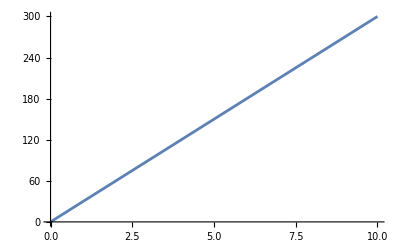

```mathematica
Plot[q1[t],{t,0,tf}]
```

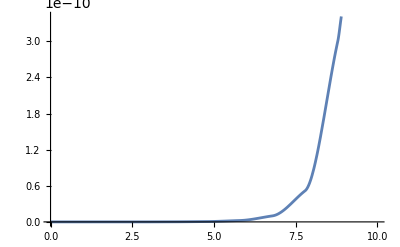

```mathematica
Plot[q2[t],{t,0,tf}]
```

```mathematica
q2[t]
```

InterpolatingFunction[…][t]

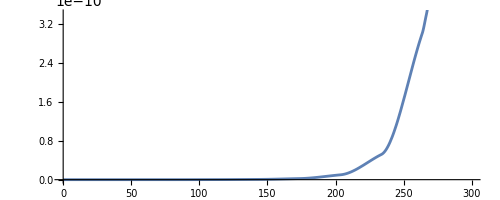

```mathematica
ParametricPlot[{q1[t],q2[t]}/.solTest,{t,0,10}]
```

```mathematica
Manipulate[ParametricPlot[{q1[t],q2[t]}/.solTest,{t,0,TF},PlotRange-> All],{TF,0.0001,tf,tf/10000}]
```

### Plots

```mathematica
p4[t_]=p4[t]/.solTest;
p6[t_]=p6[t]/.solTest;
p8[t_]=p8[t]/.solTest;
p10[t_]=p10[t]/.solTest;
q1[t_]=Subscript[q, 1][t]/.solTest;
q2[t_]=Subscript[q, 2][t]/.solTest;
q3[t_]=Subscript[q, 3][t]/.solTest;
q4[t_]=Subscript[q, 4][t]/.solTest;
q5[t_]=Subscript[q, 5][t]/.solTest;
q6[t_]=Subscript[q, 6][t]/.solTest;
q7[t_]=Subscript[q, 7][t]/.solTest;
q8[t_]=Subscript[q, 8][t]/.solTest;
q9[t_]=Subscript[q, 9][t]/.solTest;
q10[t_]=Subscript[q, 10][t]/.solTest;
q11[t_]=Subscript[q, 11][t]/.solTest;
```

```mathematica
Po1=Plot[p4[t],{t,0,tf},PlotLabel->p4,PlotPoints->5000];
Po2=Plot[p6[t],{t,0,tf},PlotLabel->p6,PlotPoints->5000];
Po3=Plot[p8[t],{t,0,tf},PlotLabel->p8, PlotPoints->5000];
Po4=Plot[p10[t],{t,0,tf},PlotLabel->p10,PlotPoints->5000];
Pp1=Plot[q1[t],{t,0,tf},PlotLabel->q1,PlotPoints->5000];
Pp2=Plot[q2[t],{t,0,tf},PlotLabel->q2,PlotPoints->5000];
Pp3=Plot[q3[t],{t,0,tf},PlotLabel->q3,PlotPoints->5000];
Pp4=Plot[q4[t],{t,0,tf},PlotLabel->q4,PlotPoints->5000];
Pp5=Plot[q5[t],{t,0,tf},PlotLabel->q5,PlotPoints->5000];
Pp6=Plot[q6[t],{t,0,tf},PlotLabel->q6,PlotPoints->5000];
Pp7=Plot[q7[t],{t,0,tf},PlotLabel->q7,PlotPoints->5000];
Pp8=Plot[q8[t],{t,0,tf},PlotLabel->q8,PlotPoints->5000];
Pp9=Plot[q9[t],{t,0,tf},PlotLabel->q9,PlotPoints->5000];
Pp10=Plot[q10[t],{t,0,tf},PlotLabel->q10,PlotPoints->5000];
Pp11=Plot[q11[t],{t,0,tf},PlotLabel->q11,PlotPoints->5000];
```

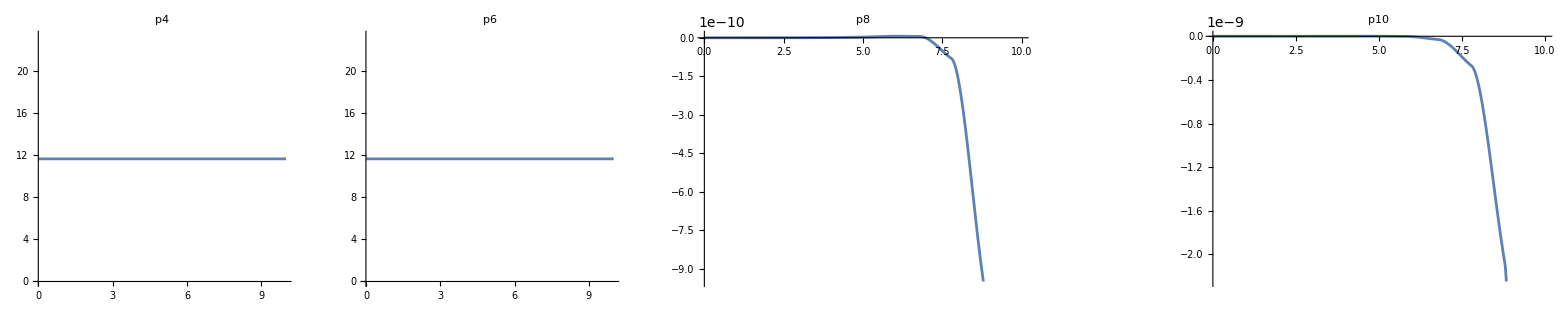

```mathematica
GraphicsRow[{Po1,Po2,Po3,,Po4}]
```

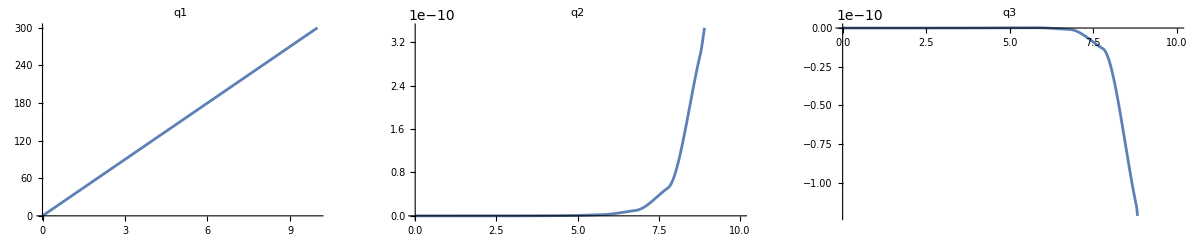

```mathematica
GraphicsRow[{Pp1,Pp2,Pp3}]
```

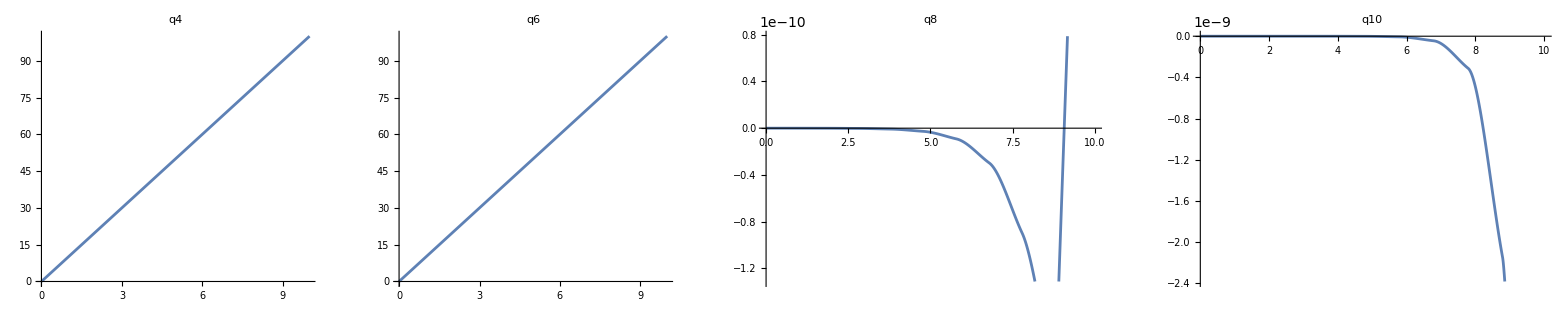

```mathematica
GraphicsRow[{Pp4,Pp6,Pp8,Pp10}]
```

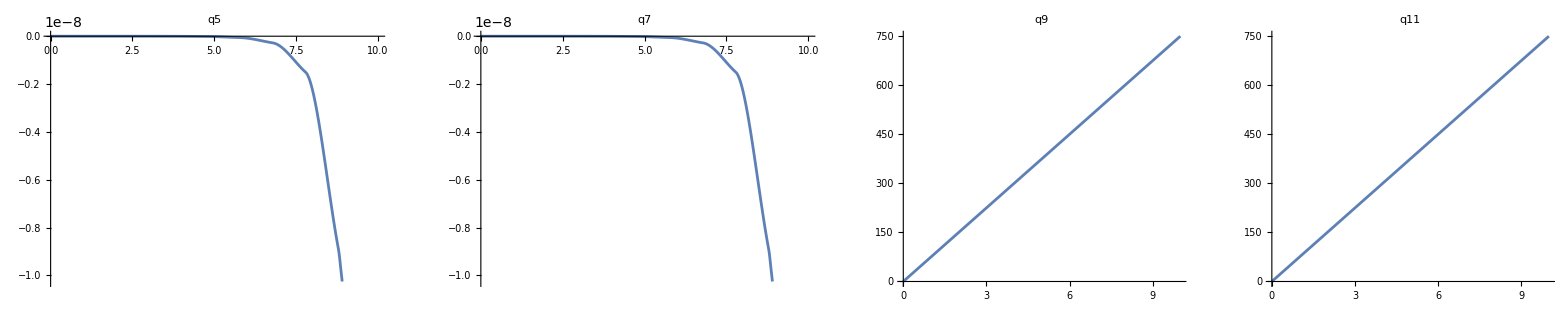

```mathematica
GraphicsRow[{Pp5,Pp7,Pp9,Pp11}]
```

### Energy

```mathematica
(*tE=TKE+TPE;*)
```

```mathematica
Cases[tE,A_[t],Infinity]//Union
Cases[tE,_Symbol,Infinity]//Union
Cases[tE,Subscript[q, n_][t],Infinity]//Union
Cases[tE,Subscript[q, n_]'[t],Infinity]//Union
```

{q_4[t],q_6[t],q_8[t],q_10[t],q_1'[t],q_2'[t],q_3'[t],q_4'[t],q_5'[t],q_6'[t],q_7'[t],q_8'[t],q_9'[t],q_10'[t],q_11'[t]}

{t}

{q_4[t],q_6[t],q_8[t],q_10[t]}

{q_1'[t],q_2'[t],q_3'[t],q_4'[t],q_5'[t],q_6'[t],q_7'[t],q_8'[t],q_9'[t],q_10'[t],q_11'[t]}

```mathematica
TotalE[t_]=tE;
```

```mathematica
r=0.4;R=3;
```

```mathematica
TotalE[0]/.solTest
```

389.083

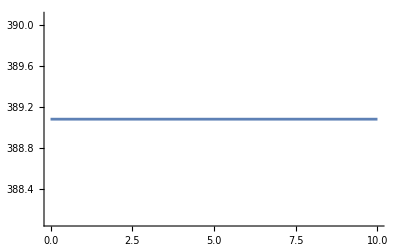

```mathematica
pL=Plot[Evaluate[tE/.solTest],{t,0,tf},PlotRange->{All,All}]
```

### Dynamic Animation

```mathematica
Subscript[q, 1][t_]=Subscript[q, 1][t]/.solTest
Subscript[q, 2][t_]=Subscript[q, 2][t]/.solTest
Subscript[q, 3][t_]=Subscript[q, 3][t]/.solTest
Subscript[q, 4][t_]=Subscript[q, 4][t]/.solTest
Subscript[q, 5][t_]=Subscript[q, 5][t]/.solTest
Subscript[q, 6][t_]=Subscript[q, 6][t]/.solTest
Subscript[q, 7][t_]=Subscript[q, 7][t]/.solTest
Subscript[q, 8][t_]=Subscript[q, 8][t]/.solTest
Subscript[q, 9][t_]=Subscript[q, 9][t]/.solTest
Subscript[q, 10][t_]=Subscript[q, 10][t]/.solTest
Subscript[q, 11][t_]=Subscript[q, 11][t]/.solTest
```

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

«8 more identical outputs»

```mathematica
robotGraphicDynAnim={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
};
```

```mathematica
robotGraphicDynAnimT[t_]=robotGraphicDynAnim;
```

```mathematica
scale=100
```

100

```mathematica
Animate[Show[Graphics3D[robotGraphicDynAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,tf,tf/500},AnimationRunning->False]
```

```mathematica
Manipulate[{Show[Graphics3D[robotGraphicDynAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->All,AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*)},{t,0,tf,tf/1000,Appearance-> "Open"}(*,AnimationRunning->False*)]
```

## continue to notebook part 3